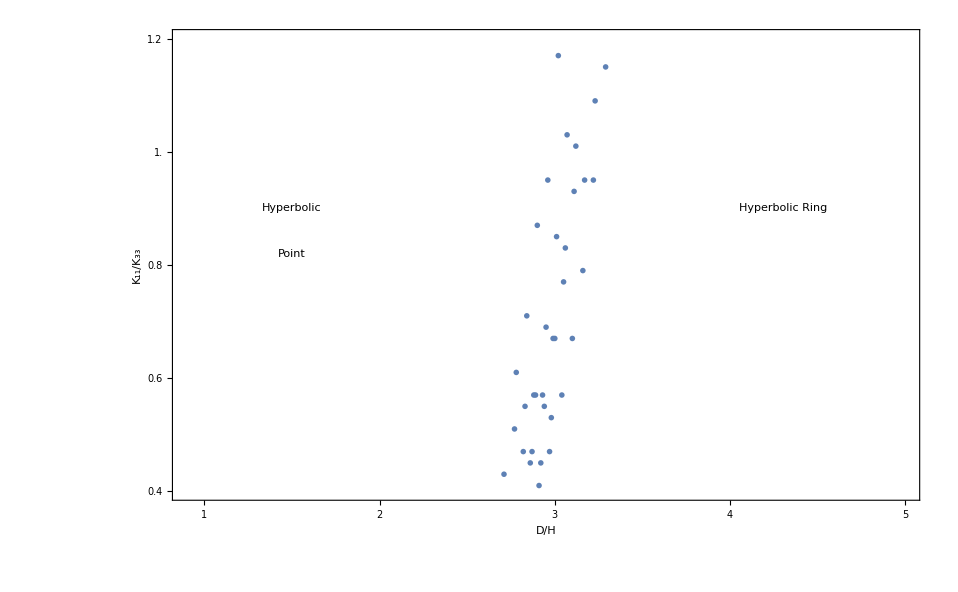

```mathematica
aa={{2.71,0.43},{2.77, 0.51},{2.78,0.61},{2.82,0.47},{2.83,0.55},{2.84,0.71},{2.86,0.45},{2.87,0.47},{2.88,0.57},{2.89,0.57},{2.90,0.87},{2.91,0.41},{2.92,0.45},{2.93,0.57},{2.94,0.55},{2.95,0.69},{2.96,0.95},{2.97,0.47},{2.98,0.53},{2.99,0.67},{3.0,0.67},{3.01,0.85},{3.02,1.17},{3.04,0.57},{3.05,0.77},{3.06,0.83},{3.07,1.03},{3.1,0.67},{3.11,0.93},{3.12,1.01},{3.16,0.79},{3.17,0.95},{3.22,0.95},{3.23,1.09},{3.29,1.15}};

ListPlot[aa, PlotMarkers->{Automatic, Medium},PlotRange->{{0.9,5},{0.4,1.2}},PlotStyle->PointSize[0.02], Frame->{True, True, False, False}, FrameTicks->{{{0.4,0.6,0.8,1.0,1.2},None},{{1,2,3,4,5},None}},LabelStyle->Large,FrameLabel->{{"K_11/K_33", None},{"D/H", None}},Epilog->{Text[Style["Hyperbolic",Large],{1.5,0.9}],Text[Style["Point",Large],{1.5,0.82}],Text[Style["Hyperbolic Ring",Large],{4.3,0.9}]}]
```

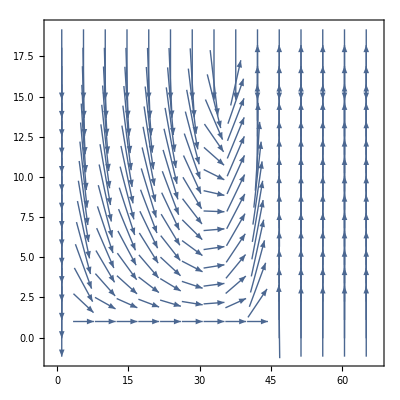

```mathematica
a={{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.707107,-0.707107},{0.496326,-0.868136},{0.358791,-0.933418},{0.270675,-0.962671},{0.211565,-0.977364},{0.169480,-0.985534},{0.137818,-0.990458},{0.112857,-0.993611},{0.092394,-0.995723},{0.075049,-0.997180},{0.059910,-0.998204},{0.046346,-0.998925},{0.033895,-0.999425},{0.022204,-0.999753},{0.010988,-0.999940},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.886854,-0.462050},{0.722265,-0.691616},{0.580862,-0.814002},{0.469837,-0.882753},{0.383697,-0.923459},{0.315999,-0.948760},{0.261610,-0.965174},{0.216812,-0.976213},{0.178973,-0.983854},{0.146224,-0.989251},{0.117216,-0.993106},{0.090946,-0.995856},{0.066651,-0.997776},{0.043722,-0.999044},{0.021653,-0.999766},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.941743,-0.336335},{0.827084,-0.562079},{0.708045,-0.706167},{0.601033,-0.799224},{0.508961,-0.860789},{0.430579,-0.902553},{0.363615,-0.931550},{0.305808,-0.952093},{0.255207,-0.966886},{0.210212,-0.977656},{0.169532,-0.985525},{0.132124,-0.991233},{0.097138,-0.995271},{0.063857,-0.997959},{0.031664,-0.999499},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.964144,-0.265380},{0.881618,-0.471964},{0.784227,-0.620474},{0.687818,-0.725883},{0.598340,-0.801242},{0.517339,-0.855781},{0.444567,-0.895746},{0.379106,-0.925353},{0.319854,-0.947467},{0.265725,-0.964049},{0.215726,-0.976454},{0.168972,-0.985621},{0.124685,-0.992196},{0.082172,-0.996618},{0.040805,-0.999167},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.975158,-0.221511},{0.912753,-0.408513},{0.832336,-0.554272},{0.746826,-0.665019},{0.662723,-0.748865},{0.582829,-0.812595},{0.508072,-0.861315},{0.438464,-0.898749},{0.373593,-0.927593},{0.312863,-0.949798},{0.255623,-0.966776},{0.201222,-0.979546},{0.149036,-0.988832},{0.098473,-0.995140},{0.048974,-0.998800},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.981325,-0.192357},{0.931906,-0.362700},{0.864199,-0.503150},{0.788197,-0.615423},{0.709954,-0.704248},{0.632694,-0.774402},{0.557956,-0.829871},{0.486333,-0.873774},{0.417899,-0.908494},{0.352451,-0.935830},{0.289641,-0.957135},{0.229052,-0.973414},{0.170243,-0.985402},{0.112761,-0.993622},{0.056161,-0.998422},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.985118,-0.171877},{0.944425,-0.328727},{0.886196,-0.463311},{0.818062,-0.575130},{0.745313,-0.666715},{0.671169,-0.741305},{0.597438,-0.801915},{0.525050,-0.851072},{0.454402,-0.890797},{0.385578,-0.922675},{0.318477,-0.947931},{0.252891,-0.967495},{0.188554,-0.982063},{0.125169,-0.992135},{0.062424,-0.998050},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.987622,-0.156856},{0.953028,-0.302884},{0.901942,-0.431857},{0.840212,-0.542257},{0.772330,-0.635221},{0.701310,-0.712856},{0.629031,-0.777380},{0.556595,-0.830784},{0.484606,-0.874732},{0.413350,-0.910572},{0.342917,-0.939366},{0.273275,-0.961936},{0.204319,-0.978904},{0.135903,-0.990722},{0.067858,-0.997695},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.989366,-0.145447},{0.959194,-0.282749},{0.913585,-0.406647},{0.857065,-0.515209},{0.793398,-0.608703},{0.725314,-0.688418},{0.654646,-0.755936},{0.582568,-0.812782},{0.509803,-0.860291},{0.436777,-0.899570},{0.363725,-0.931506},{0.290761,-0.956796},{0.217922,-0.975966},{0.145204,-0.989402},{0.072578,-0.997363},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.990638,-0.136518},{0.963780,-0.266698},{0.922456,-0.386103},{0.870205,-0.492689},{0.810171,-0.586194},{0.744772,-0.667319},{0.675735,-0.737144},{0.604238,-0.796804},{0.531067,-0.847330},{0.456741,-0.889600},{0.381601,-0.924327},{0.305880,-0.952070},{0.229744,-0.973251},{0.153316,-0.988177},{0.076704,-0.997054},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991601,-0.129335},{0.967308,-0.253604},{0.929410,-0.369049},{0.880708,-0.473659},{0.823818,-0.566855},{0.760856,-0.648921},{0.693409,-0.720544},{0.622617,-0.782526},{0.549288,-0.835633},{0.473995,-0.880528},{0.397163,-0.917748},{0.319121,-0.947714},{0.240143,-0.970738},{0.160475,-0.987040},{0.080351,-0.996767},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992357,-0.123396},{0.970111,-0.242662},{0.935022,-0.354591},{0.889322,-0.457281},{0.835186,-0.549968},{0.774445,-0.632642},{0.708530,-0.705680},{0.638515,-0.769609},{0.565198,-0.824955},{0.489185,-0.872180},{0.410956,-0.911655},{0.330921,-0.943659},{0.249450,-0.968388},{0.166902,-0.985974},{0.083632,-0.996497},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992972,-0.118346},{0.972411,-0.233274},{0.939686,-0.342037},{0.896586,-0.442871},{0.844905,-0.534917},{0.786214,-0.617954},{0.721781,-0.692121},{0.652593,-0.757709},{0.579416,-0.815032},{0.502864,-0.864365},{0.423459,-0.905915},{0.341674,-0.939819},{0.257967,-0.966154},{0.172800,-0.984957},{0.086648,-0.996239},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993490,-0.113918},{0.974363,-0.224982},{0.943689,-0.330833},{0.902896,-0.429859},{0.853457,-0.521163},{0.796697,-0.604379},{0.733716,-0.679457},{0.665399,-0.746488},{0.592465,-0.805596},{0.515517,-0.856879},{0.435100,-0.900382},{0.351739,-0.936098},{0.265972,-0.963981},{0.178361,-0.983965},{0.089497,-0.995987},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993942,-0.109906},{0.976078,-0.217421},{0.947240,-0.320524},{0.908558,-0.417758},{0.861221,-0.508230},{0.806323,-0.591476},{0.744793,-0.667296},{0.677404,-0.735611},{0.604806,-0.796373},{0.527576,-0.849508},{0.446268,-0.894899},{0.361449,-0.932392},{0.273728,-0.961807},{0.183765,-0.982970},{0.092271,-0.995734},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994351,-0.106142},{0.977639,-0.210290},{0.950502,-0.310720},{0.913812,-0.406138},{0.868504,-0.495681},{0.815451,-0.578826},{0.755408,-0.655255},{0.689020,-0.724743},{0.616852,-0.787079},{0.539440,-0.842024},{0.457329,-0.889297},{0.371121,-0.928585},{0.281488,-0.959565},{0.189188,-0.981941},{0.095060,-0.995472},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994735,-0.102485},{0.979111,-0.203325},{0.953601,-0.301074},{0.918852,-0.394603},{0.875562,-0.483105},{0.824389,-0.566023},{0.765907,-0.642951},{0.700619,-0.713535},{0.628988,-0.777415},{0.551486,-0.834184},{0.468639,-0.883390},{0.381066,-0.924548},{0.289504,-0.957177},{0.194810,-0.980841},{0.097956,-0.995191},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995107,-0.098807},{0.980546,-0.196290},{0.956642,-0.291267},{0.923840,-0.382780},{0.882615,-0.470097},{0.833409,-0.552657},{0.776606,-0.629986},{0.712550,-0.701621},{0.641580,-0.767056},{0.564085,-0.825717},{0.480550,-0.876967},{0.391604,-0.920134},{0.298037,-0.954554},{0.200815,-0.979629},{0.101057,-0.994881},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995478,-0.094991},{0.981984,-0.188964},{0.959710,-0.280992},{0.928913,-0.370299},{0.889852,-0.456250},{0.842752,-0.538302},{0.787795,-0.615938},{0.725143,-0.688598},{0.654988,-0.755639},{0.577609,-0.816313},{0.493430,-0.869786},{0.403068,-0.915170},{0.307368,-0.951591},{0.207406,-0.978255},{0.104468,-0.994528},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995858,-0.090925},{0.983459,-0.181128},{0.962876,-0.269944},{0.934186,-0.356786},{0.897439,-0.441138},{0.852638,-0.522502},{0.799744,-0.600341},{0.738718,-0.674014},{0.669573,-0.742747},{0.592444,-0.805611},{0.507664,-0.861555},{0.415822,-0.909446},{0.317804,-0.948156},{0.214807,-0.976657},{0.108308,-0.994117},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996252,-0.086496},{0.984998,-0.172567},{0.966196,-0.257810},{0.939755,-0.341849},{0.905518,-0.424307},{0.863259,-0.504761},{0.812706,-0.582674},{0.753585,-0.657351},{0.685696,-0.727888},{0.608992,-0.793176},{0.523674,-0.851919},{0.430270,-0.902700},{0.329697,-0.944087},{0.223278,-0.974755},{0.112715,-0.993627},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996666,-0.081591},{0.986617,-0.163057},{0.969708,-0.244268},{0.945688,-0.325074},{0.914199,-0.405266},{0.874779,-0.484522},{0.826903,-0.562344},{0.770037,-0.637999},{0.703721,-0.710476},{0.627676,-0.778474},{0.541918,-0.840431},{0.446870,-0.894599},{0.343455,-0.939169},{0.233128,-0.972446},{0.117856,-0.993031},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997101,-0.076094},{0.988324,-0.152369},{0.973431,-0.228979},{0.952026,-0.306019},{0.923551,-0.383476},{0.887314,-0.461167},{0.842519,-0.538666},{0.788339,-0.615242},{0.724005,-0.689795},{0.648939,-0.760840},{0.562902,-0.826523},{0.466148,-0.884707},{0.359561,-0.933122},{0.244731,-0.969591},{0.123934,-0.992290},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997555,-0.069886},{0.990114,-0.140264},{0.977360,-0.211585},{0.958763,-0.284208},{0.933588,-0.358347},{0.900915,-0.433996},{0.859670,-0.510850},{0.808699,-0.588222},{0.746872,-0.664968},{0.673230,-0.739433},{0.587181,-0.809456},{0.488712,-0.872445},{0.378601,-0.925560},{0.258551,-0.965998},{0.131210,-0.991355},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998023,-0.062846},{0.991967,-0.126500},{0.981450,-0.191717},{0.965839,-0.259142},{0.944245,-0.329243},{0.915537,-0.402234},{0.878367,-0.477987},{0.831233,-0.555924},{0.772582,-0.634915},{0.700980,-0.713181},{0.615350,-0.788254},{0.515269,-0.857028},{0.401288,-0.915952},{0.275178,-0.961393},{0.140016,-0.990149},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998495,-0.054852},{0.993839,-0.110830},{0.985616,-0.169000},{0.973119,-0.230302},{0.955347,-0.295486},{0.930996,-0.365031},{0.898465,-0.439045},{0.855897,-0.517147},{0.801265,-0.598309},{0.732550,-0.680713},{0.648020,-0.761624},{0.546632,-0.837373},{0.428508,-0.903538},{0.295376,-0.955381},{0.150799,-0.988564},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998951,-0.045785},{0.995665,-0.093013},{0.989714,-0.143060},{0.980370,-0.197169},{0.966575,-0.256385},{0.946914,-0.321487},{0.919586,-0.392890},{0.882399,-0.470502},{0.832824,-0.553538},{0.768145,-0.640276},{0.685765,-0.727823},{0.583718,-0.811957},{0.461367,-0.887210},{0.320163,-0.947362},{0.164175,-0.986431},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999368,-0.035533},{0.997345,-0.072824},{0.993532,-0.113553},{0.987238,-0.159255},{0.977427,-0.211272},{0.962663,-0.270702},{0.941031,-0.338319},{0.910078,-0.414436},{0.866788,-0.498677},{0.807662,-0.589646},{0.729003,-0.684510},{0.627507,-0.778611},{0.501243,-0.865306},{0.350923,-0.936404},{0.181021,-0.983479},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999712,-0.023994},{0.998746,-0.050062},{0.996781,-0.080177},{0.993232,-0.116144},{0.987187,-0.159570},{0.977301,-0.211856},{0.961683,-0.274164},{0.937751,-0.347308},{0.902101,-0.431525},{0.850447,-0.526060},{0.777777,-0.628540},{0.678927,-0.734206},{0.549842,-0.835269},{0.389591,-0.920988},{0.202648,-0.979252},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999939,-0.011078},{0.999698,-0.024561},{0.999088,-0.042706},{0.997716,-0.067542},{0.994899,-0.100872},{0.989529,-0.144334},{0.979910,-0.199440},{0.963542,-0.267558},{0.936851,-0.349728},{0.894918,-0.446230},{0.831340,-0.555764},{0.738551,-0.674198},{0.609162,-0.793046},{0.438922,-0.898525},{0.231108,-0.972928},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999995,0.003295},{0.999993,0.003805},{0.999999,-0.001010},{0.999911,-0.013336},{0.999385,-0.035052},{0.997693,-0.067888},{0.993528,-0.113586},{0.984744,-0.174009},{0.967962,-0.251095},{0.938036,-0.346537},{0.887438,-0.460926},{0.805904,-0.592046},{0.681229,-0.732071},{0.502870,-0.864362},{0.269810,-0.962913},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999816,0.019204},{0.999383,0.035131},{0.998990,0.044933},{0.998925,0.046360},{0.999292,0.037634},{0.999853,0.017163},{0.999859,-0.016779},{0.997798,-0.066325},{0.990955,-0.134192},{0.974671,-0.223644},{0.941165,-0.337947},{0.878002,-0.478656},{0.767051,-0.641586},{0.586916,-0.809648},{0.324798,-0.945783},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999324,0.036750},{0.997582,0.069505},{0.995473,0.095047},{0.993800,0.111179},{0.993194,0.116468},{0.993957,0.109769},{0.995965,0.089738},{0.998520,0.054394},{1.000000,0.000708},{0.997124,-0.075786},{0.983447,-0.181193},{0.946541,-0.322583},{0.863522,-0.504311},{0.697431,-0.716652},{0.407493,-0.913208},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998425,0.056097},{0.994251,0.107071},{0.988806,0.149207},{0.983570,0.180527},{0.979744,0.200253},{0.978117,0.208056},{0.979094,0.203408},{0.982729,0.185049},{0.988619,0.150441},{0.995471,0.095063},{0.999936,0.011315},{0.993596,-0.112990},{0.955452,-0.295146},{0.835789,-0.549051},{0.540013,-0.841657},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996988,0.077552},{0.988968,0.148128},{0.978269,0.207341},{0.967287,0.253683},{0.957806,0.287417},{0.950926,0.309418},{0.947288,0.320383},{0.947313,0.320308},{0.951374,0.308038},{0.959808,0.280656},{0.972664,0.232217},{0.988578,0.150713},{0.999941,0.010898},{0.971244,-0.238087},{0.756587,-0.653893},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994816,0.101689},{0.981140,0.193299},{0.962976,0.269587},{0.943994,0.329963},{0.926529,0.376224},{0.911716,0.410821},{0.899970,0.435953},{0.891437,0.453146},{0.886317,0.463079},{0.885029,0.465536},{0.888309,0.459246},{0.897572,0.440869},{0.916626,0.399746},{0.956434,0.291948},{0.996143,-0.087741},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991571,0.129567},{0.969834,0.243768},{0.941681,0.336506},{0.912556,0.408952},{0.885261,0.465094},{0.860591,0.509296},{0.838194,0.545372},{0.817253,0.576279},{0.796854,0.604171},{0.775905,0.630850},{0.752290,0.658832},{0.720295,0.693668},{0.662218,0.749311},{0.513018,0.858378},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.986607,0.163113},{0.953426,0.301627},{0.912385,0.409333},{0.871302,0.490748},{0.833235,0.552919},{0.798161,0.602444},{0.764379,0.644768},{0.729500,0.683981},{0.691049,0.722808},{0.646345,0.763045},{0.591404,0.806375},{0.518019,0.855369},{0.410038,0.912069},{0.241326,0.970444},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.978590,0.205820},{0.928899,0.370333},{0.871608,0.490204},{0.817353,0.576137},{0.768966,0.639290},{0.724999,0.688749},{0.681678,0.731653},{0.634312,0.773077},{0.578589,0.815619},{0.510859,0.859665},{0.428096,0.903733},{0.323537,0.946215},{0.186092,0.982532},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.964486,0.264134},{0.890358,0.455261},{0.813037,0.582213},{0.745472,0.666538},{0.689278,0.724497},{0.640909,0.767617},{0.593521,0.804818},{0.538637,0.842538},{0.469431,0.882969},{0.380472,0.924792},{0.275272,0.961366},{0.151145,0.988512},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.936641,0.350292},{0.825719,0.564082},{0.724972,0.688779},{0.646091,0.763260},{0.587679,0.809094},{0.543861,0.839175},{0.503708,0.863874},{0.450884,0.892582},{0.376600,0.926376},{0.261630,0.965168},{0.135966,0.990713},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.872799,0.488080},{0.708654,0.705557},{0.585594,0.810604},{0.502474,0.864593},{0.451775,0.892132},{0.427711,0.903916},{0.417893,0.908496},{0.380084,0.924952},{0.331008,0.943628},{0.152046,0.988373},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.693359,0.720593},{0.477575,0.878591},{0.356590,0.934261},{0.290194,0.956968},{0.261116,0.965307},{0.273749,0.961801},{0.355428,0.934704},{0.307537,0.951536},{0.447214,0.894427},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.447214,0.894427},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}}};
c=ListVectorPlot[a]
```

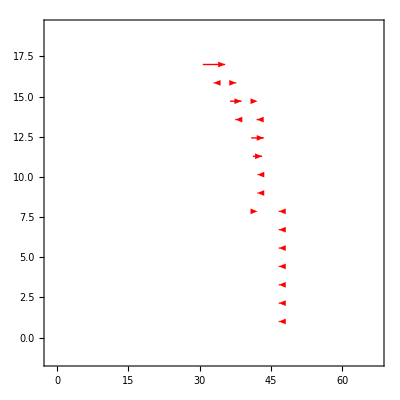

```mathematica
b={{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}};
d=ListVectorPlot[b, VectorStyle->Red]
```

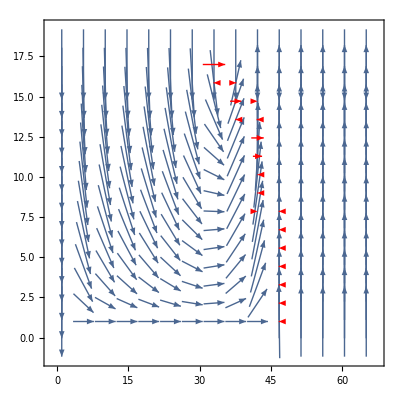

```mathematica
Show[c,d]
```

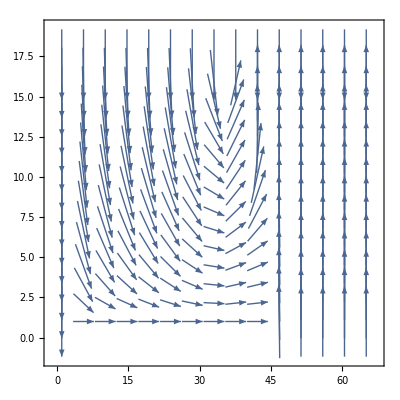

```mathematica
a={{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.707107,-0.707107},{0.496215,-0.868200},{0.358606,-0.933489},{0.270444,-0.962736},{0.211305,-0.977420},{0.169204,-0.985581},{0.137536,-0.990497},{0.112579,-0.993643},{0.092129,-0.995747},{0.074806,-0.997198},{0.059696,-0.998217},{0.046166,-0.998934},{0.033755,-0.999430},{0.022108,-0.999756},{0.010939,-0.999940},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.886796,-0.462162},{0.722085,-0.691804},{0.580562,-0.814216},{0.469440,-0.882964},{0.383228,-0.923654},{0.315483,-0.948931},{0.261072,-0.965319},{0.216274,-0.976333},{0.178455,-0.983948},{0.145744,-0.989322},{0.116790,-0.993157},{0.090588,-0.995888},{0.066373,-0.997795},{0.043532,-0.999052},{0.021557,-0.999768},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.941676,-0.336520},{0.826874,-0.562387},{0.707677,-0.706536},{0.600520,-0.799610},{0.508332,-0.861161},{0.429866,-0.902893},{0.362853,-0.931846},{0.305032,-0.952342},{0.254450,-0.967086},{0.209503,-0.977808},{0.168898,-0.985634},{0.131589,-0.991304},{0.096719,-0.995312},{0.063570,-0.997977},{0.031518,-0.999503},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.964076,-0.265625},{0.881391,-0.472388},{0.783809,-0.621002},{0.687214,-0.726455},{0.597576,-0.801812},{0.516453,-0.856315},{0.443602,-0.896224},{0.378108,-0.925762},{0.318867,-0.947799},{0.264792,-0.964305},{0.214885,-0.976639},{0.168258,-0.985743},{0.124124,-0.992267},{0.081786,-0.996650},{0.040608,-0.999175},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.975089,-0.221814},{0.912511,-0.409053},{0.831874,-0.554965},{0.746140,-0.665789},{0.661836,-0.749649},{0.581780,-0.813346},{0.506911,-0.861998},{0.437247,-0.899341},{0.372377,-0.928082},{0.311703,-0.950180},{0.254570,-0.967054},{0.200322,-0.979730},{0.148326,-0.988939},{0.097983,-0.995188},{0.048724,-0.998812},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.981254,-0.192721},{0.931648,-0.363363},{0.863693,-0.504018},{0.787429,-0.616406},{0.708941,-0.705267},{0.631479,-0.775393},{0.556594,-0.830785},{0.484889,-0.874576},{0.416443,-0.909162},{0.351051,-0.936356},{0.288362,-0.957521},{0.227954,-0.973672},{0.169373,-0.985552},{0.112159,-0.993690},{0.055853,-0.998439},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.985043,-0.172308},{0.944148,-0.329523},{0.885641,-0.464370},{0.817204,-0.576348},{0.744166,-0.667995},{0.669775,-0.742564},{0.595860,-0.803089},{0.523362,-0.852111},{0.452686,-0.891670},{0.383918,-0.923367},{0.316953,-0.948441},{0.251575,-0.967838},{0.187509,-0.982263},{0.124444,-0.992227},{0.062053,-0.998073},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.987541,-0.157363},{0.952727,-0.303829},{0.901331,-0.433131},{0.839254,-0.543739},{0.771033,-0.636795},{0.699718,-0.714419},{0.627212,-0.778849},{0.554635,-0.832094},{0.482601,-0.875840},{0.411399,-0.911455},{0.341117,-0.940021},{0.271715,-0.962378},{0.203077,-0.979163},{0.135040,-0.990840},{0.067415,-0.997725},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.989278,-0.146042},{0.958864,-0.283865},{0.912908,-0.408165},{0.855991,-0.516991},{0.791931,-0.610611},{0.723496,-0.690328},{0.652553,-0.757743},{0.580298,-0.814404},{0.507468,-0.861671},{0.434495,-0.900674},{0.361612,-0.932329},{0.288924,-0.957352},{0.216455,-0.976293},{0.144183,-0.989551},{0.072054,-0.997401},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.990541,-0.137214},{0.963415,-0.268012},{0.921700,-0.387903},{0.868997,-0.494818},{0.808505,-0.588489},{0.742694,-0.669631},{0.673328,-0.739344},{0.601613,-0.798788},{0.528354,-0.849024},{0.454077,-0.890962},{0.379126,-0.925345},{0.303724,-0.952760},{0.228018,-0.973657},{0.152113,-0.988363},{0.076086,-0.997101},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991494,-0.130150},{0.966901,-0.255150},{0.928562,-0.371178},{0.879342,-0.476191},{0.821921,-0.569601},{0.758475,-0.651702},{0.690636,-0.723202},{0.619579,-0.784934},{0.546134,-0.837698},{0.470890,-0.882192},{0.394269,-0.918995},{0.316593,-0.948562},{0.238117,-0.971237},{0.159060,-0.987269},{0.079624,-0.996825},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992238,-0.124351},{0.969655,-0.244479},{0.934064,-0.357105},{0.887771,-0.460285},{0.833020,-0.553243},{0.771712,-0.635972},{0.705332,-0.708877},{0.634996,-0.772515},{0.561533,-0.827454},{0.485564,-0.874201},{0.407573,-0.913173},{0.327959,-0.944692},{0.247072,-0.968997},{0.165239,-0.986253},{0.082777,-0.996568},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992838,-0.119466},{0.971896,-0.235412},{0.938601,-0.345005},{0.894817,-0.446432},{0.842425,-0.538814},{0.783070,-0.621934},{0.718086,-0.695954},{0.648512,-0.761204},{0.575152,-0.818047},{0.498640,-0.866809},{0.419503,-0.907754},{0.338205,-0.941073},{0.255178,-0.966894},{0.170848,-0.985297},{0.085644,-0.996326},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993338,-0.115234},{0.973778,-0.227499},{0.942453,-0.334339},{0.900875,-0.434080},{0.850610,-0.525797},{0.793072,-0.609128},{0.729440,-0.684045},{0.660662,-0.750683},{0.587501,-0.809223},{0.510588,-0.859826},{0.430474,-0.902603},{0.347676,-0.937615},{0.262701,-0.964877},{0.176069,-0.984378},{0.088317,-0.996092},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993770,-0.111455},{0.975412,-0.220388},{0.945829,-0.324667},{0.906241,-0.422761},{0.857946,-0.513740},{0.802139,-0.597138},{0.739842,-0.672781},{0.671902,-0.740640},{0.599025,-0.800730},{0.521822,-0.853054},{0.440858,-0.897577},{0.356689,-0.934223},{0.269891,-0.962891},{0.181074,-0.983469},{0.090885,-0.995861},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994154,-0.107968},{0.976879,-0.213791},{0.948886,-0.315619},{0.911152,-0.412070},{0.864732,-0.502233},{0.810617,-0.585577},{0.749670,-0.661812},{0.682626,-0.730768},{0.610118,-0.792310},{0.532723,-0.846290},{0.451002,-0.892523},{0.365545,-0.930794},{0.276989,-0.960873},{0.186031,-0.982544},{0.093432,-0.995626},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994510,-0.104639},{0.978243,-0.207462},{0.951750,-0.306876},{0.915796,-0.401643},{0.871216,-0.490899},{0.818803,-0.574074},{0.759259,-0.650789},{0.693191,-0.720754},{0.621146,-0.783695},{0.543648,-0.839314},{0.461242,-0.887274},{0.374538,-0.927211},{0.284230,-0.958756},{0.191106,-0.981569},{0.096046,-0.995377},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994850,-0.101354},{0.979553,-0.201187},{0.954521,-0.298145},{0.920330,-0.391143},{0.877609,-0.479377},{0.826958,-0.562264},{0.768907,-0.639361},{0.703927,-0.710272},{0.632456,-0.774597},{0.554945,-0.831887},{0.471910,-0.881647},{0.383966,-0.923347},{0.291859,-0.956461},{0.196473,-0.980509},{0.098817,-0.995106},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995186,-0.098007},{0.980850,-0.194767},{0.957282,-0.289155},{0.924886,-0.380244},{0.884095,-0.467308},{0.835313,-0.549775},{0.778893,-0.627157},{0.715148,-0.698973},{0.644387,-0.764699},{0.566968,-0.823740},{0.483351,-0.875427},{0.394144,-0.919049},{0.300140,-0.953895},{0.202320,-0.979319},{0.101843,-0.994801},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995525,-0.094500},{0.982166,-0.188015},{0.960104,-0.279644},{0.929578,-0.368625},{0.890835,-0.454327},{0.844081,-0.536215},{0.789479,-0.613778},{0.727162,-0.686466},{0.657285,-0.753642},{0.580082,-0.814558},{0.495930,-0.868362},{0.405414,-0.914133},{0.309362,-0.950944},{0.208860,-0.977946},{0.105236,-0.994447},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995875,-0.090741},{0.983529,-0.180750},{0.963042,-0.269352},{0.934502,-0.355958},{0.897970,-0.440056},{0.853455,-0.521167},{0.800911,-0.598784},{0.740271,-0.672309},{0.671501,-0.741004},{0.594674,-0.803967},{0.510052,-0.860144},{0.418163,-0.908372},{0.319860,-0.947465},{0.216340,-0.976318},{0.109128,-0.994028},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996240,-0.086639},{0.984958,-0.172795},{0.966140,-0.258019},{0.939733,-0.341909},{0.905621,-0.424089},{0.863605,-0.504169},{0.813421,-0.581675},{0.754773,-0.655987},{0.687398,-0.726281},{0.611163,-0.791505},{0.526164,-0.850383},{0.432835,-0.901473},{0.332027,-0.943270},{0.225056,-0.974346},{0.113678,-0.993518},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996624,-0.082105},{0.986465,-0.163973},{0.969427,-0.245381},{0.945326,-0.326126},{0.913875,-0.405995},{0.874673,-0.484714},{0.827218,-0.561882},{0.770955,-0.636890},{0.705350,-0.708859},{0.630002,-0.776593},{0.544777,-0.838581},{0.449951,-0.893053},{0.346340,-0.938109},{0.235374,-0.971905},{0.119086,-0.992884},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997027,-0.077056},{0.988053,-0.154113},{0.972912,-0.231177},{0.951305,-0.308252},{0.922786,-0.385312},{0.886755,-0.462239},{0.842467,-0.538748},{0.789077,-0.614294},{0.725728,-0.687982},{0.651676,-0.758497},{0.566467,-0.824085},{0.470132,-0.882596},{0.363386,-0.931639},{0.247756,-0.968823},{0.125607,-0.992080},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997447,-0.071414},{0.989715,-0.143053},{0.976581,-0.215149},{0.957654,-0.287921},{0.932352,-0.361553},{0.899887,-0.436124},{0.859270,-0.511522},{0.809346,-0.587332},{0.748878,-0.662708},{0.676689,-0.736269},{0.591885,-0.806022},{0.494120,-0.869393},{0.383896,-0.923376},{0.262797,-0.964851},{0.133577,-0.991038},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997878,-0.065110},{0.991429,-0.130650},{0.980391,-0.197060},{0.964309,-0.264780},{0.942495,-0.334220},{0.914006,-0.405700},{0.877624,-0.479350},{0.831870,-0.554970},{0.775077,-0.631867},{0.705535,-0.708675},{0.621748,-0.783217},{0.522802,-0.852454},{0.408801,-0.912624},{0.281284,-0.959625},{0.143449,-0.989658},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998311,-0.058094},{0.993156,-0.116791},{0.984262,-0.176713},{0.971141,-0.238507},{0.953046,-0.302825},{0.928925,-0.370269},{0.897367,-0.441284},{0.856589,-0.515999},{0.804459,-0.594008},{0.738628,-0.674114},{0.656804,-0.754061},{0.557222,-0.830363},{0.439285,-0.898348},{0.304276,-0.952584},{0.155855,-0.987780},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998732,-0.050343},{0.994844,-0.101413},{0.988075,-0.153971},{0.977948,-0.208849},{0.963714,-0.266937},{0.944278,-0.329148},{0.918113,-0.396319},{0.883180,-0.469034},{0.836894,-0.547364},{0.776186,-0.630505},{0.697745,-0.716346},{0.598570,-0.801070},{0.476867,-0.878975},{0.333230,-0.942845},{0.171702,-0.985149},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999123,-0.041869},{0.996422,-0.084520},{0.991671,-0.128800},{0.984449,-0.175670},{0.974072,-0.226239},{0.959490,-0.281741},{0.939166,-0.343462},{0.910923,-0.412576},{0.871807,-0.489850},{0.818014,-0.575198},{0.745019,-0.667044},{0.648092,-0.761562},{0.523464,-0.852048},{0.370200,-0.928952},{0.192347,-0.981327},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999464,-0.032732},{0.997805,-0.066216},{0.994856,-0.101302},{0.990290,-0.139014},{0.983553,-0.180619},{0.973743,-0.227650},{0.959454,-0.281866},{0.938555,-0.345130},{0.907922,-0.419140},{0.863160,-0.504930},{0.798451,-0.602059},{0.706829,-0.707385},{0.581403,-0.813616},{0.418122,-0.908391},{0.219913,-0.975519},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999734,-0.023052},{0.998908,-0.046726},{0.997421,-0.071768},{0.995071,-0.099170},{0.991478,-0.130271},{0.985986,-0.166826},{0.977479,-0.211031},{0.964120,-0.265466},{0.942957,-0.332915},{0.909389,-0.415947},{0.856557,-0.516053},{0.774967,-0.632001},{0.653194,-0.757191},{0.481228,-0.876595},{0.257917,-0.966167},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999915,-0.013024},{0.999651,-0.026420},{0.999171,-0.040717},{0.998388,-0.056752},{0.997122,-0.075813},{0.995012,-0.099757},{0.991370,-0.131094},{0.984919,-0.173018},{0.973337,-0.229380},{0.952511,-0.304505},{0.915375,-0.402602},{0.850406,-0.526128},{0.740550,-0.672001},{0.565430,-0.824796},{0.312567,-0.949896},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999996,-0.002920},{0.999983,-0.005837},{0.999960,-0.008933},{0.999919,-0.012754},{0.999831,-0.018392},{0.999618,-0.027647},{0.999069,-0.043149},{0.997655,-0.068447},{0.994136,-0.108140},{0.985780,-0.168042},{0.966863,-0.255294},{0.925914,-0.377735},{0.841341,-0.540504},{0.677765,-0.735278},{0.395562,-0.918439},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999976,0.006907},{0.999898,0.014315},{0.999746,0.022525},{0.999506,0.031422},{0.999189,0.040258},{0.998874,0.047451},{0.998726,0.050471},{0.998952,0.045767},{0.999590,0.028622},{0.999974,-0.007276},{0.997493,-0.070766},{0.984619,-0.174715},{0.941595,-0.336747},{0.820646,-0.571437},{0.529532,-0.848290},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999872,0.016025},{0.999450,0.033167},{0.998630,0.052332},{0.997260,0.073977},{0.995203,0.097829},{0.992451,0.122644},{0.989267,0.146122},{0.986295,0.164993},{0.984549,0.175107},{0.985243,0.171161},{0.989339,0.145629},{0.996315,0.085770},{0.999432,-0.033689},{0.964718,-0.263287},{0.749675,-0.661806},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999713,0.023947},{0.998763,0.049717},{0.996879,0.078941},{0.993620,0.112777},{0.988450,0.151547},{0.980927,0.194377},{0.970989,0.239125},{0.959189,0.282767},{0.946755,0.321955},{0.935488,0.353358},{0.927538,0.373729},{0.925425,0.378931},{0.933595,0.358331},{0.963273,0.268523},{0.995532,-0.094429},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999545,0.030149},{0.998021,0.062885},{0.994922,0.100648},{0.989366,0.145447},{0.980135,0.198331},{0.965941,0.258764},{0.945911,0.324425},{0.919968,0.391992},{0.888781,0.458332},{0.853402,0.521253},{0.814007,0.580855},{0.766592,0.642134},{0.694306,0.719680},{0.531334,0.847163},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999418,0.034118},{0.997435,0.071573},{0.993287,0.115677},{0.985537,0.169462},{0.972009,0.234944},{0.950103,0.311936},{0.917663,0.397360},{0.873641,0.486571},{0.817758,0.575562},{0.750386,0.661000},{0.671267,0.741215},{0.574585,0.818445},{0.445215,0.895424},{0.257320,0.966326},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999373,0.035399},{0.997201,0.074769},{0.992495,0.122283},{0.983260,0.182208},{0.966142,0.258010},{0.936676,0.350198},{0.890914,0.454173},{0.826908,0.562338},{0.742915,0.669386},{0.638776,0.769393},{0.518595,0.855020},{0.379396,0.925234},{0.211708,0.977333},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999433,0.033667},{0.997428,0.071674},{0.992907,0.118890},{0.983482,0.181004},{0.964575,0.263807},{0.929104,0.369818},{0.870480,0.492204},{0.787272,0.616606},{0.674782,0.738017},{0.526886,0.849936},{0.364464,0.931218},{0.191121,0.981566},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999585,0.028822},{0.998083,0.061886},{0.994542,0.104333},{0.986598,0.163171},{0.968836,0.247702},{0.930579,0.366091},{0.859747,0.510720},{0.761805,0.647807},{0.630775,0.775965},{0.415943,0.909391},{0.203019,0.979175},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999778,0.021088},{0.998957,0.045664},{0.996929,0.078312},{0.991976,0.126425},{0.979143,0.203170},{0.944046,0.329813},{0.857697,0.514155},{0.748403,0.663244},{0.661231,0.750182},{0.288133,0.957590},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999938,0.011116},{0.999706,0.024233},{0.999110,0.042185},{0.997523,0.070335},{0.992580,0.121593},{0.972194,0.234178},{0.858449,0.512899},{0.674169,0.738577},{0.894427,0.447214},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{0.894427,0.447214},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{-0.000000,-1.000000}}};
c=ListVectorPlot[a]
```

```mathematica
b={{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}};
d=ListVectorPlot[b, VectorStyle->Red]
```

-Graphics-

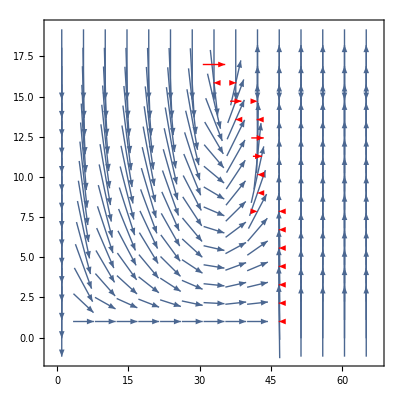

```mathematica
Show[c,d]
```

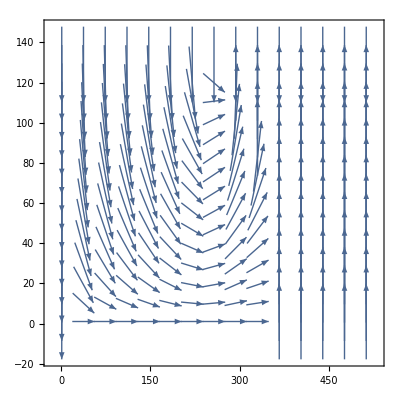

```mathematica
a={{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000}},{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{0.124259,-0.992250},{0.115123,-0.993351},{0.106891,-0.994271},{0.099477,-0.995040},{0.092807,-0.995684},{0.086805,-0.996225},{0.081399,-0.996682},{0.076520,-0.997068},{0.072108,-0.997397},{0.068107,-0.997678},{0.064469,-0.997920},{0.061152,-0.998128},{0.058118,-0.998310},{0.055336,-0.998468},{0.052776,-0.998606},{0.050415,-0.998728},{0.048231,-0.998836},{0.046206,-0.998932},{0.044323,-0.999017},{0.042567,-0.999094},{0.040928,-0.999162},{0.039392,-0.999224},{0.037952,-0.999280},{0.036597,-0.999330},{0.035321,-0.999376},{0.034117,-0.999418},{0.032979,-0.999456},{0.031901,-0.999491},{0.030878,-0.999523},{0.029907,-0.999553},{0.028983,-0.999580},{0.028102,-0.999605},{0.027263,-0.999628},{0.026461,-0.999650},{0.025694,-0.999670},{0.024959,-0.999688},{0.024255,-0.999706},{0.023580,-0.999722},{0.022931,-0.999737},{0.022307,-0.999751},{0.021706,-0.999764},{0.021128,-0.999777},{0.020570,-0.999788},{0.020031,-0.999799},{0.019511,-0.999810},{0.019008,-0.999819},{0.018521,-0.999828},{0.018050,-0.999837},{0.017593,-0.999845},{0.017150,-0.999853},{0.016720,-0.999860},{0.016303,-0.999867},{0.015897,-0.999874},{0.015503,-0.999880},{0.015119,-0.999886},{0.014745,-0.999891},{0.014381,-0.999897},{0.014026,-0.999902},{0.013679,-0.999906},{0.013341,-0.999911},{0.013011,-0.999915},{0.012688,-0.999920},{0.012373,-0.999923},{0.012064,-0.999927},{0.011762,-0.999931},{0.011466,-0.999934},{0.011176,-0.999938},{0.010892,-0.999941},{0.010614,-0.999944},{0.010340,-0.999947},{0.010072,-0.999949},{0.009809,-0.999952},{0.009550,-0.999954},{0.009295,-0.999957},{0.009045,-0.999959},{0.008799,-0.999961},{0.008556,-0.999963},{0.008318,-0.999965},{0.008082,-0.999967},{0.007851,-0.999969},{0.007622,-0.999971},{0.007397,-0.999973},{0.007175,-0.999974},{0.006955,-0.999976},{0.006738,-0.999977},{0.006524,-0.999979},{0.006313,-0.999980},{0.006104,-0.999981},{0.005897,-0.999983},{0.005692,-0.999984},{0.005489,-0.999985},{0.005289,-0.999986},{0.005090,-0.999987},{0.004893,-0.999988},{0.004698,-0.999989},{0.004505,-0.999990},{0.004313,-0.999991},{0.004123,-0.999992},{0.003934,-0.999992},{0.003746,-0.999993},{0.003560,-0.999994},{0.003375,-0.999994},{0.003191,-0.999995},{0.003008,-0.999995},{0.002826,-0.999996},{0.002645,-0.999997},{0.002464,-0.999997},{0.002285,-0.999997},{0.002107,-0.999998},{0.001929,-0.999998},{0.001751,-0.999998},{0.001575,-0.999999},{0.001398,-0.999999},{0.001223,-0.999999},{0.001047,-0.999999},{0.000872,-1.000000},{0.000697,-1.000000},{0.000523,-1.000000},{0.000348,-1.000000},{0.000174,-1.000000},{-0.000000,-1.000000}},{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{0.242917,-0.970047},{0.225689,-0.974199},{0.210005,-0.977700},{0.195804,-0.980643},{0.182976,-0.983117},{0.171391,-0.985203},{0.160923,-0.986967},{0.151449,-0.988465},{0.142858,-0.989743},{0.135050,-0.990839},{0.127935,-0.991783},{0.121436,-0.992599},{0.115482,-0.993310},{0.110012,-0.993930},{0.104974,-0.994475},{0.100321,-0.994955},{0.096012,-0.995380},{0.092012,-0.995758},{0.088290,-0.996095},{0.084817,-0.996397},{0.081570,-0.996668},{0.078528,-0.996912},{0.075672,-0.997133},{0.072985,-0.997333},{0.070453,-0.997515},{0.068062,-0.997681},{0.065800,-0.997833},{0.063658,-0.997972},{0.061625,-0.998099},{0.059693,-0.998217},{0.057855,-0.998325},{0.056103,-0.998425},{0.054432,-0.998517},{0.052835,-0.998603},{0.051307,-0.998683},{0.049844,-0.998757},{0.048442,-0.998826},{0.047096,-0.998890},{0.045802,-0.998951},{0.044559,-0.999007},{0.043361,-0.999059},{0.042207,-0.999109},{0.041095,-0.999155},{0.040020,-0.999199},{0.038983,-0.999240},{0.037979,-0.999279},{0.037008,-0.999315},{0.036068,-0.999349},{0.035156,-0.999382},{0.034272,-0.999413},{0.033414,-0.999442},{0.032581,-0.999469},{0.031771,-0.999495},{0.030983,-0.999520},{0.030217,-0.999543},{0.029470,-0.999566},{0.028743,-0.999587},{0.028033,-0.999607},{0.027342,-0.999626},{0.026666,-0.999644},{0.026007,-0.999662},{0.025362,-0.999678},{0.024732,-0.999694},{0.024115,-0.999709},{0.023512,-0.999724},{0.022921,-0.999737},{0.022342,-0.999750},{0.021774,-0.999763},{0.021218,-0.999775},{0.020671,-0.999786},{0.020135,-0.999797},{0.019609,-0.999808},{0.019091,-0.999818},{0.018583,-0.999827},{0.018082,-0.999836},{0.017590,-0.999845},{0.017106,-0.999854},{0.016629,-0.999862},{0.016159,-0.999869},{0.015696,-0.999877},{0.015239,-0.999884},{0.014789,-0.999891},{0.014344,-0.999897},{0.013906,-0.999903},{0.013472,-0.999909},{0.013044,-0.999915},{0.012622,-0.999920},{0.012203,-0.999926},{0.011790,-0.999930},{0.011381,-0.999935},{0.010976,-0.999940},{0.010575,-0.999944},{0.010177,-0.999948},{0.009784,-0.999952},{0.009394,-0.999956},{0.009007,-0.999959},{0.008624,-0.999963},{0.008243,-0.999966},{0.007865,-0.999969},{0.007490,-0.999972},{0.007118,-0.999975},{0.006747,-0.999977},{0.006379,-0.999980},{0.006014,-0.999982},{0.005650,-0.999984},{0.005288,-0.999986},{0.004928,-0.999988},{0.004569,-0.999990},{0.004212,-0.999991},{0.003856,-0.999993},{0.003502,-0.999994},{0.003149,-0.999995},{0.002796,-0.999996},{0.002445,-0.999997},{0.002094,-0.999998},{0.001744,-0.999998},{0.001395,-0.999999},{0.001046,-0.999999},{0.000697,-1.000000},{0.000348,-1.000000},{-0.000000,-1.000000}},{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{0.351562,-0.936164},{0.327700,-0.944782},{0.305875,-0.952072},{0.286010,-0.958227},{0.267966,-0.963428},{0.251585,-0.967835},{0.236706,-0.971581},{0.223180,-0.974777},{0.210863,-0.977516},{0.199626,-0.979872},{0.189353,-0.981909},{0.179939,-0.983678},{0.171290,-0.985221},{0.163326,-0.986572},{0.155973,-0.987761},{0.149168,-0.988812},{0.142855,-0.989744},{0.136983,-0.990573},{0.131511,-0.991315},{0.126399,-0.991980},{0.121613,-0.992578},{0.117124,-0.993117},{0.112905,-0.993606},{0.108932,-0.994049},{0.105184,-0.994453},{0.101642,-0.994821},{0.098289,-0.995158},{0.095111,-0.995467},{0.092094,-0.995750},{0.089225,-0.996012},{0.086493,-0.996252},{0.083888,-0.996475},{0.081402,-0.996681},{0.079025,-0.996873},{0.076751,-0.997050},{0.074572,-0.997216},{0.072482,-0.997370},{0.070476,-0.997513},{0.068548,-0.997648},{0.066693,-0.997774},{0.064906,-0.997891},{0.063185,-0.998002},{0.061524,-0.998106},{0.059920,-0.998203},{0.058370,-0.998295},{0.056872,-0.998381},{0.055421,-0.998463},{0.054016,-0.998540},{0.052654,-0.998613},{0.051333,-0.998682},{0.050050,-0.998747},{0.048804,-0.998808},{0.047593,-0.998867},{0.046415,-0.998922},{0.045269,-0.998975},{0.044152,-0.999025},{0.043064,-0.999072},{0.042003,-0.999117},{0.040968,-0.999160},{0.039957,-0.999201},{0.038970,-0.999240},{0.038005,-0.999278},{0.037062,-0.999313},{0.036139,-0.999347},{0.035236,-0.999379},{0.034351,-0.999410},{0.033484,-0.999439},{0.032634,-0.999467},{0.031800,-0.999494},{0.030982,-0.999520},{0.030179,-0.999544},{0.029391,-0.999568},{0.028616,-0.999590},{0.027854,-0.999612},{0.027105,-0.999633},{0.026367,-0.999652},{0.025642,-0.999671},{0.024927,-0.999689},{0.024223,-0.999707},{0.023529,-0.999723},{0.022845,-0.999739},{0.022170,-0.999754},{0.021504,-0.999769},{0.020846,-0.999783},{0.020197,-0.999796},{0.019556,-0.999809},{0.018922,-0.999821},{0.018295,-0.999833},{0.017675,-0.999844},{0.017062,-0.999854},{0.016455,-0.999865},{0.015854,-0.999874},{0.015259,-0.999884},{0.014669,-0.999892},{0.014084,-0.999901},{0.013504,-0.999909},{0.012929,-0.999916},{0.012359,-0.999924},{0.011792,-0.999930},{0.011230,-0.999937},{0.010671,-0.999943},{0.010117,-0.999949},{0.009565,-0.999954},{0.009017,-0.999959},{0.008471,-0.999964},{0.007929,-0.999969},{0.007389,-0.999973},{0.006851,-0.999977},{0.006316,-0.999980},{0.005782,-0.999983},{0.005251,-0.999986},{0.004721,-0.999989},{0.004193,-0.999991},{0.003666,-0.999993},{0.003140,-0.999995},{0.002615,-0.999997},{0.002091,-0.999998},{0.001568,-0.999999},{0.001045,-0.999999},{0.000522,-1.000000},{-0.000000,-1.000000}},{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{0.447620,-0.894224},{0.418870,-0.908046},{0.392460,-0.919769},{0.368270,-0.929719},{0.346149,-0.938180},{0.325932,-0.945393},{0.307457,-0.951562},{0.290564,-0.956855},{0.275102,-0.961415},{0.260929,-0.965358},{0.247916,-0.968782},{0.235943,-0.971767},{0.224905,-0.974381},{0.214706,-0.976679},{0.205262,-0.978707},{0.196498,-0.980504},{0.188347,-0.982103},{0.180749,-0.983529},{0.173653,-0.984807},{0.167011,-0.985955},{0.160783,-0.986990},{0.154932,-0.987925},{0.149424,-0.988773},{0.144231,-0.989544},{0.139326,-0.990247},{0.134685,-0.990888},{0.130288,-0.991476},{0.126116,-0.992016},{0.122151,-0.992512},{0.118378,-0.992969},{0.114782,-0.993391},{0.111352,-0.993781},{0.108075,-0.994143},{0.104941,-0.994478},{0.101941,-0.994790},{0.099064,-0.995081},{0.096304,-0.995352},{0.093653,-0.995605},{0.091104,-0.995841},{0.088650,-0.996063},{0.086287,-0.996270},{0.084008,-0.996465},{0.081809,-0.996648},{0.079685,-0.996820},{0.077632,-0.996982},{0.075646,-0.997135},{0.073723,-0.997279},{0.071861,-0.997415},{0.070054,-0.997543},{0.068302,-0.997665},{0.066600,-0.997780},{0.064947,-0.997889},{0.063339,-0.997992},{0.061775,-0.998090},{0.060253,-0.998183},{0.058770,-0.998272},{0.057325,-0.998356},{0.055915,-0.998436},{0.054540,-0.998512},{0.053197,-0.998584},{0.051885,-0.998653},{0.050602,-0.998719},{0.049348,-0.998782},{0.048121,-0.998842},{0.046920,-0.998899},{0.045743,-0.998953},{0.044590,-0.999005},{0.043460,-0.999055},{0.042351,-0.999103},{0.041263,-0.999148},{0.040195,-0.999192},{0.039145,-0.999234},{0.038114,-0.999273},{0.037100,-0.999312},{0.036103,-0.999348},{0.035122,-0.999383},{0.034156,-0.999417},{0.033205,-0.999449},{0.032267,-0.999479},{0.031344,-0.999509},{0.030433,-0.999537},{0.029534,-0.999564},{0.028647,-0.999590},{0.027772,-0.999614},{0.026908,-0.999638},{0.026053,-0.999661},{0.025209,-0.999682},{0.024375,-0.999703},{0.023549,-0.999723},{0.022732,-0.999742},{0.021924,-0.999760},{0.021123,-0.999777},{0.020330,-0.999793},{0.019544,-0.999809},{0.018766,-0.999824},{0.017993,-0.999838},{0.017227,-0.999852},{0.016467,-0.999864},{0.015713,-0.999877},{0.014964,-0.999888},{0.014219,-0.999899},{0.013480,-0.999909},{0.012745,-0.999919},{0.012015,-0.999928},{0.011288,-0.999936},{0.010565,-0.999944},{0.009845,-0.999952},{0.009129,-0.999958},{0.008416,-0.999965},{0.007705,-0.999970},{0.006997,-0.999976},{0.006291,-0.999980},{0.005587,-0.999984},{0.004885,-0.999988},{0.004184,-0.999991},{0.003485,-0.999994},{0.002786,-0.999996},{0.002089,-0.999998},{0.001392,-0.999999},{0.000696,-1.000000},{-0.000000,-1.000000}},{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{0.530315,-0.847801},{0.498446,-0.866921},{0.468991,-0.883203},{0.441803,-0.897112},{0.416741,-0.909025},{0.393667,-0.919253},{0.372437,-0.928057},{0.352904,-0.935660},{0.334922,-0.942246},{0.318352,-0.947973},{0.303062,-0.952971},{0.288932,-0.957349},{0.275851,-0.961200},{0.263719,-0.964600},{0.252445,-0.967611},{0.241948,-0.970289},{0.232157,-0.972678},{0.223006,-0.974817},{0.214438,-0.976738},{0.206401,-0.978468},{0.198848,-0.980030},{0.191738,-0.981446},{0.185034,-0.982732},{0.178702,-0.983903},{0.172713,-0.984972},{0.167039,-0.985950},{0.161656,-0.986847},{0.156541,-0.987671},{0.151676,-0.988430},{0.147041,-0.989130},{0.142621,-0.989777},{0.138399,-0.990376},{0.134364,-0.990932},{0.130501,-0.991448},{0.126799,-0.991928},{0.123249,-0.992376},{0.119840,-0.992793},{0.116564,-0.993183},{0.113412,-0.993548},{0.110377,-0.993890},{0.107452,-0.994210},{0.104630,-0.994511},{0.101906,-0.994794},{0.099274,-0.995060},{0.096729,-0.995311},{0.094266,-0.995547},{0.091880,-0.995770},{0.089568,-0.995981},{0.087326,-0.996180},{0.085149,-0.996368},{0.083035,-0.996547},{0.080981,-0.996716},{0.078984,-0.996876},{0.077040,-0.997028},{0.075147,-0.997172},{0.073302,-0.997310},{0.071505,-0.997440},{0.069751,-0.997564},{0.068039,-0.997683},{0.066368,-0.997795},{0.064735,-0.997903},{0.063138,-0.998005},{0.061577,-0.998102},{0.060048,-0.998195},{0.058552,-0.998284},{0.057086,-0.998369},{0.055650,-0.998450},{0.054241,-0.998528},{0.052860,-0.998602},{0.051503,-0.998673},{0.050172,-0.998741},{0.048864,-0.998805},{0.047578,-0.998868},{0.046314,-0.998927},{0.045070,-0.998984},{0.043847,-0.999038},{0.042642,-0.999090},{0.041455,-0.999140},{0.040286,-0.999188},{0.039134,-0.999234},{0.037998,-0.999278},{0.036877,-0.999320},{0.035770,-0.999360},{0.034678,-0.999399},{0.033599,-0.999435},{0.032533,-0.999471},{0.031480,-0.999504},{0.030438,-0.999537},{0.029407,-0.999568},{0.028388,-0.999597},{0.027379,-0.999625},{0.026379,-0.999652},{0.025389,-0.999678},{0.024408,-0.999702},{0.023436,-0.999725},{0.022472,-0.999747},{0.021515,-0.999769},{0.020566,-0.999788},{0.019624,-0.999807},{0.018689,-0.999825},{0.017760,-0.999842},{0.016836,-0.999858},{0.015919,-0.999873},{0.015006,-0.999887},{0.014099,-0.999901},{0.013196,-0.999913},{0.012297,-0.999924},{0.011402,-0.999935},{0.010511,-0.999945},{0.009624,-0.999954},{0.008739,-0.999962},{0.007858,-0.999969},{0.006978,-0.999976},{0.006101,-0.999981},{0.005226,-0.999986},{0.004353,-0.999991},{0.003480,-0.999994},{0.002609,-0.999997},{0.001739,-0.999998},{0.000869,-1.000000},{-0.000000,-1.000000}},{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{0.600203,-0.799847},{0.566813,-0.823846},{0.535667,-0.844429},{0.506633,-0.862162},{0.479635,-0.877468},{0.454588,-0.890702},{0.431384,-0.902168},{0.409899,-0.912131},{0.390003,-0.920814},{0.371567,-0.928406},{0.354468,-0.935068},{0.338590,-0.940934},{0.323824,-0.946117},{0.310071,-0.950713},{0.297243,-0.954802},{0.285257,-0.958451},{0.274040,-0.961718},{0.263524,-0.964653},{0.253651,-0.967296},{0.244365,-0.969683},{0.235619,-0.971846},{0.227367,-0.973809},{0.219571,-0.975596},{0.212194,-0.977228},{0.205204,-0.978719},{0.198571,-0.980086},{0.192269,-0.981342},{0.186274,-0.982498},{0.180563,-0.983563},{0.175116,-0.984548},{0.169915,-0.985459},{0.164944,-0.986303},{0.160186,-0.987087},{0.155628,-0.987816},{0.151257,-0.988494},{0.147061,-0.989127},{0.143030,-0.989718},{0.139152,-0.990271},{0.135419,-0.990788},{0.131822,-0.991273},{0.128354,-0.991728},{0.125006,-0.992156},{0.121772,-0.992558},{0.118646,-0.992937},{0.115622,-0.993293},{0.112694,-0.993630},{0.109858,-0.993947},{0.107107,-0.994247},{0.104438,-0.994531},{0.101848,-0.994800},{0.099330,-0.995055},{0.096883,-0.995296},{0.094503,-0.995525},{0.092186,-0.995742},{0.089929,-0.995948},{0.087729,-0.996144},{0.085585,-0.996331},{0.083492,-0.996508},{0.081449,-0.996677},{0.079454,-0.996839},{0.077504,-0.996992},{0.075598,-0.997138},{0.073733,-0.997278},{0.071907,-0.997411},{0.070120,-0.997539},{0.068368,-0.997660},{0.066651,-0.997776},{0.064967,-0.997887},{0.063315,-0.997994},{0.061694,-0.998095},{0.060101,-0.998192},{0.058537,-0.998285},{0.056999,-0.998374},{0.055487,-0.998459},{0.053999,-0.998541},{0.052535,-0.998619},{0.051093,-0.998694},{0.049673,-0.998766},{0.048274,-0.998834},{0.046894,-0.998900},{0.045534,-0.998963},{0.044191,-0.999023},{0.042867,-0.999081},{0.041559,-0.999136},{0.040267,-0.999189},{0.038990,-0.999240},{0.037729,-0.999288},{0.036481,-0.999334},{0.035247,-0.999379},{0.034025,-0.999421},{0.032816,-0.999461},{0.031619,-0.999500},{0.030433,-0.999537},{0.029258,-0.999572},{0.028092,-0.999605},{0.026937,-0.999637},{0.025791,-0.999667},{0.024654,-0.999696},{0.023525,-0.999723},{0.022403,-0.999749},{0.021290,-0.999773},{0.020183,-0.999796},{0.019083,-0.999818},{0.017990,-0.999838},{0.016902,-0.999857},{0.015820,-0.999875},{0.014742,-0.999891},{0.013670,-0.999907},{0.012602,-0.999921},{0.011538,-0.999933},{0.010477,-0.999945},{0.009420,-0.999956},{0.008366,-0.999965},{0.007315,-0.999973},{0.006265,-0.999980},{0.005218,-0.999986},{0.004173,-0.999991},{0.003128,-0.999995},{0.002085,-0.999998},{0.001042,-0.999999},{-0.000000,-1.000000}},{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{0.658598,-0.752495},{0.625063,-0.780574},{0.593278,-0.804998},{0.563290,-0.826259},{0.535165,-0.844748},{0.508886,-0.860834},{0.484383,-0.874856},{0.461556,-0.887111},{0.440293,-0.897854},{0.420482,-0.907301},{0.402010,-0.915635},{0.384770,-0.923012},{0.368665,-0.929562},{0.353600,-0.935397},{0.339491,-0.940609},{0.326258,-0.945281},{0.313831,-0.949479},{0.302144,-0.953262},{0.291138,-0.956681},{0.280758,-0.959779},{0.270956,-0.962592},{0.261686,-0.965153},{0.252909,-0.967490},{0.244587,-0.969627},{0.236686,-0.971586},{0.229176,-0.973385},{0.222029,-0.975040},{0.215218,-0.976566},{0.208722,-0.977975},{0.202518,-0.979279},{0.196587,-0.980486},{0.190910,-0.981607},{0.185472,-0.982649},{0.180257,-0.983619},{0.175251,-0.984524},{0.170442,-0.985368},{0.165816,-0.986157},{0.161364,-0.986895},{0.157075,-0.987587},{0.152939,-0.988236},{0.148948,-0.988845},{0.145094,-0.989418},{0.141369,-0.989957},{0.137766,-0.990465},{0.134278,-0.990944},{0.130900,-0.991396},{0.127625,-0.991823},{0.124448,-0.992226},{0.121365,-0.992608},{0.118370,-0.992970},{0.115460,-0.993312},{0.112629,-0.993637},{0.109874,-0.993945},{0.107192,-0.994238},{0.104579,-0.994517},{0.102032,-0.994781},{0.099547,-0.995033},{0.097122,-0.995272},{0.094754,-0.995501},{0.092441,-0.995718},{0.090179,-0.995926},{0.087968,-0.996123},{0.085804,-0.996312},{0.083685,-0.996492},{0.081610,-0.996664},{0.079577,-0.996829},{0.077583,-0.996986},{0.075628,-0.997136},{0.073709,-0.997280},{0.071825,-0.997417},{0.069974,-0.997549},{0.068156,-0.997675},{0.066369,-0.997795},{0.064611,-0.997911},{0.062881,-0.998021},{0.061179,-0.998127},{0.059502,-0.998228},{0.057850,-0.998325},{0.056223,-0.998418},{0.054618,-0.998507},{0.053035,-0.998593},{0.051474,-0.998674},{0.049932,-0.998753},{0.048410,-0.998828},{0.046907,-0.998899},{0.045421,-0.998968},{0.043952,-0.999034},{0.042500,-0.999096},{0.041063,-0.999157},{0.039641,-0.999214},{0.038233,-0.999269},{0.036839,-0.999321},{0.035458,-0.999371},{0.034089,-0.999419},{0.032732,-0.999464},{0.031386,-0.999507},{0.030051,-0.999548},{0.028727,-0.999587},{0.027412,-0.999624},{0.026106,-0.999659},{0.024808,-0.999692},{0.023519,-0.999723},{0.022238,-0.999753},{0.020963,-0.999780},{0.019696,-0.999806},{0.018435,-0.999830},{0.017180,-0.999852},{0.015930,-0.999873},{0.014686,-0.999892},{0.013446,-0.999910},{0.012210,-0.999925},{0.010978,-0.999940},{0.009750,-0.999952},{0.008524,-0.999964},{0.007302,-0.999973},{0.006081,-0.999982},{0.004863,-0.999988},{0.003646,-0.999993},{0.002430,-0.999997},{0.001215,-0.999999},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992250,-0.124259},{0.970047,-0.242917},{0.936164,-0.351562},{0.894224,-0.447620},{0.847801,-0.530315},{0.799847,-0.600203},{0.752495,-0.658598},{0.707107,-0.707107},{0.674723,-0.738071},{0.642883,-0.765964},{0.612531,-0.790446},{0.583892,-0.811832},{0.556979,-0.830526},{0.531739,-0.846908},{0.508088,-0.861305},{0.485932,-0.873997},{0.465174,-0.885219},{0.445718,-0.895174},{0.427470,-0.904030},{0.410341,-0.911932},{0.394250,-0.919003},{0.379116,-0.925349},{0.364869,-0.931059},{0.351441,-0.936210},{0.338771,-0.940869},{0.326802,-0.945093},{0.315481,-0.948932},{0.304762,-0.952429},{0.294600,-0.955621},{0.284955,-0.958541},{0.275790,-0.961218},{0.267071,-0.963677},{0.258768,-0.965939},{0.250852,-0.968025},{0.243298,-0.969952},{0.236080,-0.971734},{0.229177,-0.973385},{0.222568,-0.974917},{0.216236,-0.976341},{0.210162,-0.977667},{0.204331,-0.978902},{0.198728,-0.980055},{0.193339,-0.981132},{0.188151,-0.982140},{0.183154,-0.983084},{0.178335,-0.983970},{0.173686,-0.984801},{0.169196,-0.985582},{0.164857,-0.986318},{0.160660,-0.987010},{0.156598,-0.987662},{0.152664,-0.988278},{0.148851,-0.988860},{0.145154,-0.989409},{0.141565,-0.989929},{0.138080,-0.990421},{0.134693,-0.990887},{0.131400,-0.991329},{0.128197,-0.991749},{0.125078,-0.992147},{0.122040,-0.992525},{0.119079,-0.992885},{0.116192,-0.993227},{0.113374,-0.993552},{0.110624,-0.993862},{0.107938,-0.994158},{0.105313,-0.994439},{0.102746,-0.994708},{0.100235,-0.994964},{0.097777,-0.995208},{0.095370,-0.995442},{0.093012,-0.995665},{0.090701,-0.995878},{0.088435,-0.996082},{0.086212,-0.996277},{0.084030,-0.996463},{0.081887,-0.996642},{0.079782,-0.996812},{0.077714,-0.996976},{0.075680,-0.997132},{0.073679,-0.997282},{0.071710,-0.997426},{0.069772,-0.997563},{0.067863,-0.997695},{0.065982,-0.997821},{0.064128,-0.997942},{0.062300,-0.998057},{0.060497,-0.998168},{0.058718,-0.998275},{0.056962,-0.998376},{0.055227,-0.998474},{0.053514,-0.998567},{0.051820,-0.998656},{0.050146,-0.998742},{0.048490,-0.998824},{0.046852,-0.998902},{0.045231,-0.998977},{0.043626,-0.999048},{0.042036,-0.999116},{0.040461,-0.999181},{0.038900,-0.999243},{0.037352,-0.999302},{0.035817,-0.999358},{0.034295,-0.999412},{0.032783,-0.999462},{0.031283,-0.999511},{0.029793,-0.999556},{0.028313,-0.999599},{0.026842,-0.999640},{0.025380,-0.999678},{0.023926,-0.999714},{0.022480,-0.999747},{0.021041,-0.999779},{0.019608,-0.999808},{0.018182,-0.999835},{0.016762,-0.999860},{0.015347,-0.999882},{0.013936,-0.999903},{0.012531,-0.999921},{0.011128,-0.999938},{0.009730,-0.999953},{0.008334,-0.999965},{0.006941,-0.999976},{0.005551,-0.999985},{0.004161,-0.999991},{0.002774,-0.999996},{0.001387,-0.999999},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993640,-0.112601},{0.975350,-0.220663},{0.947228,-0.320560},{0.912051,-0.410077},{0.872630,-0.488382},{0.831420,-0.555644},{0.790452,-0.612524},{0.751679,-0.659529},{0.717527,-0.696531},{0.685443,-0.728127},{0.655116,-0.755528},{0.626455,-0.779458},{0.599398,-0.800451},{0.573881,-0.818938},{0.549834,-0.835274},{0.527180,-0.849754},{0.505840,-0.862628},{0.485733,-0.874107},{0.466782,-0.884372},{0.448912,-0.893576},{0.432050,-0.901850},{0.416127,-0.909307},{0.401078,-0.916044},{0.386844,-0.922145},{0.373368,-0.927683},{0.360597,-0.932722},{0.348483,-0.937315},{0.336981,-0.941511},{0.326048,-0.945353},{0.315647,-0.948877},{0.305741,-0.952115},{0.296299,-0.955095},{0.287288,-0.957844},{0.278681,-0.960384},{0.270453,-0.962733},{0.262579,-0.964910},{0.255037,-0.966931},{0.247807,-0.968809},{0.240869,-0.970558},{0.234206,-0.972187},{0.227802,-0.973708},{0.221641,-0.975128},{0.215709,-0.976458},{0.209994,-0.977703},{0.204482,-0.978870},{0.199164,-0.979966},{0.194027,-0.980996},{0.189063,-0.981965},{0.184261,-0.982877},{0.179614,-0.983737},{0.175114,-0.984548},{0.170752,-0.985314},{0.166522,-0.986038},{0.162418,-0.986722},{0.158432,-0.987370},{0.154559,-0.987984},{0.150794,-0.988565},{0.147131,-0.989117},{0.143566,-0.989641},{0.140093,-0.990138},{0.136710,-0.990611},{0.133411,-0.991061},{0.130192,-0.991489},{0.127051,-0.991896},{0.123983,-0.992284},{0.120986,-0.992654},{0.118056,-0.993007},{0.115190,-0.993343},{0.112385,-0.993665},{0.109640,-0.993971},{0.106951,-0.994264},{0.104316,-0.994544},{0.101732,-0.994812},{0.099198,-0.995068},{0.096711,-0.995312},{0.094270,-0.995547},{0.091873,-0.995771},{0.089517,-0.995985},{0.087201,-0.996191},{0.084924,-0.996387},{0.082684,-0.996576},{0.080479,-0.996756},{0.078307,-0.996929},{0.076169,-0.997095},{0.074062,-0.997254},{0.071984,-0.997406},{0.069936,-0.997551},{0.067915,-0.997691},{0.065920,-0.997825},{0.063951,-0.997953},{0.062006,-0.998076},{0.060084,-0.998193},{0.058185,-0.998306},{0.056307,-0.998414},{0.054450,-0.998517},{0.052612,-0.998615},{0.050793,-0.998709},{0.048991,-0.998799},{0.047207,-0.998885},{0.045440,-0.998967},{0.043688,-0.999045},{0.041951,-0.999120},{0.040228,-0.999191},{0.038518,-0.999258},{0.036822,-0.999322},{0.035137,-0.999383},{0.033464,-0.999440},{0.031802,-0.999494},{0.030151,-0.999545},{0.028509,-0.999594},{0.026876,-0.999639},{0.025252,-0.999681},{0.023635,-0.999721},{0.022027,-0.999757},{0.020425,-0.999791},{0.018830,-0.999823},{0.017240,-0.999851},{0.015656,-0.999877},{0.014077,-0.999901},{0.012502,-0.999922},{0.010931,-0.999940},{0.009363,-0.999956},{0.007798,-0.999970},{0.006236,-0.999981},{0.004675,-0.999989},{0.003116,-0.999995},{0.001558,-0.999999},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994727,-0.102557},{0.979501,-0.201440},{0.955910,-0.293660},{0.926092,-0.377297},{0.892275,-0.451492},{0.856474,-0.516191},{0.820395,-0.571798},{0.785457,-0.618917},{0.752593,-0.658486},{0.721397,-0.692522},{0.691726,-0.722160},{0.663515,-0.748163},{0.636721,-0.771094},{0.611299,-0.791400},{0.587200,-0.809442},{0.564368,-0.825524},{0.542744,-0.839898},{0.522266,-0.852783},{0.502872,-0.864361},{0.484500,-0.874791},{0.467091,-0.884209},{0.450584,-0.892734},{0.434926,-0.900466},{0.420062,-0.907496},{0.405942,-0.913899},{0.392519,-0.919744},{0.379750,-0.925089},{0.367591,-0.929988},{0.356004,-0.934484},{0.344954,-0.938620},{0.334406,-0.942429},{0.324330,-0.945944},{0.314695,-0.949193},{0.305475,-0.952200},{0.296644,-0.954988},{0.288179,-0.957576},{0.280059,-0.959983},{0.272262,-0.962223},{0.264770,-0.964312},{0.257566,-0.966261},{0.250632,-0.968082},{0.243954,-0.969787},{0.237517,-0.971383},{0.231309,-0.972880},{0.225316,-0.974286},{0.219527,-0.975606},{0.213931,-0.976849},{0.208519,-0.978018},{0.203280,-0.979121},{0.198205,-0.980161},{0.193287,-0.981142},{0.188517,-0.982070},{0.183888,-0.982947},{0.179394,-0.983777},{0.175027,-0.984564},{0.170781,-0.985309},{0.166652,-0.986016},{0.162632,-0.986687},{0.158718,-0.987324},{0.154904,-0.987930},{0.151185,-0.988505},{0.147558,-0.989053},{0.144018,-0.989575},{0.140562,-0.990072},{0.137185,-0.990545},{0.133885,-0.990997},{0.130657,-0.991428},{0.127500,-0.991839},{0.124409,-0.992231},{0.121382,-0.992606},{0.118416,-0.992964},{0.115509,-0.993306},{0.112658,-0.993634},{0.109861,-0.993947},{0.107116,-0.994246},{0.104421,-0.994533},{0.101773,-0.994808},{0.099170,-0.995070},{0.096611,-0.995322},{0.094095,-0.995563},{0.091618,-0.995794},{0.089180,-0.996015},{0.086780,-0.996228},{0.084415,-0.996431},{0.082084,-0.996625},{0.079785,-0.996812},{0.077519,-0.996991},{0.075282,-0.997162},{0.073074,-0.997326},{0.070895,-0.997484},{0.068741,-0.997635},{0.066614,-0.997779},{0.064511,-0.997917},{0.062431,-0.998049},{0.060373,-0.998176},{0.058338,-0.998297},{0.056322,-0.998413},{0.054327,-0.998523},{0.052350,-0.998629},{0.050391,-0.998730},{0.048450,-0.998826},{0.046524,-0.998917},{0.044615,-0.999004},{0.042720,-0.999087},{0.040839,-0.999166},{0.038972,-0.999240},{0.037117,-0.999311},{0.035274,-0.999378},{0.033443,-0.999441},{0.031622,-0.999500},{0.029811,-0.999556},{0.028010,-0.999608},{0.026218,-0.999656},{0.024434,-0.999701},{0.022657,-0.999743},{0.020888,-0.999782},{0.019125,-0.999817},{0.017367,-0.999849},{0.015616,-0.999878},{0.013869,-0.999904},{0.012126,-0.999926},{0.010387,-0.999946},{0.008651,-0.999963},{0.006917,-0.999976},{0.005186,-0.999987},{0.003457,-0.999994},{0.001728,-0.999999},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995580,-0.093919},{0.982765,-0.184857},{0.962764,-0.270342},{0.937232,-0.348708},{0.907931,-0.419119},{0.876498,-0.481405},{0.844317,-0.535844},{0.812459,-0.583018},{0.781576,-0.623810},{0.751804,-0.659386},{0.723197,-0.690642},{0.695776,-0.718259},{0.669547,-0.742770},{0.644500,-0.764605},{0.620613,-0.784117},{0.597854,-0.801605},{0.576186,-0.817319},{0.555563,-0.831474},{0.535941,-0.844255},{0.517271,-0.855822},{0.499504,-0.866312},{0.482593,-0.875845},{0.466491,-0.884526},{0.451153,-0.892447},{0.436535,-0.899687},{0.422596,-0.906318},{0.409296,-0.912402},{0.396598,-0.917993},{0.384466,-0.923139},{0.372867,-0.927885},{0.361771,-0.932267},{0.351147,-0.936320},{0.340968,-0.940075},{0.331208,-0.943558},{0.321844,-0.946793},{0.312853,-0.949802},{0.304213,-0.952604},{0.295905,-0.955217},{0.287910,-0.957657},{0.280211,-0.959938},{0.272792,-0.962073},{0.265638,-0.964073},{0.258735,-0.965948},{0.252069,-0.967709},{0.245627,-0.969364},{0.239399,-0.970921},{0.233373,-0.972387},{0.227539,-0.973769},{0.221887,-0.975072},{0.216409,-0.976303},{0.211095,-0.977466},{0.205937,-0.978565},{0.200929,-0.979606},{0.196062,-0.980591},{0.191331,-0.981526},{0.186728,-0.982412},{0.182249,-0.983252},{0.177887,-0.984051},{0.173636,-0.984810},{0.169492,-0.985532},{0.165451,-0.986218},{0.161507,-0.986872},{0.157656,-0.987494},{0.153894,-0.988087},{0.150217,-0.988653},{0.146623,-0.989193},{0.143106,-0.989707},{0.139664,-0.990199},{0.136294,-0.990668},{0.132992,-0.991117},{0.129756,-0.991546},{0.126584,-0.991956},{0.123471,-0.992348},{0.120417,-0.992723},{0.117419,-0.993083},{0.114474,-0.993426},{0.111580,-0.993755},{0.108735,-0.994071},{0.105937,-0.994373},{0.103185,-0.994662},{0.100476,-0.994939},{0.097809,-0.995205},{0.095182,-0.995460},{0.092594,-0.995704},{0.090042,-0.995938},{0.087526,-0.996162},{0.085044,-0.996377},{0.082595,-0.996583},{0.080177,-0.996781},{0.077789,-0.996970},{0.075430,-0.997151},{0.073098,-0.997325},{0.070793,-0.997491},{0.068514,-0.997650},{0.066259,-0.997802},{0.064027,-0.997948},{0.061817,-0.998087},{0.059629,-0.998221},{0.057461,-0.998348},{0.055313,-0.998469},{0.053183,-0.998585},{0.051071,-0.998695},{0.048976,-0.998800},{0.046897,-0.998900},{0.044834,-0.998994},{0.042785,-0.999084},{0.040749,-0.999169},{0.038727,-0.999250},{0.036717,-0.999326},{0.034719,-0.999397},{0.032731,-0.999464},{0.030754,-0.999527},{0.028787,-0.999586},{0.026828,-0.999640},{0.024878,-0.999690},{0.022935,-0.999737},{0.020999,-0.999779},{0.019070,-0.999818},{0.017147,-0.999853},{0.015229,-0.999884},{0.013315,-0.999911},{0.011405,-0.999935},{0.009499,-0.999955},{0.007596,-0.999971},{0.005695,-0.999984},{0.003796,-0.999993},{0.001898,-0.999998},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996254,-0.086481},{0.985352,-0.170531},{0.968220,-0.250100},{0.946143,-0.323748},{0.920524,-0.390687},{0.892683,-0.450684},{0.863752,-0.503916},{0.834602,-0.550853},{0.805807,-0.592178},{0.777662,-0.628683},{0.750331,-0.661063},{0.723908,-0.689896},{0.698448,-0.715661},{0.673975,-0.738754},{0.650496,-0.759509},{0.628003,-0.778211},{0.606476,-0.795102},{0.585889,-0.810391},{0.566212,-0.824260},{0.547409,-0.836865},{0.529444,-0.848345},{0.512280,-0.858818},{0.495879,-0.868392},{0.480202,-0.877158},{0.465214,-0.885198},{0.450879,-0.892585},{0.437162,-0.899383},{0.424030,-0.905648},{0.411452,-0.911431},{0.399398,-0.916778},{0.387839,-0.921727},{0.376749,-0.926315},{0.366102,-0.930575},{0.355874,-0.934534},{0.346042,-0.938219},{0.336585,-0.941653},{0.327483,-0.944857},{0.318717,-0.947850},{0.310269,-0.950649},{0.302123,-0.953269},{0.294263,-0.955725},{0.286673,-0.958028},{0.279341,-0.960192},{0.272253,-0.962226},{0.265396,-0.964140},{0.258759,-0.965942},{0.252332,-0.967641},{0.246104,-0.969244},{0.240064,-0.970757},{0.234205,-0.972187},{0.228518,-0.973540},{0.222994,-0.974820},{0.217625,-0.976032},{0.212405,-0.977182},{0.207327,-0.978272},{0.202384,-0.979306},{0.197570,-0.980289},{0.192879,-0.981223},{0.188306,-0.982110},{0.183845,-0.982955},{0.179493,-0.983759},{0.175243,-0.984525},{0.171091,-0.985255},{0.167034,-0.985951},{0.163068,-0.986615},{0.159187,-0.987248},{0.155390,-0.987853},{0.151672,-0.988431},{0.148030,-0.988983},{0.144461,-0.989511},{0.140962,-0.990015},{0.137530,-0.990498},{0.134162,-0.990959},{0.130857,-0.991401},{0.127610,-0.991824},{0.124421,-0.992230},{0.121286,-0.992618},{0.118204,-0.992989},{0.115172,-0.993346},{0.112189,-0.993687},{0.109252,-0.994014},{0.106359,-0.994328},{0.103510,-0.994628},{0.100702,-0.994917},{0.097933,-0.995193},{0.095202,-0.995458},{0.092508,-0.995712},{0.089849,-0.995955},{0.087223,-0.996189},{0.084629,-0.996413},{0.082067,-0.996627},{0.079534,-0.996832},{0.077030,-0.997029},{0.074553,-0.997217},{0.072102,-0.997397},{0.069676,-0.997570},{0.067274,-0.997735},{0.064895,-0.997892},{0.062538,-0.998043},{0.060202,-0.998186},{0.057886,-0.998323},{0.055589,-0.998454},{0.053310,-0.998578},{0.051049,-0.998696},{0.048804,-0.998808},{0.046574,-0.998915},{0.044360,-0.999016},{0.042159,-0.999111},{0.039972,-0.999201},{0.037797,-0.999285},{0.035634,-0.999365},{0.033483,-0.999439},{0.031341,-0.999509},{0.029209,-0.999573},{0.027086,-0.999633},{0.024971,-0.999688},{0.022864,-0.999739},{0.020764,-0.999784},{0.018670,-0.999826},{0.016581,-0.999863},{0.014498,-0.999895},{0.012419,-0.999923},{0.010343,-0.999947},{0.008271,-0.999966},{0.006201,-0.999981},{0.004133,-0.999991},{0.002066,-0.999998},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996790,-0.080055},{0.987420,-0.158117},{0.972602,-0.232477},{0.953341,-0.301894},{0.930756,-0.365641},{0.905921,-0.423446},{0.879771,-0.475398},{0.853045,-0.521838},{0.826271,-0.563273},{0.799790,-0.600279},{0.773824,-0.633401},{0.748512,-0.663121},{0.723946,-0.689856},{0.700181,-0.713965},{0.677249,-0.735754},{0.655160,-0.755490},{0.633916,-0.773402},{0.613505,-0.789690},{0.593911,-0.804531},{0.575111,-0.818075},{0.557080,-0.830459},{0.539789,-0.841800},{0.523209,-0.852204},{0.507311,-0.861763},{0.492063,-0.870559},{0.477437,-0.878666},{0.463403,-0.886148},{0.449933,-0.893062},{0.436998,-0.899462},{0.424573,-0.905394},{0.412632,-0.910898},{0.401150,-0.916012},{0.390105,-0.920770},{0.379474,-0.925202},{0.369237,-0.929335},{0.359373,-0.933194},{0.349864,-0.936801},{0.340691,-0.940175},{0.331839,-0.943336},{0.323290,-0.946300},{0.315030,-0.949082},{0.307045,-0.951695},{0.299321,-0.954153},{0.291845,-0.956466},{0.284606,-0.958645},{0.277592,-0.960699},{0.270792,-0.962638},{0.264196,-0.964469},{0.257795,-0.966200},{0.251580,-0.967837},{0.245541,-0.969386},{0.239672,-0.970854},{0.233963,-0.972245},{0.228408,-0.973565},{0.223001,-0.974818},{0.217734,-0.976008},{0.212601,-0.977139},{0.207596,-0.978215},{0.202715,-0.979238},{0.197951,-0.980212},{0.193299,-0.981140},{0.188755,-0.982024},{0.184314,-0.982867},{0.179972,-0.983672},{0.175725,-0.984439},{0.171569,-0.985172},{0.167500,-0.985872},{0.163514,-0.986541},{0.159608,-0.987180},{0.155779,-0.987792},{0.152024,-0.988377},{0.148340,-0.988936},{0.144724,-0.989472},{0.141173,-0.989985},{0.137684,-0.990476},{0.134256,-0.990947},{0.130886,-0.991397},{0.127571,-0.991829},{0.124310,-0.992243},{0.121099,-0.992640},{0.117939,-0.993021},{0.114825,-0.993386},{0.111757,-0.993736},{0.108733,-0.994071},{0.105750,-0.994393},{0.102808,-0.994701},{0.099905,-0.994997},{0.097039,-0.995281},{0.094208,-0.995553},{0.091412,-0.995813},{0.088649,-0.996063},{0.085917,-0.996302},{0.083216,-0.996532},{0.080544,-0.996751},{0.077899,-0.996961},{0.075282,-0.997162},{0.072690,-0.997355},{0.070122,-0.997538},{0.067578,-0.997714},{0.065056,-0.997882},{0.062555,-0.998042},{0.060075,-0.998194},{0.057614,-0.998339},{0.055171,-0.998477},{0.052747,-0.998608},{0.050339,-0.998732},{0.047946,-0.998850},{0.045569,-0.998961},{0.043206,-0.999066},{0.040856,-0.999165},{0.038519,-0.999258},{0.036194,-0.999345},{0.033879,-0.999426},{0.031575,-0.999501},{0.029281,-0.999571},{0.026995,-0.999636},{0.024717,-0.999694},{0.022447,-0.999748},{0.020183,-0.999796},{0.017926,-0.999839},{0.015673,-0.999877},{0.013426,-0.999910},{0.011182,-0.999937},{0.008942,-0.999960},{0.006704,-0.999978},{0.004468,-0.999990},{0.002234,-0.999998},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997223,-0.074478},{0.989090,-0.147312},{0.976156,-0.217071},{0.959213,-0.282685},{0.939157,-0.343487},{0.916869,-0.399188},{0.893130,-0.449799},{0.868579,-0.495550},{0.843703,-0.536811},{0.818848,-0.574011},{0.794259,-0.607580},{0.770104,-0.637918},{0.746501,-0.665385},{0.723527,-0.690296},{0.701233,-0.712932},{0.679650,-0.733536},{0.658793,-0.752324},{0.638665,-0.769485},{0.619262,-0.785184},{0.600573,-0.799570},{0.582581,-0.812773},{0.565267,-0.824908},{0.548611,-0.836078},{0.532589,-0.846374},{0.517177,-0.855878},{0.502352,-0.864663},{0.488088,-0.872794},{0.474363,-0.880330},{0.461151,-0.887322},{0.448431,-0.893817},{0.436179,-0.899860},{0.424375,-0.905487},{0.412996,-0.910733},{0.402024,-0.915629},{0.391439,-0.920204},{0.381223,-0.924483},{0.371357,-0.928490},{0.361827,-0.932245},{0.352615,-0.935768},{0.343707,-0.939077},{0.335089,-0.942187},{0.326746,-0.945112},{0.318666,-0.947867},{0.310837,-0.950463},{0.303247,-0.952912},{0.295886,-0.955223},{0.288742,-0.957407},{0.281806,-0.959471},{0.275068,-0.961425},{0.268520,-0.963274},{0.262153,-0.965026},{0.255959,-0.966688},{0.249930,-0.968264},{0.244060,-0.969760},{0.238341,-0.971182},{0.232766,-0.972533},{0.227330,-0.973818},{0.222027,-0.975040},{0.216851,-0.976205},{0.211797,-0.977314},{0.206859,-0.978371},{0.202033,-0.979379},{0.197315,-0.980340},{0.192699,-0.981258},{0.188181,-0.982134},{0.183758,-0.982971},{0.179426,-0.983771},{0.175182,-0.984536},{0.171020,-0.985267},{0.166940,-0.985967},{0.162936,-0.986637},{0.159006,-0.987278},{0.155148,-0.987891},{0.151358,-0.988479},{0.147634,-0.989042},{0.143972,-0.989582},{0.140372,-0.990099},{0.136830,-0.990595},{0.133344,-0.991070},{0.129912,-0.991526},{0.126532,-0.991963},{0.123201,-0.992382},{0.119919,-0.992784},{0.116682,-0.993169},{0.113490,-0.993539},{0.110340,-0.993894},{0.107231,-0.994234},{0.104161,-0.994560},{0.101129,-0.994873},{0.098134,-0.995173},{0.095173,-0.995461},{0.092245,-0.995736},{0.089349,-0.996000},{0.086485,-0.996253},{0.083649,-0.996495},{0.080842,-0.996727},{0.078062,-0.996949},{0.075307,-0.997160},{0.072578,-0.997363},{0.069872,-0.997556},{0.067189,-0.997740},{0.064527,-0.997916},{0.061886,-0.998083},{0.059264,-0.998242},{0.056661,-0.998393},{0.054076,-0.998537},{0.051507,-0.998673},{0.048955,-0.998801},{0.046417,-0.998922},{0.043894,-0.999036},{0.041384,-0.999143},{0.038886,-0.999244},{0.036400,-0.999337},{0.033925,-0.999424},{0.031461,-0.999505},{0.029005,-0.999579},{0.026558,-0.999647},{0.024119,-0.999709},{0.021687,-0.999765},{0.019261,-0.999814},{0.016842,-0.999858},{0.014427,-0.999896},{0.012016,-0.999928},{0.009608,-0.999954},{0.007204,-0.999974},{0.004801,-0.999988},{0.002400,-0.999997},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997574,-0.069613},{0.990452,-0.137861},{0.979067,-0.203539},{0.964050,-0.265722},{0.946124,-0.323803},{0.926016,-0.377485},{0.904384,-0.426721},{0.881785,-0.471651},{0.858664,-0.512538},{0.835358,-0.549707},{0.812116,-0.583496},{0.789122,-0.614236},{0.766509,-0.642233},{0.744372,-0.667766},{0.722776,-0.691083},{0.701766,-0.712407},{0.681371,-0.731938},{0.661606,-0.749852},{0.642476,-0.766306},{0.623981,-0.781439},{0.606114,-0.795378},{0.588862,-0.808233},{0.572214,-0.820105},{0.556150,-0.831082},{0.540655,-0.841244},{0.525709,-0.850664},{0.511292,-0.859407},{0.497385,-0.867530},{0.483967,-0.875086},{0.471019,-0.882123},{0.458521,-0.888683},{0.446455,-0.894806},{0.434803,-0.900526},{0.423545,-0.905875},{0.412665,-0.910883},{0.402147,-0.915575},{0.391974,-0.919976},{0.382131,-0.924108},{0.372603,-0.927991},{0.363376,-0.931642},{0.354438,-0.935080},{0.345774,-0.938318},{0.337374,-0.941371},{0.329224,-0.944252},{0.321315,-0.946972},{0.313635,-0.949544},{0.306175,-0.951975},{0.298924,-0.954277},{0.291875,-0.956456},{0.285018,-0.958522},{0.278344,-0.960481},{0.271847,-0.962341},{0.265518,-0.964106},{0.259350,-0.965783},{0.253337,-0.967378},{0.247472,-0.968895},{0.241749,-0.970339},{0.236163,-0.971714},{0.230706,-0.973023},{0.225375,-0.974272},{0.220164,-0.975463},{0.215069,-0.976599},{0.210083,-0.977683},{0.205204,-0.978719},{0.200427,-0.979709},{0.195748,-0.980654},{0.191163,-0.981558},{0.186668,-0.982423},{0.182259,-0.983250},{0.177935,-0.984042},{0.173690,-0.984800},{0.169522,-0.985526},{0.165429,-0.986222},{0.161406,-0.986888},{0.157452,-0.987527},{0.153564,-0.988139},{0.149739,-0.988726},{0.145975,-0.989288},{0.142270,-0.989828},{0.138621,-0.990346},{0.135026,-0.990842},{0.131483,-0.991318},{0.127990,-0.991775},{0.124545,-0.992214},{0.121147,-0.992635},{0.117793,-0.993038},{0.114482,-0.993425},{0.111213,-0.993797},{0.107982,-0.994153},{0.104790,-0.994494},{0.101634,-0.994822},{0.098514,-0.995136},{0.095426,-0.995436},{0.092372,-0.995725},{0.089348,-0.996000},{0.086353,-0.996265},{0.083388,-0.996517},{0.080449,-0.996759},{0.077536,-0.996990},{0.074649,-0.997210},{0.071785,-0.997420},{0.068943,-0.997621},{0.066124,-0.997811},{0.063325,-0.997993},{0.060545,-0.998165},{0.057785,-0.998329},{0.055042,-0.998484},{0.052315,-0.998631},{0.049605,-0.998769},{0.046909,-0.998899},{0.044228,-0.999021},{0.041559,-0.999136},{0.038903,-0.999243},{0.036259,-0.999342},{0.033625,-0.999435},{0.031001,-0.999519},{0.028386,-0.999597},{0.025780,-0.999668},{0.023181,-0.999731},{0.020588,-0.999788},{0.018002,-0.999838},{0.015420,-0.999881},{0.012844,-0.999918},{0.010270,-0.999947},{0.007700,-0.999970},{0.005132,-0.999987},{0.002566,-0.999997},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997863,-0.065346},{0.991573,-0.129549},{0.981475,-0.191592},{0.968073,-0.250669},{0.951956,-0.306234},{0.933727,-0.357986},{0.913946,-0.405836},{0.893100,-0.449859},{0.871591,-0.490233},{0.849739,-0.527203},{0.827791,-0.561036},{0.805935,-0.592004},{0.784313,-0.620365},{0.763030,-0.646363},{0.742165,-0.670218},{0.721772,-0.692131},{0.701890,-0.712286},{0.682544,-0.730844},{0.663750,-0.747954},{0.645515,-0.763747},{0.627839,-0.778343},{0.610719,-0.791848},{0.594146,-0.804357},{0.578110,-0.815959},{0.562599,-0.826730},{0.547599,-0.836741},{0.533093,-0.846056},{0.519068,-0.854733},{0.505505,-0.862824},{0.492389,-0.870375},{0.479703,-0.877431},{0.467431,-0.884030},{0.455557,-0.890207},{0.444065,-0.895995},{0.432939,-0.901423},{0.422165,-0.906519},{0.411729,-0.911307},{0.401615,-0.915808},{0.391812,-0.920045},{0.382305,-0.924036},{0.373083,-0.927798},{0.364133,-0.931347},{0.355445,-0.934697},{0.347006,-0.937863},{0.338807,-0.940856},{0.330837,-0.943688},{0.323087,-0.946369},{0.315548,-0.948910},{0.308211,-0.951318},{0.301067,-0.953603},{0.294109,-0.955772},{0.287328,-0.957832},{0.280718,-0.959790},{0.274272,-0.961652},{0.267983,-0.963424},{0.261845,-0.965110},{0.255851,-0.966716},{0.249995,-0.968247},{0.244273,-0.969706},{0.238679,-0.971099},{0.233207,-0.972427},{0.227854,-0.973695},{0.222614,-0.974907},{0.217483,-0.976064},{0.212456,-0.977171},{0.207531,-0.978229},{0.202701,-0.979241},{0.197965,-0.980209},{0.193319,-0.981136},{0.188758,-0.982024},{0.184280,-0.982874},{0.179882,-0.983688},{0.175560,-0.984469},{0.171312,-0.985217},{0.167135,-0.985934},{0.163025,-0.986622},{0.158982,-0.987281},{0.155002,-0.987914},{0.151082,-0.988521},{0.147221,-0.989104},{0.143416,-0.989662},{0.139666,-0.990199},{0.135967,-0.990713},{0.132319,-0.991207},{0.128719,-0.991681},{0.125165,-0.992136},{0.121655,-0.992572},{0.118189,-0.992991},{0.114764,-0.993393},{0.111378,-0.993778},{0.108031,-0.994148},{0.104720,-0.994502},{0.101444,-0.994841},{0.098202,-0.995166},{0.094992,-0.995478},{0.091814,-0.995776},{0.088665,-0.996062},{0.085544,-0.996334},{0.082451,-0.996595},{0.079383,-0.996844},{0.076341,-0.997082},{0.073322,-0.997308},{0.070326,-0.997524},{0.067351,-0.997729},{0.064397,-0.997924},{0.061463,-0.998109},{0.058547,-0.998285},{0.055649,-0.998450},{0.052767,-0.998607},{0.049901,-0.998754},{0.047050,-0.998893},{0.044212,-0.999022},{0.041387,-0.999143},{0.038575,-0.999256},{0.035773,-0.999360},{0.032982,-0.999456},{0.030201,-0.999544},{0.027428,-0.999624},{0.024663,-0.999696},{0.021905,-0.999760},{0.019153,-0.999817},{0.016407,-0.999865},{0.013665,-0.999907},{0.010928,-0.999940},{0.008193,-0.999966},{0.005461,-0.999985},{0.002730,-0.999996},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998102,-0.061581},{0.992506,-0.122200},{0.983485,-0.180988},{0.971449,-0.237247},{0.956881,-0.290481},{0.940283,-0.340395},{0.922134,-0.386871},{0.902861,-0.429933},{0.882827,-0.469697},{0.862331,-0.506345},{0.841610,-0.540086},{0.820852,-0.571141},{0.800203,-0.599729},{0.779775,-0.626060},{0.759653,-0.650329},{0.739901,-0.672716},{0.720565,-0.693387},{0.701680,-0.712493},{0.683267,-0.730169},{0.665341,-0.746540},{0.647909,-0.761718},{0.630973,-0.775805},{0.614532,-0.788892},{0.598580,-0.801063},{0.583110,-0.812393},{0.568111,-0.822952},{0.553573,-0.832801},{0.539483,-0.841996},{0.525829,-0.850590},{0.512597,-0.858629},{0.499774,-0.866156},{0.487345,-0.873210},{0.475297,-0.879826},{0.463616,-0.886036},{0.452288,-0.891872},{0.441302,-0.897359},{0.430642,-0.902523},{0.420298,-0.907386},{0.410256,-0.911970},{0.400505,-0.916295},{0.391033,-0.920376},{0.381830,-0.924233},{0.372884,-0.927878},{0.364186,-0.931326},{0.355725,-0.934591},{0.347492,-0.937683},{0.339479,-0.940614},{0.331675,-0.943394},{0.324073,-0.946032},{0.316665,-0.948537},{0.309443,-0.950918},{0.302400,-0.953181},{0.295529,-0.955334},{0.288822,-0.957383},{0.282274,-0.959334},{0.275878,-0.961193},{0.269628,-0.962964},{0.263519,-0.964654},{0.257545,-0.966266},{0.251701,-0.967805},{0.245982,-0.969274},{0.240384,-0.970678},{0.234900,-0.972019},{0.229528,-0.973302},{0.224263,-0.974529},{0.219101,-0.975702},{0.214037,-0.976826},{0.209069,-0.977901},{0.204193,-0.978931},{0.199404,-0.979917},{0.194701,-0.980863},{0.190080,-0.981769},{0.185537,-0.982637},{0.181070,-0.983470},{0.176676,-0.984269},{0.172352,-0.985035},{0.168096,-0.985771},{0.163905,-0.986476},{0.159777,-0.987153},{0.155709,-0.987803},{0.151700,-0.988427},{0.147746,-0.989025},{0.143846,-0.989600},{0.139998,-0.990152},{0.136200,-0.990681},{0.132450,-0.991190},{0.128747,-0.991678},{0.125087,-0.992146},{0.121471,-0.992595},{0.117896,-0.993026},{0.114360,-0.993439},{0.110862,-0.993836},{0.107400,-0.994216},{0.103974,-0.994580},{0.100581,-0.994929},{0.097220,-0.995263},{0.093891,-0.995583},{0.090590,-0.995888},{0.087319,-0.996180},{0.084074,-0.996460},{0.080855,-0.996726},{0.077661,-0.996980},{0.074490,-0.997222},{0.071343,-0.997452},{0.068216,-0.997671},{0.065110,-0.997878},{0.062023,-0.998075},{0.058954,-0.998261},{0.055903,-0.998436},{0.052868,-0.998602},{0.049848,-0.998757},{0.046843,-0.998902},{0.043851,-0.999038},{0.040872,-0.999164},{0.037904,-0.999281},{0.034948,-0.999389},{0.032001,-0.999488},{0.029063,-0.999578},{0.026134,-0.999658},{0.023212,-0.999731},{0.020296,-0.999794},{0.017386,-0.999849},{0.014481,-0.999895},{0.011580,-0.999933},{0.008682,-0.999962},{0.005787,-0.999983},{0.002893,-0.999996},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998303,-0.058241},{0.993288,-0.115666},{0.985179,-0.171530},{0.974307,-0.225222},{0.961073,-0.276295},{0.945898,-0.324464},{0.929194,-0.369593},{0.911335,-0.411666},{0.892648,-0.450755},{0.873408,-0.486989},{0.853842,-0.520532},{0.834134,-0.551562},{0.814428,-0.580265},{0.794841,-0.606818},{0.775462,-0.631394},{0.756361,-0.654154},{0.737591,-0.675248},{0.719192,-0.694812},{0.701191,-0.712973},{0.683611,-0.729847},{0.666463,-0.745538},{0.649755,-0.760144},{0.633490,-0.773751},{0.617668,-0.786439},{0.602284,-0.798282},{0.587334,-0.809344},{0.572810,-0.819688},{0.558704,-0.829367},{0.545004,-0.838433},{0.531702,-0.846932},{0.518785,-0.854905},{0.506243,-0.862391},{0.494063,-0.869426},{0.482234,-0.876042},{0.470745,-0.882269},{0.459584,-0.888134},{0.448739,-0.893663},{0.438199,-0.898878},{0.427953,-0.903801},{0.417991,-0.908451},{0.408302,-0.912847},{0.398875,-0.917005},{0.389702,-0.920941},{0.380772,-0.924669},{0.372076,-0.928202},{0.363606,-0.931553},{0.355352,-0.934732},{0.347307,-0.937751},{0.339463,-0.940619},{0.331812,-0.943345},{0.324347,-0.945938},{0.317060,-0.948405},{0.309946,-0.950754},{0.302996,-0.952992},{0.296206,-0.955124},{0.289569,-0.957157},{0.283079,-0.959097},{0.276731,-0.960947},{0.270519,-0.962715},{0.264439,-0.964402},{0.258485,-0.966015},{0.252653,-0.967557},{0.246938,-0.969031},{0.241335,-0.970442},{0.235842,-0.971791},{0.230453,-0.973083},{0.225165,-0.974321},{0.219974,-0.975506},{0.214876,-0.976641},{0.209869,-0.977730},{0.204948,-0.978773},{0.200111,-0.979773},{0.195355,-0.980733},{0.190676,-0.981653},{0.186072,-0.982536},{0.181540,-0.983384},{0.177077,-0.984197},{0.172682,-0.984978},{0.168350,-0.985727},{0.164081,-0.986447},{0.159872,-0.987138},{0.155720,-0.987801},{0.151623,-0.988438},{0.147581,-0.989050},{0.143589,-0.989637},{0.139647,-0.990201},{0.135753,-0.990743},{0.131905,-0.991262},{0.128100,-0.991761},{0.124339,-0.992240},{0.120618,-0.992699},{0.116936,-0.993139},{0.113292,-0.993562},{0.109684,-0.993967},{0.106111,-0.994354},{0.102571,-0.994726},{0.099063,-0.995081},{0.095586,-0.995421},{0.092138,-0.995746},{0.088719,-0.996057},{0.085326,-0.996353},{0.081959,-0.996636},{0.078616,-0.996905},{0.075296,-0.997161},{0.071999,-0.997405},{0.068723,-0.997636},{0.065467,-0.997855},{0.062230,-0.998062},{0.059011,-0.998257},{0.055809,-0.998441},{0.052622,-0.998614},{0.049451,-0.998777},{0.046294,-0.998928},{0.043150,-0.999069},{0.040018,-0.999199},{0.036897,-0.999319},{0.033786,-0.999429},{0.030685,-0.999529},{0.027592,-0.999619},{0.024507,-0.999700},{0.021429,-0.999770},{0.018357,-0.999831},{0.015290,-0.999883},{0.012227,-0.999925},{0.009167,-0.999958},{0.006110,-0.999981},{0.003055,-0.999995},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998472,-0.055262},{0.993951,-0.109826},{0.986618,-0.163050},{0.976746,-0.214400},{0.964668,-0.263468},{0.950742,-0.309985},{0.935320,-0.353803},{0.918733,-0.394880},{0.901274,-0.433250},{0.883196,-0.469005},{0.864712,-0.502268},{0.845999,-0.533185},{0.827200,-0.561908},{0.808431,-0.588591},{0.789785,-0.613384},{0.771335,-0.636429},{0.753139,-0.657862},{0.735241,-0.677806},{0.717675,-0.696378},{0.700466,-0.713686},{0.683631,-0.729828},{0.667183,-0.744893},{0.651130,-0.758966},{0.635474,-0.772122},{0.620216,-0.784431},{0.605354,-0.795957},{0.590883,-0.806757},{0.576799,-0.816886},{0.563094,-0.826393},{0.549760,-0.835322},{0.536789,-0.843716},{0.524172,-0.851613},{0.511898,-0.859046},{0.499958,-0.866050},{0.488343,-0.872652},{0.477041,-0.878881},{0.466044,-0.884761},{0.455342,-0.890317},{0.444924,-0.895568},{0.434780,-0.900536},{0.424903,-0.905239},{0.415281,-0.909693},{0.405907,-0.913914},{0.396772,-0.917917},{0.387866,-0.921716},{0.379183,-0.925322},{0.370713,-0.928748},{0.362449,-0.932004},{0.354384,-0.935100},{0.346510,-0.938046},{0.338821,-0.940851},{0.331310,-0.943522},{0.323970,-0.946067},{0.316795,-0.948494},{0.309778,-0.950809},{0.302916,-0.953017},{0.296200,-0.955126},{0.289627,-0.957139},{0.283192,-0.959063},{0.276888,-0.960902},{0.270711,-0.962661},{0.264658,-0.964342},{0.258722,-0.965952},{0.252901,-0.967492},{0.247190,-0.968967},{0.241584,-0.970380},{0.236081,-0.971733},{0.230676,-0.973031},{0.225366,-0.974274},{0.220148,-0.975466},{0.215018,-0.976610},{0.209973,-0.977707},{0.205010,-0.978760},{0.200126,-0.979770},{0.195319,-0.980740},{0.190585,-0.981671},{0.185922,-0.982565},{0.181327,-0.983423},{0.176798,-0.984247},{0.172333,-0.985039},{0.167929,-0.985799},{0.163584,-0.986529},{0.159296,-0.987231},{0.155063,-0.987905},{0.150882,-0.988552},{0.146752,-0.989173},{0.142671,-0.989770},{0.138638,-0.990343},{0.134649,-0.990893},{0.130705,-0.991421},{0.126802,-0.991928},{0.122940,-0.992414},{0.119116,-0.992880},{0.115330,-0.993327},{0.111580,-0.993755},{0.107864,-0.994166},{0.104181,-0.994558},{0.100529,-0.994934},{0.096908,-0.995293},{0.093316,-0.995637},{0.089751,-0.995964},{0.086213,-0.996277},{0.082700,-0.996574},{0.079212,-0.996858},{0.075746,-0.997127},{0.072302,-0.997383},{0.068879,-0.997625},{0.065475,-0.997854},{0.062090,-0.998071},{0.058722,-0.998274},{0.055371,-0.998466},{0.052036,-0.998645},{0.048715,-0.998813},{0.045407,-0.998969},{0.042112,-0.999113},{0.038829,-0.999246},{0.035556,-0.999368},{0.032293,-0.999478},{0.029038,-0.999578},{0.025792,-0.999667},{0.022553,-0.999746},{0.019320,-0.999813},{0.016092,-0.999871},{0.012868,-0.999917},{0.009648,-0.999953},{0.006431,-0.999979},{0.003215,-0.999995},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998616,-0.052591},{0.994516,-0.104580},{0.987850,-0.155413},{0.978842,-0.204617},{0.967773,-0.251824},{0.954946,-0.296780},{0.940667,-0.339331},{0.925226,-0.379417},{0.908886,-0.417044},{0.891880,-0.452272},{0.874406,-0.485194},{0.856633,-0.515926},{0.838700,-0.544594},{0.820721,-0.571330},{0.802790,-0.596261},{0.784984,-0.619516},{0.767362,-0.641214},{0.749972,-0.661469},{0.732853,-0.680387},{0.716033,-0.698067},{0.699533,-0.714600},{0.683370,-0.730072},{0.667555,-0.744560},{0.652095,-0.758137},{0.636993,-0.770870},{0.622251,-0.782818},{0.607867,-0.794039},{0.593839,-0.804584},{0.580162,-0.814501},{0.566831,-0.823834},{0.553839,-0.832624},{0.541179,-0.840907},{0.528844,-0.848719},{0.516826,-0.856090},{0.505116,-0.863051},{0.493706,-0.869629},{0.482588,-0.875848},{0.471752,-0.881731},{0.461190,-0.887301},{0.450894,-0.892578},{0.440855,-0.897578},{0.431065,-0.902321},{0.421515,-0.906821},{0.412198,-0.911094},{0.403107,-0.915153},{0.394232,-0.919011},{0.385568,-0.922679},{0.377106,-0.926170},{0.368840,-0.929493},{0.360763,-0.932657},{0.352869,-0.935673},{0.345151,-0.938547},{0.337602,-0.941289},{0.330218,-0.943905},{0.322992,-0.946402},{0.315918,-0.948786},{0.308992,-0.951065},{0.302208,-0.953242},{0.295561,-0.955324},{0.289047,-0.957315},{0.282660,-0.959220},{0.276397,-0.961044},{0.270252,-0.962790},{0.264223,-0.964462},{0.258304,-0.966064},{0.252492,-0.967599},{0.246782,-0.969071},{0.241173,-0.970482},{0.235659,-0.971836},{0.230238,-0.973134},{0.224907,-0.974380},{0.219662,-0.975576},{0.214500,-0.976724},{0.209418,-0.977826},{0.204414,-0.978885},{0.199484,-0.979901},{0.194627,-0.980877},{0.189839,-0.981815},{0.185118,-0.982716},{0.180462,-0.983582},{0.175869,-0.984414},{0.171336,-0.985213},{0.166861,-0.985980},{0.162441,-0.986718},{0.158076,-0.987427},{0.153763,-0.988108},{0.149500,-0.988762},{0.145285,-0.989390},{0.141116,-0.989993},{0.136992,-0.990572},{0.132911,-0.991128},{0.128872,-0.991661},{0.124872,-0.992173},{0.120911,-0.992663},{0.116986,-0.993134},{0.113097,-0.993584},{0.109241,-0.994015},{0.105418,-0.994428},{0.101626,-0.994823},{0.097864,-0.995200},{0.094130,-0.995560},{0.090423,-0.995903},{0.086743,-0.996231},{0.083087,-0.996542},{0.079455,-0.996838},{0.075845,-0.997120},{0.072257,-0.997386},{0.068688,-0.997638},{0.065139,-0.997876},{0.061608,-0.998100},{0.058094,-0.998311},{0.054596,-0.998509},{0.051113,-0.998693},{0.047643,-0.998864},{0.044187,-0.999023},{0.040742,-0.999170},{0.037309,-0.999304},{0.033886,-0.999426},{0.030471,-0.999536},{0.027065,-0.999634},{0.023666,-0.999720},{0.020274,-0.999794},{0.016887,-0.999857},{0.013504,-0.999909},{0.010125,-0.999949},{0.006748,-0.999977},{0.003374,-0.999994},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998740,-0.050184},{0.995003,-0.099847},{0.988912,-0.148504},{0.980656,-0.195738},{0.970471,-0.241216},{0.958617,-0.284698},{0.945359,-0.326031},{0.930952,-0.365140},{0.915634,-0.402012},{0.899616,-0.436682},{0.883083,-0.469217},{0.866194,-0.499708},{0.849083,-0.528260},{0.831862,-0.554983},{0.814625,-0.579988},{0.797449,-0.603387},{0.780395,-0.625287},{0.763515,-0.645791},{0.746848,-0.664995},{0.730427,-0.682990},{0.714277,-0.699863},{0.698418,-0.715691},{0.682862,-0.730548},{0.667620,-0.744502},{0.652699,-0.757617},{0.638103,-0.769951},{0.623833,-0.781558},{0.609889,-0.792487},{0.596269,-0.802785},{0.582969,-0.812494},{0.569985,-0.821655},{0.557313,-0.830302},{0.544946,-0.838471},{0.532878,-0.846192},{0.521102,-0.853495},{0.509611,-0.860405},{0.498398,-0.866949},{0.487455,-0.873148},{0.476776,-0.879025},{0.466352,-0.884599},{0.456176,-0.889889},{0.446242,-0.894913},{0.436540,-0.899685},{0.427065,-0.904221},{0.417809,-0.908535},{0.408765,-0.912640},{0.399926,-0.916547},{0.391286,-0.920269},{0.382838,-0.923815},{0.374577,-0.927196},{0.366495,-0.930420},{0.358586,-0.933497},{0.350846,-0.936433},{0.343268,-0.939238},{0.335847,-0.941917},{0.328577,-0.944477},{0.321454,-0.946925},{0.314473,-0.949266},{0.307628,-0.951507},{0.300915,-0.953651},{0.294330,-0.955704},{0.287869,-0.957670},{0.281526,-0.959554},{0.275298,-0.961359},{0.269182,-0.963089},{0.263173,-0.964749},{0.257267,-0.966340},{0.251462,-0.967867},{0.245753,-0.969332},{0.240138,-0.970739},{0.234612,-0.972089},{0.229174,-0.973385},{0.223821,-0.974630},{0.218548,-0.975826},{0.213354,-0.976975},{0.208235,-0.978079},{0.203189,-0.979139},{0.198215,-0.980159},{0.193308,-0.981138},{0.188467,-0.982080},{0.183689,-0.982984},{0.178973,-0.983854},{0.174315,-0.984690},{0.169715,-0.985493},{0.165169,-0.986265},{0.160677,-0.987007},{0.156235,-0.987720},{0.151843,-0.988405},{0.147498,-0.989062},{0.143198,-0.989694},{0.138943,-0.990300},{0.134730,-0.990882},{0.130557,-0.991441},{0.126424,-0.991976},{0.122328,-0.992490},{0.118268,-0.992982},{0.114243,-0.993453},{0.110251,-0.993904},{0.106291,-0.994335},{0.102361,-0.994747},{0.098460,-0.995141},{0.094588,-0.995517},{0.090742,-0.995874},{0.086921,-0.996215},{0.083125,-0.996539},{0.079351,-0.996847},{0.075600,-0.997138},{0.071869,-0.997414},{0.068157,-0.997675},{0.064465,-0.997920},{0.060789,-0.998151},{0.057131,-0.998367},{0.053487,-0.998569},{0.049858,-0.998756},{0.046242,-0.998930},{0.042638,-0.999091},{0.039045,-0.999237},{0.035463,-0.999371},{0.031891,-0.999491},{0.028326,-0.999599},{0.024769,-0.999693},{0.021219,-0.999775},{0.017674,-0.999844},{0.014134,-0.999900},{0.010597,-0.999944},{0.007063,-0.999975},{0.003531,-0.999994},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998847,-0.048005},{0.995424,-0.095556},{0.989834,-0.142228},{0.982236,-0.187649},{0.972831,-0.231518},{0.961840,-0.273611},{0.949497,-0.313776},{0.936026,-0.351931},{0.921640,-0.388046},{0.906532,-0.422136},{0.890874,-0.454250},{0.874815,-0.484458},{0.858482,-0.512843},{0.841986,-0.539499},{0.825418,-0.564522},{0.808854,-0.588009},{0.792359,-0.610056},{0.775983,-0.630754},{0.759770,-0.650192},{0.743755,-0.668453},{0.727964,-0.685616},{0.712419,-0.701754},{0.697138,-0.716937},{0.682132,-0.731229},{0.667412,-0.744689},{0.652983,-0.757373},{0.638849,-0.769332},{0.625012,-0.780615},{0.611473,-0.791265},{0.598229,-0.801325},{0.585279,-0.810832},{0.572619,-0.819822},{0.560245,-0.828327},{0.548152,-0.836379},{0.536335,-0.844006},{0.524787,-0.851233},{0.513504,-0.858087},{0.502480,-0.864589},{0.491706,-0.870761},{0.481178,-0.876623},{0.470888,-0.882193},{0.460831,-0.887488},{0.450999,-0.892525},{0.441386,-0.897317},{0.431986,-0.901881},{0.422792,-0.906227},{0.413798,-0.910369},{0.404998,-0.914317},{0.396387,-0.918084},{0.387957,-0.921677},{0.379704,-0.925108},{0.371622,-0.928384},{0.363705,-0.931514},{0.355949,-0.934505},{0.348347,-0.937366},{0.340896,-0.940101},{0.333589,-0.942719},{0.326423,-0.945224},{0.319393,-0.947622},{0.312494,-0.949920},{0.305722,-0.952121},{0.299073,-0.954230},{0.292543,-0.956252},{0.286128,-0.958192},{0.279823,-0.960052},{0.273627,-0.961836},{0.267534,-0.963549},{0.261541,-0.965192},{0.255646,-0.966771},{0.249844,-0.968286},{0.244133,-0.969742},{0.238510,-0.971140},{0.232971,-0.972484},{0.227514,-0.973775},{0.222137,-0.975016},{0.216835,-0.976208},{0.211608,-0.977355},{0.206452,-0.978457},{0.201364,-0.979516},{0.196343,-0.980535},{0.191387,-0.981515},{0.186492,-0.982456},{0.181658,-0.983362},{0.176881,-0.984232},{0.172159,-0.985069},{0.167492,-0.985873},{0.162876,-0.986647},{0.158310,-0.987389},{0.153793,-0.988103},{0.149322,-0.988789},{0.144895,-0.989447},{0.140512,-0.990079},{0.136169,-0.990686},{0.131867,-0.991267},{0.127603,-0.991825},{0.123376,-0.992360},{0.119184,-0.992872},{0.115026,-0.993363},{0.110900,-0.993832},{0.106806,-0.994280},{0.102741,-0.994708},{0.098705,-0.995117},{0.094696,-0.995506},{0.090712,-0.995877},{0.086754,-0.996230},{0.082819,-0.996565},{0.078907,-0.996882},{0.075015,-0.997182},{0.071144,-0.997466},{0.067291,-0.997733},{0.063457,-0.997985},{0.059639,-0.998220},{0.055837,-0.998440},{0.052049,-0.998645},{0.048276,-0.998834},{0.044514,-0.999009},{0.040765,-0.999169},{0.037025,-0.999314},{0.033296,-0.999446},{0.029575,-0.999563},{0.025861,-0.999666},{0.022155,-0.999755},{0.018453,-0.999830},{0.014757,-0.999891},{0.011065,-0.999939},{0.007375,-0.999973},{0.003687,-0.999993},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998940,-0.046025},{0.995791,-0.091651},{0.990640,-0.136503},{0.983620,-0.180252},{0.974905,-0.222623},{0.964685,-0.263406},{0.953163,-0.302456},{0.940540,-0.339682},{0.927006,-0.375045},{0.912738,-0.408546},{0.897892,-0.440215},{0.882610,-0.470106},{0.867014,-0.498285},{0.851207,-0.524830},{0.835281,-0.549823},{0.819310,-0.573350},{0.803359,-0.595495},{0.787480,-0.616340},{0.771718,-0.635965},{0.756109,-0.654446},{0.740681,-0.671856},{0.725460,-0.688264},{0.710464,-0.703733},{0.695708,-0.718325},{0.681203,-0.732094},{0.666958,-0.745095},{0.652979,-0.757376},{0.639269,-0.768983},{0.625830,-0.779959},{0.612663,-0.790344},{0.599768,-0.800174},{0.587142,-0.809484},{0.574783,-0.818306},{0.562687,-0.826670},{0.550851,-0.834604},{0.539269,-0.842133},{0.527938,-0.849283},{0.516852,-0.856075},{0.506006,-0.862530},{0.495394,-0.868668},{0.485011,-0.874508},{0.474851,-0.880066},{0.464908,-0.885359},{0.455177,-0.890401},{0.445651,-0.895207},{0.436326,-0.899789},{0.427195,-0.904160},{0.418253,-0.908331},{0.409494,-0.912313},{0.400913,-0.916116},{0.392505,-0.919750},{0.384264,-0.923223},{0.376186,-0.926544},{0.368265,-0.929721},{0.360497,-0.932761},{0.352876,-0.935670},{0.345399,-0.938456},{0.338061,-0.941124},{0.330857,-0.943681},{0.323783,-0.946131},{0.316836,-0.948480},{0.310010,-0.950733},{0.303303,-0.952894},{0.296710,-0.954968},{0.290228,-0.956958},{0.283853,-0.958868},{0.277581,-0.960702},{0.271410,-0.962464},{0.265336,-0.964156},{0.259356,-0.965782},{0.253467,-0.967344},{0.247666,-0.968846},{0.241950,-0.970289},{0.236316,-0.971676},{0.230761,-0.973010},{0.225283,-0.974293},{0.219880,-0.975527},{0.214548,-0.976713},{0.209286,-0.977854},{0.204091,-0.978952},{0.198961,-0.980007},{0.193893,-0.981023},{0.188886,-0.981999},{0.183937,-0.982938},{0.179045,-0.983841},{0.174206,-0.984709},{0.169421,-0.985544},{0.164686,-0.986346},{0.159999,-0.987117},{0.155360,-0.987858},{0.150766,-0.988569},{0.146216,-0.989253},{0.141708,-0.989909},{0.137240,-0.990538},{0.132811,-0.991141},{0.128419,-0.991720},{0.124063,-0.992274},{0.119742,-0.992805},{0.115454,-0.993313},{0.111197,-0.993798},{0.106971,-0.994262},{0.102773,-0.994705},{0.098604,-0.995127},{0.094460,-0.995529},{0.090342,-0.995911},{0.086248,-0.996274},{0.082177,-0.996618},{0.078127,-0.996943},{0.074097,-0.997251},{0.070087,-0.997541},{0.066096,-0.997813},{0.062121,-0.998069},{0.058162,-0.998307},{0.054218,-0.998529},{0.050288,-0.998735},{0.046371,-0.998924},{0.042466,-0.999098},{0.038571,-0.999256},{0.034686,-0.999398},{0.030810,-0.999525},{0.026942,-0.999637},{0.023081,-0.999734},{0.019225,-0.999815},{0.015374,-0.999882},{0.011527,-0.999934},{0.007683,-0.999970},{0.003841,-0.999993},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999022,-0.044217},{0.996113,-0.088082},{0.991347,-0.131264},{0.984840,-0.173466},{0.976737,-0.214440},{0.967207,-0.253989},{0.956426,-0.291974},{0.944573,-0.328301},{0.931819,-0.362924},{0.918323,-0.395831},{0.904233,-0.427040},{0.889679,-0.456587},{0.874776,-0.484528},{0.859625,-0.510926},{0.844313,-0.535851},{0.828914,-0.559377},{0.813491,-0.581577},{0.798099,-0.602527},{0.782781,-0.622298},{0.767575,-0.640959},{0.752513,-0.658577},{0.737620,-0.675216},{0.722916,-0.690936},{0.708419,-0.705792},{0.694141,-0.719839},{0.680093,-0.733126},{0.666282,-0.745700},{0.652715,-0.757604},{0.639394,-0.768880},{0.626321,-0.779565},{0.613499,-0.789696},{0.600925,-0.799305},{0.588600,-0.808424},{0.576521,-0.817083},{0.564685,-0.825307},{0.553088,-0.833123},{0.541729,-0.840553},{0.530601,-0.847622},{0.519701,-0.854348},{0.509025,-0.860752},{0.498567,-0.866851},{0.488323,-0.872663},{0.478287,-0.878204},{0.468455,-0.883488},{0.458821,-0.888529},{0.449381,-0.893340},{0.440129,-0.897935},{0.431060,-0.902323},{0.422170,-0.906517},{0.413453,-0.910526},{0.404904,-0.914359},{0.396519,-0.918026},{0.388293,-0.921536},{0.380222,-0.924895},{0.372300,-0.928112},{0.364524,-0.931194},{0.356888,-0.934147},{0.349390,-0.936978},{0.342024,-0.939691},{0.334786,-0.942294},{0.327674,-0.944791},{0.320682,-0.947187},{0.313808,-0.949487},{0.307047,-0.951694},{0.300396,-0.953815},{0.293851,-0.955851},{0.287410,-0.957808},{0.281069,-0.959688},{0.274825,-0.961494},{0.268674,-0.963231},{0.262614,-0.964901},{0.256642,-0.966506},{0.250755,-0.968051},{0.244951,-0.969536},{0.239226,-0.970964},{0.233578,-0.972338},{0.228005,-0.973660},{0.222503,-0.974932},{0.217072,-0.976156},{0.211708,-0.977333},{0.206409,-0.978466},{0.201174,-0.979556},{0.195999,-0.980604},{0.190883,-0.981613},{0.185823,-0.982583},{0.180819,-0.983516},{0.175868,-0.984414},{0.170967,-0.985277},{0.166116,-0.986106},{0.161313,-0.986903},{0.156555,-0.987669},{0.151841,-0.988405},{0.147170,-0.989111},{0.142540,-0.989789},{0.137949,-0.990439},{0.133396,-0.991063},{0.128880,-0.991660},{0.124398,-0.992232},{0.119950,-0.992780},{0.115534,-0.993304},{0.111148,-0.993804},{0.106792,-0.994281},{0.102465,-0.994737},{0.098164,-0.995170},{0.093888,-0.995583},{0.089637,-0.995975},{0.085409,-0.996346},{0.081203,-0.996698},{0.077018,-0.997030},{0.072852,-0.997343},{0.068705,-0.997637},{0.064575,-0.997913},{0.060461,-0.998171},{0.056363,-0.998410},{0.052279,-0.998633},{0.048208,-0.998837},{0.044149,-0.999025},{0.040101,-0.999196},{0.036062,-0.999350},{0.032033,-0.999487},{0.028012,-0.999608},{0.023997,-0.999712},{0.019989,-0.999800},{0.015985,-0.999872},{0.011985,-0.999928},{0.007989,-0.999968},{0.003994,-0.999992},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999094,-0.042561},{0.996397,-0.084810},{0.991973,-0.126453},{0.985919,-0.167221},{0.978364,-0.206890},{0.969453,-0.245277},{0.959342,-0.282246},{0.948189,-0.317706},{0.936149,-0.351604},{0.923367,-0.383919},{0.909978,-0.414656},{0.896105,-0.443843},{0.881855,-0.471521},{0.867325,-0.497742},{0.852599,-0.522565},{0.837750,-0.546055},{0.822839,-0.568275},{0.807919,-0.589293},{0.793038,-0.609173},{0.778231,-0.627978},{0.763533,-0.645769},{0.748969,-0.662605},{0.734562,-0.678542},{0.720329,-0.693632},{0.706287,-0.707926},{0.692446,-0.721470},{0.678815,-0.734309},{0.665403,-0.746485},{0.652213,-0.758036},{0.639250,-0.768999},{0.626515,-0.779409},{0.614011,-0.789298},{0.601736,-0.798695},{0.589689,-0.807630},{0.577870,-0.816129},{0.566277,-0.824215},{0.554905,-0.831914},{0.543753,-0.839245},{0.532817,-0.846231},{0.522093,-0.852889},{0.511577,-0.859238},{0.501265,-0.865294},{0.491153,-0.871073},{0.481236,-0.876591},{0.471510,-0.881861},{0.461971,-0.886895},{0.452613,-0.891707},{0.443433,-0.896307},{0.434426,-0.900708},{0.425587,-0.904918},{0.416912,-0.908947},{0.408396,-0.912805},{0.400036,-0.916500},{0.391826,-0.920039},{0.383763,-0.923432},{0.375843,-0.926683},{0.368061,-0.929802},{0.360413,-0.932793},{0.352896,-0.935663},{0.345506,-0.938417},{0.338239,-0.941060},{0.331091,-0.943599},{0.324059,-0.946037},{0.317139,-0.948379},{0.310328,-0.950629},{0.303623,-0.952792},{0.297021,-0.954871},{0.290518,-0.956870},{0.284111,-0.958791},{0.277797,-0.960640},{0.271574,-0.962418},{0.265438,-0.964128},{0.259388,-0.965773},{0.253419,-0.967357},{0.247530,-0.968880},{0.241718,-0.970346},{0.235981,-0.971758},{0.230316,-0.973116},{0.224721,-0.974423},{0.219193,-0.975681},{0.213731,-0.976892},{0.208332,-0.978058},{0.202995,-0.979180},{0.197716,-0.980259},{0.192495,-0.981298},{0.187328,-0.982297},{0.182215,-0.983259},{0.177154,-0.984183},{0.172142,-0.985072},{0.167178,-0.985927},{0.162260,-0.986748},{0.157387,-0.987537},{0.152556,-0.988295},{0.147767,-0.989022},{0.143018,-0.989720},{0.138307,-0.990389},{0.133632,-0.991031},{0.128993,-0.991646},{0.124388,-0.992234},{0.119815,-0.992796},{0.115273,-0.993334},{0.110761,-0.993847},{0.106278,-0.994336},{0.101821,-0.994803},{0.097391,-0.995246},{0.092985,-0.995668},{0.088603,-0.996067},{0.084243,-0.996445},{0.079903,-0.996803},{0.075584,-0.997139},{0.071284,-0.997456},{0.067001,-0.997753},{0.062735,-0.998030},{0.058484,-0.998288},{0.054247,-0.998528},{0.050024,-0.998748},{0.045813,-0.998950},{0.041613,-0.999134},{0.037423,-0.999300},{0.033242,-0.999447},{0.029069,-0.999577},{0.024904,-0.999690},{0.020744,-0.999785},{0.016589,-0.999862},{0.012438,-0.999923},{0.008291,-0.999966},{0.004145,-0.999991},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999158,-0.041039},{0.996649,-0.081801},{0.992528,-0.122020},{0.986880,-0.161457},{0.979815,-0.199905},{0.971462,-0.237196},{0.961957,-0.273200},{0.951443,-0.307825},{0.940058,-0.341015},{0.927935,-0.372742},{0.915198,-0.403004},{0.901961,-0.431818},{0.888326,-0.459213},{0.874385,-0.485234},{0.860217,-0.509928},{0.845894,-0.533351},{0.831476,-0.555561},{0.817016,-0.576615},{0.802560,-0.596571},{0.788147,-0.615488},{0.773808,-0.633420},{0.759572,-0.650423},{0.745463,-0.666547},{0.731500,-0.681842},{0.717698,-0.696354},{0.704071,-0.710129},{0.690630,-0.723208},{0.677382,-0.735631},{0.664335,-0.747435},{0.651493,-0.758654},{0.638860,-0.769323},{0.626437,-0.779472},{0.614227,-0.789130},{0.602228,-0.798324},{0.590441,-0.807081},{0.578864,-0.815424},{0.567496,-0.823376},{0.556335,-0.830958},{0.545378,-0.838191},{0.534621,-0.845092},{0.524062,-0.851680},{0.513698,-0.857971},{0.503524,-0.863981},{0.493538,-0.869724},{0.483734,-0.875215},{0.474110,-0.880466},{0.464661,-0.885489},{0.455383,-0.890295},{0.446273,-0.894897},{0.437325,-0.899304},{0.428536,-0.903525},{0.419903,-0.907569},{0.411420,-0.911446},{0.403084,-0.915163},{0.394892,-0.918728},{0.386839,-0.922147},{0.378921,-0.925429},{0.371136,-0.928579},{0.363478,-0.931603},{0.355945,-0.934507},{0.348533,-0.937297},{0.341238,-0.939977},{0.334058,-0.942552},{0.326989,-0.945028},{0.320027,-0.947408},{0.313170,-0.949697},{0.306414,-0.951898},{0.299757,-0.954016},{0.293195,-0.956053},{0.286726,-0.958013},{0.280347,-0.959899},{0.274054,-0.961714},{0.267847,-0.963462},{0.261721,-0.965144},{0.255674,-0.966763},{0.249704,-0.968322},{0.243809,-0.969823},{0.237986,-0.971269},{0.232232,-0.972660},{0.226546,-0.974000},{0.220926,-0.975291},{0.215369,-0.976533},{0.209873,-0.977729},{0.204437,-0.978880},{0.199057,-0.979988},{0.193733,-0.981054},{0.188463,-0.982080},{0.183244,-0.983067},{0.178075,-0.984017},{0.172955,-0.984930},{0.167880,-0.985807},{0.162851,-0.986651},{0.157864,-0.987461},{0.152920,-0.988239},{0.148015,-0.988985},{0.143149,-0.989701},{0.138319,-0.990388},{0.133526,-0.991045},{0.128766,-0.991675},{0.124039,-0.992277},{0.119344,-0.992853},{0.114679,-0.993403},{0.110042,-0.993927},{0.105433,-0.994426},{0.100850,-0.994902},{0.096292,-0.995353},{0.091757,-0.995781},{0.087245,-0.996187},{0.082754,-0.996570},{0.078284,-0.996931},{0.073832,-0.997271},{0.069398,-0.997589},{0.064981,-0.997886},{0.060580,-0.998163},{0.056193,-0.998420},{0.051819,-0.998656},{0.047458,-0.998873},{0.043108,-0.999070},{0.038768,-0.999248},{0.034438,-0.999407},{0.030115,-0.999546},{0.025800,-0.999667},{0.021491,-0.999769},{0.017187,-0.999852},{0.012886,-0.999917},{0.008589,-0.999963},{0.004294,-0.999991},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999214,-0.039636},{0.996873,-0.079023},{0.993023,-0.117924},{0.987738,-0.156122},{0.981115,-0.193428},{0.973265,-0.229684},{0.964312,-0.264769},{0.954381,-0.298592},{0.943598,-0.331094},{0.932084,-0.362243},{0.919953,-0.392029},{0.907311,-0.420460},{0.894254,-0.447559},{0.880869,-0.473360},{0.867233,-0.497903},{0.853413,-0.521235},{0.839470,-0.543407},{0.825455,-0.564468},{0.811413,-0.584473},{0.797384,-0.603473},{0.783400,-0.621518},{0.769490,-0.638659},{0.755678,-0.654943},{0.741985,-0.670416},{0.728428,-0.685123},{0.715021,-0.699103},{0.701775,-0.712399},{0.688700,-0.725046},{0.675805,-0.737081},{0.663094,-0.748536},{0.650572,-0.759445},{0.638243,-0.769835},{0.626108,-0.779736},{0.614170,-0.789174},{0.602427,-0.798174},{0.590881,-0.806759},{0.579530,-0.814951},{0.568373,-0.822771},{0.557408,-0.830239},{0.546633,-0.837372},{0.536045,-0.844189},{0.525642,-0.850706},{0.515420,-0.856937},{0.505378,-0.862898},{0.495510,-0.868602},{0.485814,-0.874062},{0.476286,-0.879290},{0.466924,-0.884298},{0.457722,-0.889095},{0.448678,-0.893693},{0.439788,-0.898102},{0.431048,-0.902329},{0.422455,-0.906384},{0.414005,-0.910275},{0.405694,-0.914009},{0.397519,-0.917594},{0.389476,-0.921036},{0.381563,-0.924343},{0.373774,-0.927520},{0.366108,-0.930572},{0.358561,-0.933506},{0.351129,-0.936327},{0.343809,-0.939040},{0.336599,-0.941648},{0.329494,-0.944158},{0.322493,-0.946572},{0.315592,-0.948895},{0.308788,-0.951131},{0.302079,-0.953283},{0.295461,-0.955355},{0.288933,-0.957349},{0.282491,-0.959270},{0.276132,-0.961120},{0.269855,-0.962901},{0.263657,-0.964617},{0.257535,-0.966269},{0.251488,-0.967861},{0.245512,-0.969394},{0.239605,-0.970870},{0.233767,-0.972293},{0.227993,-0.973663},{0.222283,-0.974982},{0.216634,-0.976253},{0.211044,-0.977477},{0.205511,-0.978655},{0.200034,-0.979789},{0.194610,-0.980881},{0.189238,-0.981931},{0.183916,-0.982942},{0.178642,-0.983914},{0.173415,-0.984849},{0.168233,-0.985747},{0.163094,-0.986611},{0.157997,-0.987440},{0.152940,-0.988235},{0.147922,-0.988999},{0.142941,-0.989731},{0.137995,-0.990433},{0.133085,-0.991105},{0.128207,-0.991747},{0.123360,-0.992362},{0.118544,-0.992949},{0.113757,-0.993509},{0.108997,-0.994042},{0.104264,-0.994550},{0.099556,-0.995032},{0.094872,-0.995490},{0.090210,-0.995923},{0.085570,-0.996332},{0.080950,-0.996718},{0.076349,-0.997081},{0.071767,-0.997421},{0.067201,-0.997739},{0.062651,-0.998036},{0.058115,-0.998310},{0.053593,-0.998563},{0.049084,-0.998795},{0.044586,-0.999006},{0.040098,-0.999196},{0.035619,-0.999365},{0.031149,-0.999515},{0.026686,-0.999644},{0.022229,-0.999753},{0.017777,-0.999842},{0.013329,-0.999911},{0.008884,-0.999961},{0.004442,-0.999990},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999265,-0.038338},{0.997073,-0.076453},{0.993466,-0.114130},{0.988508,-0.151172},{0.982283,-0.187406},{0.974890,-0.222687},{0.966439,-0.256897},{0.957042,-0.289951},{0.946812,-0.321786},{0.935862,-0.352367},{0.924295,-0.381679},{0.912210,-0.409724},{0.899696,-0.436516},{0.886837,-0.462082},{0.873706,-0.486455},{0.860367,-0.509675},{0.846879,-0.531785},{0.833293,-0.552831},{0.819654,-0.572859},{0.805999,-0.591917},{0.792363,-0.610050},{0.778775,-0.627304},{0.765259,-0.643723},{0.751836,-0.659350},{0.738525,-0.674226},{0.725340,-0.688390},{0.712295,-0.701880},{0.699400,-0.714731},{0.686662,-0.726976},{0.674090,-0.738649},{0.661689,-0.749778},{0.649463,-0.760393},{0.637415,-0.770521},{0.625547,-0.780187},{0.613861,-0.789414},{0.602356,-0.798227},{0.591034,-0.806647},{0.579893,-0.814693},{0.568932,-0.822384},{0.558151,-0.829740},{0.547546,-0.836776},{0.537116,-0.843508},{0.526859,-0.849953},{0.516772,-0.856123},{0.506852,-0.862033},{0.497097,-0.867695},{0.487503,-0.873122},{0.478067,-0.878324},{0.468786,-0.883312},{0.459657,-0.888097},{0.450677,-0.892687},{0.441842,-0.897093},{0.433149,-0.901323},{0.424594,-0.905384},{0.416176,-0.909284},{0.407889,-0.913032},{0.399731,-0.916632},{0.391699,-0.920093},{0.383790,-0.923421},{0.376000,-0.926620},{0.368326,-0.929697},{0.360765,-0.932657},{0.353315,-0.935505},{0.345971,-0.938245},{0.338733,-0.940883},{0.331595,-0.943422},{0.324556,-0.945866},{0.317614,-0.948220},{0.310764,-0.950487},{0.304005,-0.952670},{0.297334,-0.954774},{0.290748,-0.956800},{0.284246,-0.958751},{0.277824,-0.960632},{0.271480,-0.962444},{0.265212,-0.964190},{0.259017,-0.965873},{0.252894,-0.967494},{0.246840,-0.969056},{0.240854,-0.970561},{0.234932,-0.972012},{0.229073,-0.973409},{0.223275,-0.974755},{0.217536,-0.976052},{0.211855,-0.977301},{0.206228,-0.978504},{0.200656,-0.979662},{0.195134,-0.980777},{0.189663,-0.981849},{0.184240,-0.982881},{0.178864,-0.983874},{0.173532,-0.984828},{0.168244,-0.985745},{0.162998,-0.986626},{0.157792,-0.987472},{0.152625,-0.988284},{0.147496,-0.989063},{0.142402,-0.989809},{0.137342,-0.990524},{0.132316,-0.991208},{0.127321,-0.991862},{0.122357,-0.992486},{0.117422,-0.993082},{0.112514,-0.993650},{0.107633,-0.994191},{0.102777,-0.994704},{0.097946,-0.995192},{0.093137,-0.995653},{0.088349,-0.996090},{0.083582,-0.996501},{0.078835,-0.996888},{0.074105,-0.997250},{0.069393,-0.997589},{0.064696,-0.997905},{0.060014,-0.998198},{0.055345,-0.998467},{0.050690,-0.998714},{0.046045,-0.998939},{0.041411,-0.999142},{0.036787,-0.999323},{0.032170,-0.999482},{0.027561,-0.999620},{0.022958,-0.999736},{0.018360,-0.999831},{0.013767,-0.999905},{0.009176,-0.999958},{0.004588,-0.999989},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999310,-0.037135},{0.997253,-0.074068},{0.993864,-0.110605},{0.989201,-0.146567},{0.983336,-0.181796},{0.976359,-0.216155},{0.968366,-0.249534},{0.959459,-0.281849},{0.949740,-0.313039},{0.939311,-0.343066},{0.928269,-0.371909},{0.916705,-0.399565},{0.904703,-0.426043},{0.892341,-0.451363},{0.879688,-0.475551},{0.866808,-0.498641},{0.853757,-0.520671},{0.840585,-0.541680},{0.827335,-0.561709},{0.814045,-0.580802},{0.800749,-0.599000},{0.787477,-0.616344},{0.774253,-0.632876},{0.761099,-0.648635},{0.748035,-0.663660},{0.735074,-0.677986},{0.722232,-0.691650},{0.709520,-0.704685},{0.696947,-0.717123},{0.684520,-0.728994},{0.672247,-0.740327},{0.660131,-0.751150},{0.648178,-0.761489},{0.636390,-0.771368},{0.624769,-0.780810},{0.613316,-0.789837},{0.602033,-0.798471},{0.590919,-0.806731},{0.579973,-0.814635},{0.569196,-0.822202},{0.558586,-0.829447},{0.548141,-0.836386},{0.537859,-0.843035},{0.527739,-0.849407},{0.517778,-0.855515},{0.507974,-0.861373},{0.498324,-0.866991},{0.488826,-0.872382},{0.479476,-0.877555},{0.470273,-0.882521},{0.461213,-0.887290},{0.452293,-0.891869},{0.443510,-0.896269},{0.434862,-0.900497},{0.426345,-0.904561},{0.417956,-0.908467},{0.409693,-0.912224},{0.401551,-0.915836},{0.393530,-0.919312},{0.385624,-0.922656},{0.377833,-0.925874},{0.370152,-0.928971},{0.362579,-0.931953},{0.355110,-0.934824},{0.347745,-0.937589},{0.340479,-0.940252},{0.333310,-0.942817},{0.326235,-0.945289},{0.319252,-0.947670},{0.312358,-0.949964},{0.305551,-0.952176},{0.298828,-0.954307},{0.292188,-0.956361},{0.285627,-0.958341},{0.279143,-0.960250},{0.272735,-0.962089},{0.266399,-0.963863},{0.260134,-0.965573},{0.253938,-0.967221},{0.247808,-0.968809},{0.241743,-0.970340},{0.235740,-0.971816},{0.229798,-0.973238},{0.223915,-0.974609},{0.218089,-0.975929},{0.212317,-0.977201},{0.206599,-0.978426},{0.200933,-0.979605},{0.195316,-0.980740},{0.189748,-0.981833},{0.184226,-0.982884},{0.178749,-0.983895},{0.173315,-0.984866},{0.167923,-0.985800},{0.162572,-0.986697},{0.157259,-0.987557},{0.151983,-0.988383},{0.146744,-0.989175},{0.141538,-0.989933},{0.136366,-0.990658},{0.131226,-0.991352},{0.126116,-0.992015},{0.121036,-0.992648},{0.115983,-0.993251},{0.110957,-0.993825},{0.105956,-0.994371},{0.100979,-0.994889},{0.096025,-0.995379},{0.091092,-0.995842},{0.086181,-0.996280},{0.081288,-0.996691},{0.076414,-0.997076},{0.071557,-0.997437},{0.066715,-0.997772},{0.061889,-0.998083},{0.057076,-0.998370},{0.052275,-0.998633},{0.047487,-0.998872},{0.042708,-0.999088},{0.037940,-0.999280},{0.033179,-0.999449},{0.028426,-0.999596},{0.023679,-0.999720},{0.018937,-0.999821},{0.014199,-0.999899},{0.009464,-0.999955},{0.004732,-0.999989},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999351,-0.036016},{0.997416,-0.071849},{0.994224,-0.107323},{0.989827,-0.142275},{0.984290,-0.176558},{0.977692,-0.210045},{0.970118,-0.242634},{0.961661,-0.274242},{0.952413,-0.304809},{0.942469,-0.334295},{0.931915,-0.362676},{0.920838,-0.389944},{0.909317,-0.416104},{0.897424,-0.441168},{0.885227,-0.465160},{0.872784,-0.488106},{0.860152,-0.510038},{0.847377,-0.530992},{0.834503,-0.551004},{0.821567,-0.570112},{0.808603,-0.588354},{0.795641,-0.605769},{0.782705,-0.622393},{0.769817,-0.638264},{0.756998,-0.653417},{0.744263,-0.667887},{0.731626,-0.681706},{0.719099,-0.694907},{0.706694,-0.707519},{0.694418,-0.719572},{0.682277,-0.731093},{0.670279,-0.742109},{0.658428,-0.752643},{0.646728,-0.762721},{0.635180,-0.772364},{0.623788,-0.781594},{0.612552,-0.790430},{0.601474,-0.798892},{0.590553,-0.806999},{0.579790,-0.814766},{0.569184,-0.822210},{0.558733,-0.829348},{0.548437,-0.836192},{0.538294,-0.842757},{0.528302,-0.849057},{0.518459,-0.855102},{0.508764,-0.860906},{0.499213,-0.866479},{0.489805,-0.871832},{0.480537,-0.876974},{0.471407,-0.881916},{0.462412,-0.886665},{0.453549,-0.891231},{0.444816,-0.895622},{0.436210,-0.899845},{0.427728,-0.903908},{0.419367,-0.907817},{0.411126,-0.911579},{0.403000,-0.915200},{0.394988,-0.918686},{0.387086,-0.922043},{0.379293,-0.925277},{0.371605,-0.928391},{0.364019,-0.931391},{0.356534,-0.934282},{0.349147,-0.937068},{0.341854,-0.939753},{0.334654,-0.942341},{0.327545,-0.944836},{0.320523,-0.947241},{0.313586,-0.949560},{0.306733,-0.951796},{0.299960,-0.953952},{0.293266,-0.956031},{0.286648,-0.958036},{0.280104,-0.959970},{0.273633,-0.961834},{0.267231,-0.963632},{0.260897,-0.965367},{0.254630,-0.967039},{0.248426,-0.968651},{0.242284,-0.970205},{0.236203,-0.971704},{0.230179,-0.973148},{0.224213,-0.974540},{0.218300,-0.975882},{0.212441,-0.977174},{0.206633,-0.978418},{0.200875,-0.979617},{0.195165,-0.980770},{0.189501,-0.981881},{0.183882,-0.982948},{0.178306,-0.983975},{0.172771,-0.984962},{0.167277,-0.985910},{0.161822,-0.986820},{0.156403,-0.987693},{0.151021,-0.988531},{0.145673,-0.989333},{0.140358,-0.990101},{0.135075,-0.990835},{0.129822,-0.991537},{0.124599,-0.992207},{0.119403,-0.992846},{0.114234,-0.993454},{0.109090,-0.994032},{0.103971,-0.994580},{0.098874,-0.995100},{0.093799,-0.995591},{0.088744,-0.996054},{0.083709,-0.996490},{0.078692,-0.996899},{0.073692,-0.997281},{0.068708,-0.997637},{0.063739,-0.997967},{0.058784,-0.998271},{0.053841,-0.998550},{0.048910,-0.998803},{0.043989,-0.999032},{0.039078,-0.999236},{0.034175,-0.999416},{0.029279,-0.999571},{0.024390,-0.999703},{0.019506,-0.999810},{0.014626,-0.999893},{0.009749,-0.999952},{0.004874,-0.999988},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999388,-0.034973},{0.997562,-0.069780},{0.994550,-0.104261},{0.990395,-0.138265},{0.985157,-0.171657},{0.978904,-0.204321},{0.971715,-0.236157},{0.963672,-0.267088},{0.954861,-0.297054},{0.945365,-0.326014},{0.935268,-0.353941},{0.924647,-0.380824},{0.913578,-0.406663},{0.902129,-0.431467},{0.890363,-0.455252},{0.878337,-0.478042},{0.866104,-0.499863},{0.853712,-0.520746},{0.841200,-0.540724},{0.828608,-0.559829},{0.815967,-0.578098},{0.803307,-0.595565},{0.790654,-0.612263},{0.778029,-0.628228},{0.765453,-0.643492},{0.752942,-0.658087},{0.740511,-0.672044},{0.728172,-0.685394},{0.715937,-0.698164},{0.703815,-0.710383},{0.691813,-0.722077},{0.679937,-0.733270},{0.668194,-0.743987},{0.656587,-0.754250},{0.645120,-0.764081},{0.633796,-0.773500},{0.622616,-0.782528},{0.611582,-0.791181},{0.600694,-0.799479},{0.589953,-0.807437},{0.579360,-0.815072},{0.568912,-0.822398},{0.558611,-0.829430},{0.548454,-0.836181},{0.538440,-0.842664},{0.528568,-0.848891},{0.518836,-0.854874},{0.509242,-0.860623},{0.499785,-0.866150},{0.490461,-0.871463},{0.481270,-0.876572},{0.472208,-0.881487},{0.463274,-0.886215},{0.454465,-0.890765},{0.445778,-0.895144},{0.437211,-0.899359},{0.428762,-0.903417},{0.420428,-0.907326},{0.412207,-0.911090},{0.404095,-0.914717},{0.396092,-0.918211},{0.388193,-0.921578},{0.380398,-0.924823},{0.372702,-0.927951},{0.365105,-0.930966},{0.357603,-0.933874},{0.350193,-0.936677},{0.342875,-0.939381},{0.335645,-0.941989},{0.328501,-0.944504},{0.321441,-0.946930},{0.314463,-0.949270},{0.307564,-0.951528},{0.300742,-0.953706},{0.293995,-0.955807},{0.287322,-0.957834},{0.280720,-0.959790},{0.274187,-0.961677},{0.267720,-0.963497},{0.261320,-0.965252},{0.254982,-0.966946},{0.248705,-0.968579},{0.242489,-0.970154},{0.236330,-0.971673},{0.230227,-0.973137},{0.224178,-0.974548},{0.218181,-0.975908},{0.212236,-0.977218},{0.206340,-0.978480},{0.200491,-0.979695},{0.194689,-0.980865},{0.188931,-0.981990},{0.183216,-0.983073},{0.177542,-0.984113},{0.171909,-0.985113},{0.166313,-0.986073},{0.160756,-0.986994},{0.155233,-0.987878},{0.149745,-0.988725},{0.144291,-0.989535},{0.138867,-0.990311},{0.133474,-0.991052},{0.128111,-0.991760},{0.122775,-0.992435},{0.117465,-0.993077},{0.112181,-0.993688},{0.106921,-0.994268},{0.101684,-0.994817},{0.096468,-0.995336},{0.091273,-0.995826},{0.086097,-0.996287},{0.080940,-0.996719},{0.075799,-0.997123},{0.070675,-0.997499},{0.065565,-0.997848},{0.060469,-0.998170},{0.055386,-0.998465},{0.050314,-0.998733},{0.045253,-0.998976},{0.040202,-0.999192},{0.035158,-0.999382},{0.030122,-0.999546},{0.025092,-0.999685},{0.020068,-0.999799},{0.015047,-0.999887},{0.010030,-0.999950},{0.005014,-0.999987},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999422,-0.034000},{0.997696,-0.067848},{0.994846,-0.101397},{0.990912,-0.134511},{0.985946,-0.167065},{0.980010,-0.198948},{0.973174,-0.230068},{0.965514,-0.260351},{0.957106,-0.289738},{0.948028,-0.318186},{0.938356,-0.345669},{0.928164,-0.372172},{0.917520,-0.397690},{0.906489,-0.422228},{0.895132,-0.445800},{0.883504,-0.468424},{0.871654,-0.490122},{0.859628,-0.510921},{0.847466,-0.530850},{0.835205,-0.549938},{0.822878,-0.568217},{0.810514,-0.585719},{0.798137,-0.602476},{0.785771,-0.618517},{0.773435,-0.633875},{0.761147,-0.648579},{0.748921,-0.662659},{0.736771,-0.676142},{0.724709,-0.689055},{0.712743,-0.701426},{0.700882,-0.713277},{0.689133,-0.724635},{0.677502,-0.735521},{0.665995,-0.745956},{0.654614,-0.755963},{0.643364,-0.765561},{0.632246,-0.774768},{0.621263,-0.783602},{0.610416,-0.792081},{0.599705,-0.800221},{0.589132,-0.808037},{0.578696,-0.815543},{0.568397,-0.822754},{0.558234,-0.829683},{0.548207,-0.836343},{0.538314,-0.842744},{0.528554,-0.848900},{0.518925,-0.854820},{0.509427,-0.860514},{0.500056,-0.865993},{0.490812,-0.871266},{0.481692,-0.876341},{0.472694,-0.881226},{0.463817,-0.885931},{0.455058,-0.890462},{0.446414,-0.894827},{0.437884,-0.899032},{0.429465,-0.903083},{0.421156,-0.906988},{0.412953,-0.910752},{0.404854,-0.914381},{0.396858,-0.917880},{0.388962,-0.921254},{0.381163,-0.924508},{0.373460,-0.927646},{0.365850,-0.930674},{0.358330,-0.933595},{0.350900,-0.936413},{0.343556,-0.939132},{0.336296,-0.941756},{0.329118,-0.944289},{0.322020,-0.946733},{0.315001,-0.949091},{0.308057,-0.951368},{0.301187,-0.953565},{0.294389,-0.955686},{0.287661,-0.957732},{0.281002,-0.959707},{0.274408,-0.961613},{0.267878,-0.963453},{0.261411,-0.965228},{0.255005,-0.966940},{0.248657,-0.968592},{0.242366,-0.970185},{0.236131,-0.971721},{0.229949,-0.973203},{0.223820,-0.974631},{0.217741,-0.976007},{0.211710,-0.977332},{0.205727,-0.978609},{0.199790,-0.979839},{0.193896,-0.981022},{0.188045,-0.982160},{0.182236,-0.983255},{0.176466,-0.984307},{0.170734,-0.985317},{0.165040,-0.986287},{0.159381,-0.987217},{0.153756,-0.988109},{0.148163,-0.988963},{0.142603,-0.989780},{0.137072,-0.990561},{0.131571,-0.991307},{0.126097,-0.992018},{0.120649,-0.992695},{0.115227,-0.993339},{0.109829,-0.993951},{0.104454,-0.994530},{0.099100,-0.995078},{0.093766,-0.995594},{0.088452,-0.996080},{0.083157,-0.996536},{0.077878,-0.996963},{0.072615,-0.997360},{0.067367,-0.997728},{0.062132,-0.998068},{0.056911,-0.998379},{0.051700,-0.998663},{0.046501,-0.998918},{0.041310,-0.999146},{0.036128,-0.999347},{0.030954,-0.999521},{0.025785,-0.999668},{0.020622,-0.999787},{0.015463,-0.999880},{0.010307,-0.999947},{0.005153,-0.999987},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999452,-0.033088},{0.997817,-0.066038},{0.995116,-0.098714},{0.991384,-0.130991},{0.986667,-0.162753},{0.981022,-0.193896},{0.974512,-0.224335},{0.967205,-0.253998},{0.959171,-0.282826},{0.950482,-0.310780},{0.941208,-0.337828},{0.931416,-0.363955},{0.921173,-0.389153},{0.910538,-0.413425},{0.899569,-0.436778},{0.888319,-0.459228},{0.876834,-0.480793},{0.865159,-0.501497},{0.853334,-0.521364},{0.841394,-0.540421},{0.829372,-0.558697},{0.817295,-0.576220},{0.805189,-0.593019},{0.793076,-0.609123},{0.780977,-0.624560},{0.768909,-0.639358},{0.756888,-0.653545},{0.744926,-0.667147},{0.733037,-0.680189},{0.721229,-0.692697},{0.709512,-0.704694},{0.697893,-0.716202},{0.686379,-0.727244},{0.674975,-0.737841},{0.663685,-0.748012},{0.652514,-0.757776},{0.641465,-0.767153},{0.630539,-0.776158},{0.619738,-0.784809},{0.609065,-0.793120},{0.598519,-0.801108},{0.588102,-0.808787},{0.577812,-0.816170},{0.567651,-0.823269},{0.557618,-0.830098},{0.547711,-0.836667},{0.537931,-0.842989},{0.528275,-0.849073},{0.518743,-0.854930},{0.509333,-0.860570},{0.500043,-0.866000},{0.490873,-0.871231},{0.481820,-0.876270},{0.472882,-0.881126},{0.464057,-0.885805},{0.455344,-0.890316},{0.446740,-0.894664},{0.438244,-0.898856},{0.429853,-0.902899},{0.421566,-0.906798},{0.413379,-0.910559},{0.405292,-0.914187},{0.397302,-0.917688},{0.389407,-0.921066},{0.381604,-0.924326},{0.373892,-0.927472},{0.366269,-0.930509},{0.358732,-0.933441},{0.351279,-0.936271},{0.343909,-0.939003},{0.336620,-0.941641},{0.329408,-0.944188},{0.322273,-0.946647},{0.315213,-0.949021},{0.308225,-0.951313},{0.301308,-0.953527},{0.294459,-0.955664},{0.287677,-0.957727},{0.280960,-0.959719},{0.274307,-0.961642},{0.267715,-0.963498},{0.261182,-0.965289},{0.254708,-0.967018},{0.248290,-0.968686},{0.241927,-0.970295},{0.235616,-0.971846},{0.229357,-0.973342},{0.223148,-0.974785},{0.216987,-0.976175},{0.210873,-0.977514},{0.204803,-0.978803},{0.198778,-0.980045},{0.192795,-0.981239},{0.186852,-0.982388},{0.180949,-0.983492},{0.175084,-0.984553},{0.169256,-0.985572},{0.163463,-0.986550},{0.157703,-0.987487},{0.151976,-0.988384},{0.146281,-0.989243},{0.140616,-0.990064},{0.134979,-0.990848},{0.129370,-0.991596},{0.123787,-0.992309},{0.118229,-0.992986},{0.112695,-0.993630},{0.107184,-0.994239},{0.101694,-0.994816},{0.096225,-0.995360},{0.090774,-0.995871},{0.085342,-0.996352},{0.079927,-0.996801},{0.074528,-0.997219},{0.069143,-0.997607},{0.063773,-0.997964},{0.058414,-0.998292},{0.053068,-0.998591},{0.047731,-0.998860},{0.042404,-0.999101},{0.037086,-0.999312},{0.031774,-0.999495},{0.026469,-0.999650},{0.021169,-0.999776},{0.015873,-0.999874},{0.010580,-0.999944},{0.005290,-0.999986},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999480,-0.032234},{0.997928,-0.064340},{0.995362,-0.096196},{0.991815,-0.127684},{0.987327,-0.158697},{0.981950,-0.189140},{0.975741,-0.218930},{0.968761,-0.247998},{0.961074,-0.276290},{0.952748,-0.303763},{0.943845,-0.330388},{0.934430,-0.356146},{0.924564,-0.381027},{0.914303,-0.405030},{0.903703,-0.428161},{0.892811,-0.450431},{0.881676,-0.471856},{0.870338,-0.492454},{0.858837,-0.512249},{0.847207,-0.531264},{0.835478,-0.549523},{0.823681,-0.567054},{0.811839,-0.583882},{0.799975,-0.600034},{0.788108,-0.615536},{0.776258,-0.630415},{0.764439,-0.644696},{0.752665,-0.658403},{0.740949,-0.671562},{0.729300,-0.684194},{0.717728,-0.696323},{0.706242,-0.707971},{0.694847,-0.719158},{0.683550,-0.729904},{0.672356,-0.740228},{0.661269,-0.750149},{0.650292,-0.759684},{0.639429,-0.768850},{0.628681,-0.777664},{0.618050,-0.786139},{0.607538,-0.794291},{0.597145,-0.802133},{0.586872,-0.809680},{0.576720,-0.816942},{0.566687,-0.823933},{0.556774,-0.830664},{0.546979,-0.837146},{0.537304,-0.843389},{0.527745,-0.849403},{0.518302,-0.855197},{0.508975,-0.860781},{0.499761,-0.866163},{0.490659,-0.871352},{0.481667,-0.876354},{0.472784,-0.881178},{0.464009,-0.885831},{0.455338,-0.890319},{0.446771,-0.894648},{0.438306,-0.898826},{0.429940,-0.902857},{0.421673,-0.906748},{0.413501,-0.910504},{0.405423,-0.914129},{0.397437,-0.917629},{0.389541,-0.921009},{0.381733,-0.924272},{0.374012,-0.927424},{0.366375,-0.930467},{0.358820,-0.933407},{0.351345,-0.936246},{0.343949,-0.938988},{0.336629,-0.941637},{0.329384,-0.944196},{0.322212,-0.946668},{0.315111,-0.949055},{0.308079,-0.951361},{0.301114,-0.953588},{0.294215,-0.955739},{0.287380,-0.957817},{0.280606,-0.959823},{0.273894,-0.961760},{0.267240,-0.963630},{0.260643,-0.965435},{0.254101,-0.967178},{0.247614,-0.968859},{0.241178,-0.970481},{0.234793,-0.972045},{0.228458,-0.973554},{0.222170,-0.975008},{0.215928,-0.976409},{0.209730,-0.977759},{0.203576,-0.979059},{0.197464,-0.980310},{0.191392,-0.981514},{0.185359,-0.982671},{0.179363,-0.983783},{0.173404,-0.984851},{0.167479,-0.985876},{0.161588,-0.986858},{0.155730,-0.987800},{0.149902,-0.988701},{0.144104,-0.989562},{0.138335,-0.990385},{0.132593,-0.991171},{0.126877,-0.991918},{0.121186,-0.992630},{0.115519,-0.993305},{0.109874,-0.993946},{0.104251,-0.994551},{0.098647,-0.995122},{0.093063,-0.995660},{0.087497,-0.996165},{0.081948,-0.996637},{0.076414,-0.997076},{0.070895,-0.997484},{0.065390,-0.997860},{0.059897,-0.998205},{0.054416,-0.998518},{0.048945,-0.998801},{0.043483,-0.999054},{0.038030,-0.999277},{0.032583,-0.999469},{0.027143,-0.999632},{0.021709,-0.999764},{0.016278,-0.999868},{0.010850,-0.999941},{0.005425,-0.999985},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999506,-0.031431},{0.998030,-0.062745},{0.995588,-0.093828},{0.992211,-0.124572},{0.987934,-0.154877},{0.982804,-0.184654},{0.976872,-0.213825},{0.970195,-0.242325},{0.962832,-0.270100},{0.954843,-0.297109},{0.946289,-0.323322},{0.937228,-0.348717},{0.927717,-0.373285},{0.917810,-0.397020},{0.907558,-0.419926},{0.897009,-0.442012},{0.886207,-0.463289},{0.875192,-0.483775},{0.864002,-0.503488},{0.852670,-0.522449},{0.841227,-0.540682},{0.829701,-0.558208},{0.818116,-0.575053},{0.806494,-0.591242},{0.794857,-0.606797},{0.783221,-0.621744},{0.771602,-0.636106},{0.760014,-0.649907},{0.748470,-0.663168},{0.736981,-0.675914},{0.725556,-0.688164},{0.714203,-0.699939},{0.702930,-0.711259},{0.691743,-0.722144},{0.680647,-0.732611},{0.669648,-0.742679},{0.658748,-0.752364},{0.647952,-0.761681},{0.637261,-0.770648},{0.626678,-0.779278},{0.616205,-0.787586},{0.605843,-0.795585},{0.595592,-0.803287},{0.585453,-0.810706},{0.575427,-0.817853},{0.565514,-0.824739},{0.555712,-0.831375},{0.546023,-0.837770},{0.536444,-0.843936},{0.526976,-0.849880},{0.517616,-0.855613},{0.508365,-0.861142},{0.499221,-0.866475},{0.490182,-0.871620},{0.481248,-0.876585},{0.472416,-0.881376},{0.463685,-0.886000},{0.455054,-0.890464},{0.446520,-0.894774},{0.438083,-0.898935},{0.429739,-0.902953},{0.421489,-0.906833},{0.413329,-0.910582},{0.405259,-0.914202},{0.397276,-0.917699},{0.389378,-0.921078},{0.381564,-0.924342},{0.373832,-0.927497},{0.366179,-0.930544},{0.358605,-0.933489},{0.351108,-0.936335},{0.343685,-0.939085},{0.336335,-0.941743},{0.329056,-0.944311},{0.321846,-0.946792},{0.314704,-0.949190},{0.307628,-0.951507},{0.300616,-0.953745},{0.293667,-0.955908},{0.286778,-0.957997},{0.279949,-0.960015},{0.273178,-0.961964},{0.266462,-0.963845},{0.259801,-0.965662},{0.253193,-0.967416},{0.246636,-0.969108},{0.240130,-0.970741},{0.233671,-0.972316},{0.227259,-0.973834},{0.220893,-0.975298},{0.214571,-0.976708},{0.208291,-0.978067},{0.202053,-0.979375},{0.195854,-0.980633},{0.189694,-0.981843},{0.183571,-0.983006},{0.177484,-0.984124},{0.171431,-0.985196},{0.165411,-0.986225},{0.159423,-0.987210},{0.153466,-0.988154},{0.147539,-0.989056},{0.141640,-0.989918},{0.135767,-0.990741},{0.129921,-0.991524},{0.124099,-0.992270},{0.118300,-0.992978},{0.112524,-0.993649},{0.106769,-0.994284},{0.101034,-0.994883},{0.095319,-0.995447},{0.089620,-0.995976},{0.083939,-0.996471},{0.078273,-0.996932},{0.072622,-0.997360},{0.066984,-0.997754},{0.061359,-0.998116},{0.055745,-0.998445},{0.050141,-0.998742},{0.044547,-0.999007},{0.038960,-0.999241},{0.033381,-0.999443},{0.027808,-0.999613},{0.022241,-0.999753},{0.016677,-0.999861},{0.011116,-0.999938},{0.005558,-0.999985},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999529,-0.030676},{0.998123,-0.061243},{0.995796,-0.091598},{0.992574,-0.121639},{0.988492,-0.151273},{0.983590,-0.180418},{0.977916,-0.208999},{0.971521,-0.236955},{0.964459,-0.264233},{0.956786,-0.290793},{0.948558,-0.316604},{0.939829,-0.341645},{0.930653,-0.365903},{0.921081,-0.389372},{0.911160,-0.412052},{0.900937,-0.433950},{0.890453,-0.455075},{0.879748,-0.475441},{0.868856,-0.495064},{0.857812,-0.513964},{0.846645,-0.532159},{0.835381,-0.549671},{0.824046,-0.566523},{0.812662,-0.582736},{0.801248,-0.598333},{0.789822,-0.613336},{0.778400,-0.627768},{0.766997,-0.641651},{0.755625,-0.655005},{0.744294,-0.667852},{0.733016,-0.680212},{0.721798,-0.692104},{0.710648,-0.703548},{0.699573,-0.714561},{0.688579,-0.725161},{0.677670,-0.735366},{0.666851,-0.745191},{0.656125,-0.754652},{0.645496,-0.763764},{0.634966,-0.772540},{0.624536,-0.780996},{0.614209,-0.789143},{0.603986,-0.796995},{0.593867,-0.804563},{0.583853,-0.811859},{0.573945,-0.818894},{0.564142,-0.825678},{0.554444,-0.832221},{0.544852,-0.838533},{0.535363,-0.844622},{0.525978,-0.850498},{0.516696,-0.856169},{0.507516,-0.861643},{0.498436,-0.866927},{0.489455,-0.872028},{0.480573,-0.876955},{0.471788,-0.881712},{0.463098,-0.886307},{0.454502,-0.890746},{0.445998,-0.895034},{0.437586,-0.899177},{0.429263,-0.903180},{0.421027,-0.907048},{0.412877,-0.910787},{0.404812,-0.914400},{0.396830,-0.917892},{0.388928,-0.921268},{0.381106,-0.924531},{0.373362,-0.927686},{0.365694,-0.930735},{0.358100,-0.933683},{0.350579,-0.936533},{0.343128,-0.939289},{0.335747,-0.941952},{0.328434,-0.944527},{0.321186,-0.947016},{0.314003,-0.949422},{0.306883,-0.951747},{0.299824,-0.953995},{0.292824,-0.956166},{0.285883,-0.958265},{0.278998,-0.960292},{0.272168,-0.962250},{0.265391,-0.964141},{0.258666,-0.965967},{0.251992,-0.967729},{0.245366,-0.969430},{0.238788,-0.971072},{0.232257,-0.972655},{0.225770,-0.974181},{0.219326,-0.975652},{0.212924,-0.977069},{0.206562,-0.978433},{0.200240,-0.979747},{0.193956,-0.981010},{0.187708,-0.982225},{0.181496,-0.983392},{0.175317,-0.984512},{0.169172,-0.985587},{0.163057,-0.986617},{0.156974,-0.987603},{0.150919,-0.988546},{0.144892,-0.989447},{0.138892,-0.990308},{0.132917,-0.991127},{0.126967,-0.991907},{0.121040,-0.992648},{0.115134,-0.993350},{0.109250,-0.994014},{0.103386,-0.994641},{0.097540,-0.995232},{0.091712,-0.995786},{0.085901,-0.996304},{0.080105,-0.996786},{0.074324,-0.997234},{0.068555,-0.997647},{0.062800,-0.998026},{0.057055,-0.998371},{0.051321,-0.998682},{0.045595,-0.998960},{0.039878,-0.999205},{0.034168,-0.999416},{0.028464,-0.999595},{0.022765,-0.999741},{0.017070,-0.999854},{0.011379,-0.999935},{0.005689,-0.999984},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999551,-0.029964},{0.998209,-0.059828},{0.995987,-0.089494},{0.992910,-0.118870},{0.989007,-0.147868},{0.984316,-0.176412},{0.978881,-0.204430},{0.972748,-0.231865},{0.965967,-0.258665},{0.958590,-0.284791},{0.950667,-0.310212},{0.942251,-0.334907},{0.933391,-0.358860},{0.924136,-0.382065},{0.914530,-0.404519},{0.904616,-0.426227},{0.894436,-0.447195},{0.884027,-0.467436},{0.873423,-0.486963},{0.862655,-0.505792},{0.851754,-0.523942},{0.840745,-0.541431},{0.829653,-0.558279},{0.818500,-0.574507},{0.807305,-0.590135},{0.796085,-0.605185},{0.784858,-0.619676},{0.773636,-0.633630},{0.762434,-0.647066},{0.751262,-0.660004},{0.740130,-0.672464},{0.729047,-0.684463},{0.718022,-0.696020},{0.707061,-0.707153},{0.696170,-0.717877},{0.685354,-0.728210},{0.674619,-0.738166},{0.663967,-0.747762},{0.653403,-0.757010},{0.642929,-0.765926},{0.632547,-0.774522},{0.622259,-0.782811},{0.612068,-0.790805},{0.601974,-0.798516},{0.591977,-0.805955},{0.582079,-0.813132},{0.572280,-0.820058},{0.562579,-0.826743},{0.552978,-0.833196},{0.543475,-0.839425},{0.534070,-0.845440},{0.524762,-0.851249},{0.515551,-0.856859},{0.506436,-0.862278},{0.497415,-0.867513},{0.488488,-0.872570},{0.479654,-0.877458},{0.470911,-0.882181},{0.462258,-0.886745},{0.453694,-0.891157},{0.445218,-0.895422},{0.436827,-0.899546},{0.428520,-0.903532},{0.420297,-0.907387},{0.412155,-0.911114},{0.404093,-0.914718},{0.396110,-0.918203},{0.388203,-0.921574},{0.380372,-0.924834},{0.372614,-0.927986},{0.364928,-0.931036},{0.357313,-0.933985},{0.349767,-0.936837},{0.342288,-0.939595},{0.334876,-0.942262},{0.327527,-0.944842},{0.320241,-0.947336},{0.313017,-0.949748},{0.305852,-0.952079},{0.298746,-0.954333},{0.291696,-0.956511},{0.284701,-0.958616},{0.277760,-0.960650},{0.270871,-0.962616},{0.264033,-0.964514},{0.257245,-0.966346},{0.250505,-0.968115},{0.243811,-0.969823},{0.237162,-0.971470},{0.230557,-0.973059},{0.223995,-0.974590},{0.217474,-0.976066},{0.210993,-0.977488},{0.204550,-0.978856},{0.198144,-0.980173},{0.191775,-0.981439},{0.185440,-0.982656},{0.179139,-0.983824},{0.172870,-0.984945},{0.166632,-0.986019},{0.160424,-0.987048},{0.154245,-0.988033},{0.148093,-0.988974},{0.141967,-0.989871},{0.135866,-0.990727},{0.129790,-0.991542},{0.123736,-0.992315},{0.117705,-0.993049},{0.111693,-0.993743},{0.105702,-0.994398},{0.099729,-0.995015},{0.093773,-0.995594},{0.087834,-0.996135},{0.081910,-0.996640},{0.076000,-0.997108},{0.070104,-0.997540},{0.064219,-0.997936},{0.058346,-0.998296},{0.052483,-0.998622},{0.046629,-0.998912},{0.040783,-0.999168},{0.034943,-0.999389},{0.029110,-0.999576},{0.023282,-0.999729},{0.017458,-0.999848},{0.011637,-0.999932},{0.005818,-0.999983},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999571,-0.029292},{0.998288,-0.058491},{0.996164,-0.087506},{0.993220,-0.116252},{0.989483,-0.144648},{0.984989,-0.172619},{0.979775,-0.200100},{0.973887,-0.227035},{0.967368,-0.253375},{0.960267,-0.279082},{0.952632,-0.304125},{0.944510,-0.328482},{0.935949,-0.352136},{0.926993,-0.375079},{0.917685,-0.397308},{0.908067,-0.418824},{0.898177,-0.439633},{0.888051,-0.459744},{0.877723,-0.479169},{0.867222,-0.497921},{0.856578,-0.516018},{0.845816,-0.533475},{0.834960,-0.550311},{0.824031,-0.566545},{0.813049,-0.582195},{0.802032,-0.597281},{0.790995,-0.611822},{0.779953,-0.625838},{0.768919,-0.639346},{0.757904,-0.652367},{0.746918,-0.664916},{0.735971,-0.677013},{0.725070,-0.688675},{0.714224,-0.699917},{0.703438,-0.710757},{0.692717,-0.721209},{0.682067,-0.731289},{0.671493,-0.741011},{0.660996,-0.750389},{0.650582,-0.759436},{0.640251,-0.768165},{0.630008,-0.776589},{0.619852,-0.784719},{0.609786,-0.792566},{0.599811,-0.800141},{0.589928,-0.807456},{0.580137,-0.814519},{0.570439,-0.821340},{0.560834,-0.827928},{0.551321,-0.834293},{0.541901,-0.840442},{0.532573,-0.846384},{0.523336,-0.852126},{0.514190,-0.857676},{0.505135,-0.863040},{0.496169,-0.868226},{0.487291,-0.873240},{0.478500,-0.878088},{0.469795,-0.882775},{0.461176,-0.887309},{0.452640,-0.891693},{0.444187,-0.895934},{0.435815,-0.900036},{0.427523,-0.904005},{0.419309,-0.907844},{0.411173,-0.911558},{0.403112,-0.915151},{0.395125,-0.918627},{0.387211,-0.921991},{0.379369,-0.925246},{0.371596,-0.928395},{0.363892,-0.931441},{0.356254,-0.934389},{0.348682,-0.937241},{0.341175,-0.940000},{0.333729,-0.942669},{0.326345,-0.945251},{0.319020,-0.947748},{0.311754,-0.950163},{0.304544,-0.952498},{0.297390,-0.954756},{0.290289,-0.956939},{0.283241,-0.959049},{0.276244,-0.961088},{0.269296,-0.963057},{0.262397,-0.964960},{0.255545,-0.966797},{0.248739,-0.968571},{0.241977,-0.970282},{0.235257,-0.971933},{0.228580,-0.973525},{0.221943,-0.975060},{0.215344,-0.976538},{0.208784,-0.977962},{0.202260,-0.979332},{0.195772,-0.980649},{0.189318,-0.981916},{0.182896,-0.983132},{0.176507,-0.984299},{0.170148,-0.985419},{0.163818,-0.986491},{0.157516,-0.987516},{0.151242,-0.988497},{0.144993,-0.989433},{0.138769,-0.990325},{0.132569,-0.991174},{0.126391,-0.991980},{0.120235,-0.992745},{0.114099,-0.993469},{0.107982,-0.994153},{0.101884,-0.994796},{0.095803,-0.995400},{0.089738,-0.995965},{0.083688,-0.996492},{0.077652,-0.996981},{0.071629,-0.997431},{0.065618,-0.997845},{0.059618,-0.998221},{0.053628,-0.998561},{0.047647,-0.998864},{0.041674,-0.999131},{0.035707,-0.999362},{0.029747,-0.999557},{0.023792,-0.999717},{0.017840,-0.999841},{0.011892,-0.999929},{0.005945,-0.999982},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999589,-0.028656},{0.998361,-0.057226},{0.996327,-0.085626},{0.993507,-0.113775},{0.989924,-0.141597},{0.985612,-0.169023},{0.980606,-0.195991},{0.974945,-0.222448},{0.968671,-0.248346},{0.961830,-0.273648},{0.954465,-0.298323},{0.946621,-0.322350},{0.938341,-0.345711},{0.929669,-0.368396},{0.920645,-0.390401},{0.911308,-0.411725},{0.901695,-0.432372},{0.891841,-0.452350},{0.881776,-0.471668},{0.871532,-0.490338},{0.861136,-0.508375},{0.850612,-0.525793},{0.839985,-0.542609},{0.829275,-0.558841},{0.818502,-0.574504},{0.807682,-0.589618},{0.796832,-0.604201},{0.785967,-0.618269},{0.775098,-0.631841},{0.764239,-0.644934},{0.753398,-0.657565},{0.742586,-0.669751},{0.731810,-0.681508},{0.721079,-0.692853},{0.710399,-0.703799},{0.699775,-0.714363},{0.689213,-0.724559},{0.678717,-0.734400},{0.668292,-0.743899},{0.657939,-0.753071},{0.647664,-0.761926},{0.637467,-0.770478},{0.627351,-0.778737},{0.617317,-0.786714},{0.607368,-0.794421},{0.597504,-0.801866},{0.587726,-0.809060},{0.578034,-0.816013},{0.568429,-0.822732},{0.558911,-0.829227},{0.549481,-0.835506},{0.540137,-0.841577},{0.530879,-0.847447},{0.521708,-0.853124},{0.512622,-0.858614},{0.503622,-0.863924},{0.494705,-0.869061},{0.485871,-0.874030},{0.477120,-0.878838},{0.468450,-0.883490},{0.459860,-0.887992},{0.451349,-0.892348},{0.442916,-0.896563},{0.434559,-0.900643},{0.426279,-0.904592},{0.418072,-0.908414},{0.409938,-0.912113},{0.401876,-0.915694},{0.393884,-0.919160},{0.385961,-0.922515},{0.378106,-0.925762},{0.370317,-0.928905},{0.362593,-0.931948},{0.354932,-0.934892},{0.347333,-0.937742},{0.339795,-0.940500},{0.332316,-0.943168},{0.324895,-0.945750},{0.317531,-0.948248},{0.310221,-0.950664},{0.302966,-0.953001},{0.295763,-0.955261},{0.288611,-0.957446},{0.281510,-0.959558},{0.274456,-0.961600},{0.267450,-0.963572},{0.260489,-0.965477},{0.253574,-0.967316},{0.246701,-0.969092},{0.239870,-0.970805},{0.233081,-0.972457},{0.226330,-0.974051},{0.219618,-0.975586},{0.212943,-0.977065},{0.206304,-0.978488},{0.199700,-0.979857},{0.193128,-0.981173},{0.186590,-0.982438},{0.180082,-0.983652},{0.173604,-0.984816},{0.167155,-0.985931},{0.160734,-0.986998},{0.154339,-0.988018},{0.147970,-0.988992},{0.141625,-0.989920},{0.135303,-0.990804},{0.129004,-0.991644},{0.122725,-0.992441},{0.116467,-0.993195},{0.110227,-0.993906},{0.104006,-0.994577},{0.097801,-0.995206},{0.091613,-0.995795},{0.085439,-0.996343},{0.079279,-0.996853},{0.073131,-0.997322},{0.066996,-0.997753},{0.060871,-0.998146},{0.054756,-0.998500},{0.048650,-0.998816},{0.042552,-0.999094},{0.036460,-0.999335},{0.030375,-0.999539},{0.024294,-0.999705},{0.018217,-0.999834},{0.012143,-0.999926},{0.006071,-0.999982},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999606,-0.028055},{0.998429,-0.056029},{0.996479,-0.083845},{0.993773,-0.111427},{0.990334,-0.138703},{0.986191,-0.165610},{0.981378,-0.192088},{0.975930,-0.218085},{0.969886,-0.243558},{0.963288,-0.268469},{0.956177,-0.292789},{0.948595,-0.316494},{0.940582,-0.339568},{0.932179,-0.361999},{0.923424,-0.383781},{0.914355,-0.404914},{0.905006,-0.425398},{0.895412,-0.445239},{0.885601,-0.464446},{0.875604,-0.483030},{0.865447,-0.501001},{0.855154,-0.518374},{0.844749,-0.535163},{0.834251,-0.551385},{0.823680,-0.567054},{0.813054,-0.582188},{0.802387,-0.596803},{0.791695,-0.610916},{0.780990,-0.624543},{0.770284,-0.637701},{0.759587,-0.650405},{0.748909,-0.662672},{0.738259,-0.674517},{0.727643,-0.685956},{0.717070,-0.697002},{0.706544,-0.707669},{0.696071,-0.717973},{0.685656,-0.727926},{0.675303,-0.737541},{0.665016,-0.746830},{0.654797,-0.755805},{0.644650,-0.764478},{0.634576,-0.772860},{0.624579,-0.780962},{0.614659,-0.788793},{0.604817,-0.796364},{0.595055,-0.803685},{0.585374,-0.810763},{0.575774,-0.817609},{0.566255,-0.824230},{0.556818,-0.830634},{0.547463,-0.836830},{0.538189,-0.842824},{0.528997,-0.848624},{0.519885,-0.854236},{0.510854,-0.859667},{0.501903,-0.864924},{0.493031,-0.870012},{0.484237,-0.874937},{0.475521,-0.879704},{0.466881,-0.884320},{0.458317,-0.888789},{0.449828,-0.893115},{0.441412,-0.897305},{0.433068,-0.901361},{0.424796,-0.905289},{0.416594,-0.909093},{0.408461,-0.912776},{0.400395,-0.916343},{0.392396,-0.919796},{0.384462,-0.923141},{0.376592,-0.926379},{0.368785,-0.929515},{0.361039,-0.932551},{0.353353,-0.935490},{0.345726,-0.938335},{0.338156,-0.941090},{0.330643,-0.943756},{0.323185,-0.946336},{0.315780,-0.948833},{0.308427,-0.951248},{0.301125,-0.953585},{0.293874,-0.955844},{0.286670,-0.958029},{0.279514,-0.960142},{0.272404,-0.962183},{0.265338,-0.964155},{0.258316,-0.966060},{0.251336,-0.967900},{0.244397,-0.969675},{0.237498,-0.971388},{0.230638,-0.973040},{0.223815,-0.974632},{0.217028,-0.976165},{0.210276,-0.977642},{0.203558,-0.979063},{0.196873,-0.980429},{0.190219,-0.981742},{0.183596,-0.983002},{0.177002,-0.984210},{0.170437,-0.985369},{0.163898,-0.986477},{0.157386,-0.987537},{0.150898,-0.988549},{0.144434,-0.989514},{0.137994,-0.990433},{0.131574,-0.991306},{0.125176,-0.992135},{0.118797,-0.992919},{0.112437,-0.993659},{0.106095,-0.994356},{0.099769,-0.995011},{0.093458,-0.995623},{0.087162,-0.996194},{0.080880,-0.996724},{0.074611,-0.997213},{0.068352,-0.997661},{0.062105,-0.998070},{0.055867,-0.998438},{0.049638,-0.998767},{0.043416,-0.999057},{0.037202,-0.999308},{0.030993,-0.999520},{0.024788,-0.999693},{0.018588,-0.999827},{0.012390,-0.999923},{0.006195,-0.999981},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999622,-0.027484},{0.998492,-0.054894},{0.996620,-0.082156},{0.994020,-0.109198},{0.990715,-0.135956},{0.986730,-0.162367},{0.982097,-0.188376},{0.976848,-0.213933},{0.971020,-0.238997},{0.964651,-0.263531},{0.957779,-0.287505},{0.950443,-0.310897},{0.942683,-0.333690},{0.934535,-0.355871},{0.926036,-0.377434},{0.917223,-0.398375},{0.908127,-0.418695},{0.898781,-0.438399},{0.889214,-0.457492},{0.879454,-0.475984},{0.869527,-0.493885},{0.859458,-0.511207},{0.849267,-0.527963},{0.838976,-0.544168},{0.828603,-0.559837},{0.818165,-0.574984},{0.807678,-0.589624},{0.797156,-0.603774},{0.786611,-0.617449},{0.776057,-0.630663},{0.765502,-0.643433},{0.754958,-0.655774},{0.744431,-0.667699},{0.733931,-0.679224},{0.723465,-0.690361},{0.713037,-0.701126},{0.702655,-0.711531},{0.692322,-0.721589},{0.682043,-0.731312},{0.671823,-0.740712},{0.661664,-0.749801},{0.651569,-0.758589},{0.641541,-0.767089},{0.631582,-0.775309},{0.621694,-0.783260},{0.611879,-0.790952},{0.602137,-0.798393},{0.592469,-0.805593},{0.582878,-0.812560},{0.573362,-0.819302},{0.563922,-0.825828},{0.554560,-0.832144},{0.545274,-0.838258},{0.536064,-0.844177},{0.526931,-0.849908},{0.517874,-0.855457},{0.508893,-0.860830},{0.499986,-0.866033},{0.491154,-0.871072},{0.482396,-0.875953},{0.473711,-0.880680},{0.465098,-0.885259},{0.456556,-0.889694},{0.448085,-0.893991},{0.439683,-0.898153},{0.431349,-0.902185},{0.423083,-0.906091},{0.414883,-0.909875},{0.406747,-0.913541},{0.398676,-0.917092},{0.390668,-0.920532},{0.382721,-0.923864},{0.374834,-0.927092},{0.367007,-0.930218},{0.359238,-0.933246},{0.351526,-0.936178},{0.343869,-0.939018},{0.336267,-0.941767},{0.328718,-0.944428},{0.321221,-0.947004},{0.313774,-0.949498},{0.306377,-0.951910},{0.299029,-0.954244},{0.291727,-0.956502},{0.284471,-0.958685},{0.277260,-0.960795},{0.270093,-0.962834},{0.262968,-0.964805},{0.255884,-0.966708},{0.248840,-0.968545},{0.241834,-0.970318},{0.234866,-0.972028},{0.227935,-0.973676},{0.221039,-0.975265},{0.214177,-0.976795},{0.207349,-0.978267},{0.200552,-0.979683},{0.193786,-0.981044},{0.187050,-0.982350},{0.180343,-0.983604},{0.173663,-0.984805},{0.167009,-0.985955},{0.160381,-0.987055},{0.153778,-0.988105},{0.147198,-0.989107},{0.140640,-0.990061},{0.134104,-0.990967},{0.127587,-0.991827},{0.121090,-0.992641},{0.114612,-0.993410},{0.108150,-0.994135},{0.101705,-0.994815},{0.095275,-0.995451},{0.088859,-0.996044},{0.082457,-0.996595},{0.076067,-0.997103},{0.069688,-0.997569},{0.063320,-0.997993},{0.056961,-0.998376},{0.050611,-0.998718},{0.044268,-0.999020},{0.037932,-0.999280},{0.031601,-0.999501},{0.025275,-0.999681},{0.018953,-0.999820},{0.012634,-0.999920},{0.006316,-0.999980},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999637,-0.026943},{0.998551,-0.053817},{0.996750,-0.080552},{0.994250,-0.107082},{0.991070,-0.133345},{0.987233,-0.159282},{0.982768,-0.184843},{0.977706,-0.209978},{0.972081,-0.234647},{0.965926,-0.258817},{0.959280,-0.282457},{0.952178,-0.305545},{0.944656,-0.328063},{0.936750,-0.349999},{0.928495,-0.371344},{0.919925,-0.392095},{0.911070,-0.412252},{0.901962,-0.431815},{0.892629,-0.450792},{0.883098,-0.469189},{0.873393,-0.487015},{0.863539,-0.504282},{0.853557,-0.521000},{0.843466,-0.537183},{0.833285,-0.552844},{0.823031,-0.567997},{0.812719,-0.582656},{0.802363,-0.596836},{0.791977,-0.610551},{0.781572,-0.623816},{0.771158,-0.636644},{0.760745,-0.649051},{0.750342,-0.661049},{0.739958,-0.672653},{0.729598,-0.683876},{0.719269,-0.694731},{0.708978,-0.705231},{0.698728,-0.715387},{0.688526,-0.725212},{0.678374,-0.734717},{0.668276,-0.743913},{0.658236,-0.752812},{0.648256,-0.761423},{0.638338,-0.769756},{0.628485,-0.777821},{0.618699,-0.785628},{0.608980,-0.793186},{0.599330,-0.800502},{0.589749,-0.807586},{0.580240,-0.814446},{0.570802,-0.821088},{0.561435,-0.827521},{0.552141,-0.833751},{0.542918,-0.839786},{0.533767,-0.845632},{0.524688,-0.851295},{0.515680,-0.856781},{0.506743,-0.862097},{0.497877,-0.867247},{0.489081,-0.872238},{0.480355,-0.877074},{0.471697,-0.881761},{0.463107,-0.886303},{0.454584,-0.890704},{0.446127,-0.894970},{0.437736,-0.899104},{0.429409,-0.903110},{0.421145,-0.906993},{0.412944,-0.910756},{0.404805,-0.914403},{0.396726,-0.917937},{0.388706,-0.921362},{0.380744,-0.924681},{0.372839,-0.927896},{0.364990,-0.931011},{0.357197,-0.934029},{0.349456,-0.936953},{0.341769,-0.939784},{0.334132,-0.942526},{0.326546,-0.945181},{0.319010,-0.947752},{0.311521,-0.950239},{0.304078,-0.952647},{0.296682,-0.954976},{0.289330,-0.957229},{0.282021,-0.959408},{0.274755,-0.961514},{0.267530,-0.963550},{0.260344,-0.965516},{0.253198,-0.967415},{0.246089,-0.969247},{0.239017,-0.971015},{0.231980,-0.972721},{0.224977,-0.974364},{0.218008,-0.975947},{0.211072,-0.977471},{0.204166,-0.978936},{0.197290,-0.980345},{0.190444,-0.981698},{0.183625,-0.982996},{0.176834,-0.984241},{0.170068,-0.985432},{0.163327,-0.986572},{0.156610,-0.987661},{0.149916,-0.988699},{0.143243,-0.989688},{0.136591,-0.990627},{0.129960,-0.991519},{0.123347,-0.992364},{0.116751,-0.993161},{0.110173,-0.993912},{0.103611,-0.994618},{0.097063,-0.995278},{0.090530,-0.995894},{0.084009,-0.996465},{0.077501,-0.996992},{0.071003,-0.997476},{0.064516,-0.997917},{0.058038,-0.998314},{0.051569,-0.998669},{0.045107,-0.998982},{0.038651,-0.999253},{0.032201,-0.999481},{0.025755,-0.999668},{0.019313,-0.999813},{0.012874,-0.999917},{0.006436,-0.999979},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999651,-0.026429},{0.998605,-0.052793},{0.996873,-0.079026},{0.994465,-0.105068},{0.991401,-0.130860},{0.987702,-0.156345},{0.983395,-0.181476},{0.978509,-0.206206},{0.973073,-0.230496},{0.967122,-0.254314},{0.960688,-0.277630},{0.953806,-0.300422},{0.946511,-0.322672},{0.938835,-0.344367},{0.930812,-0.365499},{0.922473,-0.386061},{0.913849,-0.406054},{0.904969,-0.425477},{0.895861,-0.444335},{0.886549,-0.462634},{0.877059,-0.480382},{0.867413,-0.497589},{0.857632,-0.514264},{0.847735,-0.530419},{0.837741,-0.546067},{0.827666,-0.561221},{0.817526,-0.575892},{0.807333,-0.590096},{0.797102,-0.603845},{0.786843,-0.617153},{0.776568,-0.630033},{0.766286,-0.642500},{0.756006,-0.654565},{0.745736,-0.666242},{0.735482,-0.677544},{0.725253,-0.688482},{0.715053,-0.699070},{0.704888,-0.709319},{0.694762,-0.719239},{0.684680,-0.728844},{0.674646,-0.738142},{0.664662,-0.747144},{0.654732,-0.755861},{0.644858,-0.764303},{0.635042,-0.772478},{0.625287,-0.780395},{0.615594,-0.788064},{0.605964,-0.795492},{0.596398,-0.802689},{0.586898,-0.809661},{0.577465,-0.816416},{0.568097,-0.822961},{0.558798,-0.829304},{0.549565,-0.835451},{0.540400,-0.841408},{0.531302,-0.847182},{0.522272,-0.852779},{0.513308,-0.858204},{0.504412,-0.863463},{0.495582,-0.868561},{0.486817,-0.873504},{0.478118,-0.878296},{0.469483,-0.882941},{0.460913,-0.887446},{0.452405,-0.891813},{0.443960,-0.896047},{0.435576,-0.900152},{0.427253,-0.904132},{0.418990,-0.907991},{0.410786,-0.911732},{0.402640,-0.915359},{0.394550,-0.918874},{0.386517,-0.922282},{0.378538,-0.925586},{0.370613,-0.928787},{0.362741,-0.931890},{0.354920,-0.934897},{0.347151,-0.937809},{0.339431,-0.940631},{0.331759,-0.943364},{0.324135,-0.946011},{0.316557,-0.948573},{0.309025,-0.951054},{0.301536,-0.953455},{0.294091,-0.955777},{0.286688,-0.958024},{0.279325,-0.960197},{0.272003,-0.962296},{0.264719,-0.964326},{0.257473,-0.966286},{0.250263,-0.968178},{0.243089,-0.970004},{0.235950,-0.971765},{0.228844,-0.973463},{0.221770,-0.975099},{0.214728,-0.976674},{0.207716,-0.978189},{0.200733,-0.979646},{0.193778,-0.981045},{0.186851,-0.982388},{0.179950,-0.983676},{0.173074,-0.984909},{0.166222,-0.986088},{0.159394,-0.987215},{0.152588,-0.988290},{0.145803,-0.989314},{0.139038,-0.990287},{0.132293,-0.991211},{0.125566,-0.992085},{0.118856,-0.992911},{0.112163,-0.993690},{0.105486,-0.994421},{0.098823,-0.995105},{0.092173,-0.995743},{0.085537,-0.996335},{0.078912,-0.996882},{0.072298,-0.997383},{0.065694,-0.997840},{0.059099,-0.998252},{0.052512,-0.998620},{0.045932,-0.998945},{0.039359,-0.999225},{0.032791,-0.999462},{0.026227,-0.999656},{0.019667,-0.999807},{0.013110,-0.999914},{0.006555,-0.999979},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999664,-0.025940},{0.998657,-0.051818},{0.996987,-0.077575},{0.994666,-0.103152},{0.991710,-0.128492},{0.988142,-0.153546},{0.983983,-0.178264},{0.979260,-0.202605},{0.974004,-0.226531},{0.968244,-0.250009},{0.962011,-0.273011},{0.955338,-0.295515},{0.948257,-0.317504},{0.940800,-0.338963},{0.932997,-0.359884},{0.924880,-0.380260},{0.916476,-0.400089},{0.907815,-0.419372},{0.898921,-0.438110},{0.889821,-0.456309},{0.880538,-0.473976},{0.871093,-0.491119},{0.861507,-0.507746},{0.851798,-0.523870},{0.841986,-0.539499},{0.832085,-0.554648},{0.822112,-0.569326},{0.812079,-0.583548},{0.801999,-0.597325},{0.791885,-0.610670},{0.781746,-0.623596},{0.771593,-0.636116},{0.761434,-0.648242},{0.751278,-0.659986},{0.741131,-0.671360},{0.731001,-0.682377},{0.720893,-0.693047},{0.710812,-0.703382},{0.700764,-0.713393},{0.690753,-0.723091},{0.680783,-0.732485},{0.670857,-0.741587},{0.660979,-0.750405},{0.651150,-0.758949},{0.641374,-0.767228},{0.631653,-0.775251},{0.621988,-0.783027},{0.612381,-0.790563},{0.602833,-0.797868},{0.593345,-0.804948},{0.583919,-0.811812},{0.574554,-0.818467},{0.565252,-0.824918},{0.556013,-0.831174},{0.546837,-0.837239},{0.537724,-0.843121},{0.528674,-0.848825},{0.519688,-0.854356},{0.510764,-0.859721},{0.501903,-0.864924},{0.493104,-0.869970},{0.484367,-0.874865},{0.475692,-0.879612},{0.467077,-0.884217},{0.458522,-0.888683},{0.450026,-0.893015},{0.441589,-0.897217},{0.433211,-0.901293},{0.424889,-0.905246},{0.416623,-0.909079},{0.408413,-0.912797},{0.400257,-0.916403},{0.392155,-0.919899},{0.384106,-0.923289},{0.376108,-0.926576},{0.368161,-0.929762},{0.360264,-0.932850},{0.352416,-0.935844},{0.344615,-0.938744},{0.336861,-0.941554},{0.329153,-0.944277},{0.321489,-0.946913},{0.313869,-0.949466},{0.306292,-0.951938},{0.298756,-0.954329},{0.291261,-0.956644},{0.283806,-0.958882},{0.276389,-0.961046},{0.269010,-0.963138},{0.261667,-0.965158},{0.254359,-0.967110},{0.247086,-0.968994},{0.239846,-0.970811},{0.232639,-0.972563},{0.225463,-0.974252},{0.218318,-0.975878},{0.211202,-0.977442},{0.204114,-0.978947},{0.197054,-0.980393},{0.190021,-0.981780},{0.183012,-0.983111},{0.176029,-0.984385},{0.169069,-0.985604},{0.162131,-0.986769},{0.155215,-0.987881},{0.148320,-0.988939},{0.141444,-0.989946},{0.134588,-0.990902},{0.127749,-0.991807},{0.120927,-0.992661},{0.114121,-0.993467},{0.107331,-0.994223},{0.100554,-0.994932},{0.093791,-0.995592},{0.087040,-0.996205},{0.080301,-0.996771},{0.073572,-0.997290},{0.066853,-0.997763},{0.060142,-0.998190},{0.053440,-0.998571},{0.046745,-0.998907},{0.040056,-0.999197},{0.033372,-0.999443},{0.026692,-0.999644},{0.020016,-0.999800},{0.013342,-0.999911},{0.006671,-0.999978},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999675,-0.025474},{0.998704,-0.050891},{0.997093,-0.076192},{0.994853,-0.101325},{0.992000,-0.126235},{0.988553,-0.150875},{0.984533,-0.175199},{0.979966,-0.199166},{0.974878,-0.222740},{0.969298,-0.245890},{0.963255,-0.268588},{0.956780,-0.290813},{0.949902,-0.312547},{0.942653,-0.333775},{0.935060,-0.354489},{0.927154,-0.374681},{0.918961,-0.394348},{0.910509,-0.413489},{0.901823,-0.432106},{0.892926,-0.450204},{0.883841,-0.467787},{0.874590,-0.484863},{0.865193,-0.501439},{0.855668,-0.517526},{0.846031,-0.533133},{0.836301,-0.548271},{0.826490,-0.562951},{0.816613,-0.577186},{0.806682,-0.590985},{0.796710,-0.604362},{0.786705,-0.617329},{0.776679,-0.629896},{0.766640,-0.642077},{0.756597,-0.653882},{0.746556,-0.665323},{0.736524,-0.676412},{0.726507,-0.687159},{0.716512,-0.697575},{0.706542,-0.707671},{0.696603,-0.717456},{0.686699,-0.726942},{0.676832,-0.736137},{0.667007,-0.745052},{0.657226,-0.753694},{0.647491,-0.762073},{0.637805,-0.770197},{0.628171,-0.778075},{0.618589,-0.785715},{0.609061,-0.793124},{0.599588,-0.800309},{0.590172,-0.807278},{0.580813,-0.814037},{0.571511,-0.820594},{0.562268,-0.826955},{0.553084,-0.833125},{0.543959,-0.839112},{0.534893,-0.844920},{0.525887,-0.850555},{0.516939,-0.856022},{0.508051,-0.861327},{0.499221,-0.866475},{0.490450,-0.871470},{0.481736,-0.876316},{0.473080,-0.881019},{0.464481,-0.885583},{0.455939,-0.890011},{0.447452,-0.894308},{0.439021,-0.898477},{0.430643,-0.902522},{0.422320,-0.906447},{0.414049,-0.910254},{0.405831,-0.913948},{0.397663,-0.917531},{0.389547,-0.921007},{0.381479,-0.924377},{0.373461,-0.927646},{0.365490,-0.930815},{0.357565,-0.933888},{0.349687,-0.936867},{0.341854,-0.939753},{0.334064,-0.942550},{0.326318,-0.945260},{0.318614,-0.947885},{0.310951,-0.950426},{0.303327,-0.952886},{0.295744,-0.955267},{0.288198,-0.957571},{0.280689,-0.959799},{0.273217,-0.961952},{0.265780,-0.964034},{0.258377,-0.966044},{0.251007,-0.967985},{0.243670,-0.969858},{0.236364,-0.971664},{0.229089,-0.973405},{0.221843,-0.975082},{0.214626,-0.976696},{0.207436,-0.978249},{0.200272,-0.979740},{0.193135,-0.981172},{0.186022,-0.982546},{0.178932,-0.983861},{0.171866,-0.985120},{0.164821,-0.986323},{0.157798,-0.987471},{0.150795,-0.988565},{0.143810,-0.989605},{0.136844,-0.990593},{0.129896,-0.991528},{0.122964,-0.992411},{0.116047,-0.993244},{0.109145,-0.994026},{0.102257,-0.994758},{0.095382,-0.995441},{0.088519,-0.996074},{0.081667,-0.996660},{0.074825,-0.997197},{0.067993,-0.997686},{0.061170,-0.998127},{0.054354,-0.998522},{0.047544,-0.998869},{0.040741,-0.999170},{0.033943,-0.999424},{0.027150,-0.999631},{0.020359,-0.999793},{0.013571,-0.999908},{0.006785,-0.999977},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999687,-0.025030},{0.998749,-0.050006},{0.997193,-0.074874},{0.995029,-0.099582},{0.992272,-0.124081},{0.988939,-0.148325},{0.985050,-0.172270},{0.980628,-0.195878},{0.975699,-0.219113},{0.970290,-0.241946},{0.964427,-0.264350},{0.958139,-0.286304},{0.951455,-0.307789},{0.944403,-0.328791},{0.937010,-0.349301},{0.929306,-0.369311},{0.921315,-0.388817},{0.913063,-0.407818},{0.904575,-0.426314},{0.895874,-0.444308},{0.886981,-0.461806},{0.877918,-0.478812},{0.868703,-0.495334},{0.859354,-0.511380},{0.849890,-0.526961},{0.840324,-0.542084},{0.830672,-0.556762},{0.820948,-0.571004},{0.811163,-0.584821},{0.801329,-0.598224},{0.791457,-0.611225},{0.781556,-0.623835},{0.771635,-0.636065},{0.761703,-0.647926},{0.751767,-0.659429},{0.741833,-0.670584},{0.731909,-0.681403},{0.721998,-0.691895},{0.712107,-0.702071},{0.702241,-0.711940},{0.692402,-0.721512},{0.682596,-0.730796},{0.672825,-0.739801},{0.663093,-0.748537},{0.653401,-0.757012},{0.643754,-0.765233},{0.634151,-0.773209},{0.624596,-0.780948},{0.615091,-0.788456},{0.605635,-0.795742},{0.596231,-0.802813},{0.586880,-0.809674},{0.577582,-0.816333},{0.568338,-0.822795},{0.559149,-0.829067},{0.550015,-0.835155},{0.540936,-0.841064},{0.531912,-0.846800},{0.522943,-0.852367},{0.514030,-0.857772},{0.505173,-0.863018},{0.496370,-0.868111},{0.487622,-0.873055},{0.478928,-0.877854},{0.470288,-0.882513},{0.461702,-0.887035},{0.453168,-0.891425},{0.444687,-0.895686},{0.436258,-0.899822},{0.427880,-0.903836},{0.419552,-0.907731},{0.411273,-0.911512},{0.403044,-0.915181},{0.394863,-0.918740},{0.386729,-0.922194},{0.378641,-0.925543},{0.370600,-0.928793},{0.362603,-0.931944},{0.354650,-0.934999},{0.346740,-0.937961},{0.338872,-0.940832},{0.331046,-0.943615},{0.323260,-0.946310},{0.315514,-0.948921},{0.307806,-0.951449},{0.300136,-0.953896},{0.292503,-0.956265},{0.284905,-0.958556},{0.277343,-0.960771},{0.269814,-0.962912},{0.262318,-0.964981},{0.254855,-0.966979},{0.247423,-0.968908},{0.240021,-0.970768},{0.232648,-0.972561},{0.225304,-0.974289},{0.217987,-0.975952},{0.210697,-0.977551},{0.203433,-0.979089},{0.196193,-0.980565},{0.188978,-0.981981},{0.181785,-0.983338},{0.174615,-0.984637},{0.167466,-0.985878},{0.160337,-0.987062},{0.153227,-0.988191},{0.146136,-0.989264},{0.139063,-0.990283},{0.132007,-0.991249},{0.124967,-0.992161},{0.117941,-0.993021},{0.110930,-0.993828},{0.103933,-0.994584},{0.096948,-0.995289},{0.089974,-0.995944},{0.083012,-0.996549},{0.076059,-0.997103},{0.069115,-0.997609},{0.062180,-0.998065},{0.055253,-0.998472},{0.048332,-0.998831},{0.041416,-0.999142},{0.034506,-0.999404},{0.027600,-0.999619},{0.020697,-0.999786},{0.013797,-0.999905},{0.006898,-0.999976},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999697,-0.024606},{0.998791,-0.049161},{0.997287,-0.073615},{0.995195,-0.097918},{0.992527,-0.122023},{0.989301,-0.145887},{0.985536,-0.169469},{0.981252,-0.192731},{0.976473,-0.215640},{0.971224,-0.238167},{0.965531,-0.260286},{0.959421,-0.281976},{0.952921,-0.303219},{0.946057,-0.324001},{0.938856,-0.344311},{0.931343,-0.364142},{0.923545,-0.383489},{0.915486,-0.402349},{0.907189,-0.420724},{0.898676,-0.438614},{0.889968,-0.456023},{0.881085,-0.472957},{0.872047,-0.489422},{0.862870,-0.505426},{0.853572,-0.520975},{0.844167,-0.536081},{0.834670,-0.550751},{0.825094,-0.564996},{0.815451,-0.578826},{0.805754,-0.592251},{0.796011,-0.605282},{0.786234,-0.617929},{0.776430,-0.630204},{0.766608,-0.642115},{0.756776,-0.653675},{0.746940,-0.664892},{0.737106,-0.675777},{0.727281,-0.686340},{0.717469,-0.696591},{0.707675,-0.706538},{0.697904,-0.716192},{0.688159,-0.725560},{0.678443,-0.734653},{0.668761,-0.743478},{0.659114,-0.752043},{0.649505,-0.760357},{0.639937,-0.768427},{0.630411,-0.776261},{0.620930,-0.783866},{0.611494,-0.791249},{0.602105,-0.798417},{0.592763,-0.805377},{0.583471,-0.812134},{0.574229,-0.818695},{0.565037,-0.825065},{0.555896,-0.831252},{0.546806,-0.837259},{0.537768,-0.843093},{0.528782,-0.848758},{0.519847,-0.854259},{0.510964,-0.859602},{0.502133,-0.864790},{0.493353,-0.869829},{0.484625,-0.874722},{0.475947,-0.879474},{0.467320,-0.884088},{0.458742,-0.888569},{0.450215,-0.892920},{0.441736,-0.897145},{0.433306,-0.901247},{0.424924,-0.905229},{0.416588,-0.909095},{0.408300,-0.912848},{0.400057,-0.916490},{0.391860,-0.920025},{0.383706,-0.923455},{0.375597,-0.926783},{0.367530,-0.930012},{0.359505,-0.933143},{0.351522,-0.936180},{0.343579,-0.939124},{0.335675,-0.941978},{0.327811,-0.944743},{0.319984,-0.947423},{0.312194,-0.950018},{0.304440,-0.952531},{0.296722,-0.954964},{0.289038,-0.957318},{0.281388,-0.959594},{0.273770,-0.961795},{0.266184,-0.963922},{0.258629,-0.965977},{0.251104,-0.967960},{0.243609,-0.969874},{0.236141,-0.971719},{0.228701,-0.973497},{0.221288,-0.975209},{0.213900,-0.976856},{0.206537,-0.978439},{0.199198,-0.979959},{0.191882,-0.981418},{0.184589,-0.982816},{0.177316,-0.984154},{0.170064,-0.985433},{0.162832,-0.986654},{0.155619,-0.987817},{0.148423,-0.988924},{0.141245,-0.989975},{0.134083,-0.990970},{0.126936,-0.991911},{0.119804,-0.992798},{0.112686,-0.993631},{0.105581,-0.994411},{0.098487,-0.995138},{0.091406,-0.995814},{0.084334,-0.996438},{0.077272,-0.997010},{0.070220,-0.997532},{0.063175,-0.998002},{0.056137,-0.998423},{0.049106,-0.998794},{0.042080,-0.999114},{0.035060,-0.999385},{0.028043,-0.999607},{0.021029,-0.999779},{0.014018,-0.999902},{0.007009,-0.999975},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999707,-0.024202},{0.998830,-0.048355},{0.997375,-0.072412},{0.995350,-0.096327},{0.992767,-0.120056},{0.989642,-0.143556},{0.985993,-0.166788},{0.981839,-0.189718},{0.977202,-0.212313},{0.972105,-0.234544},{0.966574,-0.256387},{0.960633,-0.277821},{0.954307,-0.298828},{0.947622,-0.319394},{0.940603,-0.339508},{0.933275,-0.359163},{0.925662,-0.378352},{0.917787,-0.397074},{0.909672,-0.415326},{0.901340,-0.433112},{0.892811,-0.450432},{0.884103,-0.467292},{0.875235,-0.483697},{0.866225,-0.499654},{0.857088,-0.515170},{0.847839,-0.530253},{0.838493,-0.544913},{0.829062,-0.559157},{0.819559,-0.572995},{0.809994,-0.586438},{0.800379,-0.599494},{0.790723,-0.612174},{0.781034,-0.624488},{0.771321,-0.636446},{0.761592,-0.648057},{0.751852,-0.659332},{0.742110,-0.670279},{0.732369,-0.680908},{0.722636,-0.691229},{0.712915,-0.701250},{0.703212,-0.710981},{0.693528,-0.720429},{0.683869,-0.729604},{0.674238,-0.738514},{0.664637,-0.747166},{0.655069,-0.755569},{0.645536,-0.763729},{0.636041,-0.771655},{0.626586,-0.779353},{0.617171,-0.786829},{0.607798,-0.794091},{0.598470,-0.801145},{0.589186,-0.807998},{0.579947,-0.814654},{0.570755,-0.821121},{0.561610,-0.827402},{0.552512,-0.833505},{0.543462,-0.839434},{0.534460,-0.845194},{0.525506,-0.850790},{0.516601,-0.856226},{0.507744,-0.861508},{0.498935,-0.866639},{0.490175,-0.871624},{0.481462,-0.876467},{0.472796,-0.881172},{0.464178,-0.885742},{0.455607,-0.890181},{0.447082,-0.894493},{0.438602,-0.898681},{0.430168,-0.902749},{0.421779,-0.906699},{0.413434,-0.910534},{0.405133,-0.914258},{0.396874,-0.917873},{0.388658,-0.921382},{0.380484,-0.924788},{0.372350,-0.928093},{0.364256,-0.931299},{0.356202,-0.934409},{0.348186,-0.937426},{0.340208,-0.940350},{0.332267,-0.943185},{0.324362,-0.945933},{0.316493,-0.948595},{0.308658,-0.951173},{0.300858,-0.953669},{0.293090,-0.956085},{0.285354,-0.958422},{0.277650,-0.960682},{0.269976,-0.962867},{0.262332,-0.964978},{0.254717,-0.967016},{0.247130,-0.968982},{0.239570,-0.970879},{0.232037,-0.972707},{0.224529,-0.974468},{0.217045,-0.976162},{0.209586,-0.977790},{0.202149,-0.979355},{0.194735,-0.980856},{0.187343,-0.982295},{0.179970,-0.983672},{0.172618,-0.984989},{0.165285,-0.986246},{0.157969,-0.987444},{0.150671,-0.988584},{0.143390,-0.989666},{0.136124,-0.990692},{0.128873,-0.991661},{0.121636,-0.992575},{0.114412,-0.993433},{0.107201,-0.994237},{0.100002,-0.994987},{0.092814,-0.995684},{0.085635,-0.996327},{0.078466,-0.996917},{0.071306,-0.997455},{0.064153,-0.997940},{0.057007,-0.998374},{0.049868,-0.998756},{0.042734,-0.999086},{0.035604,-0.999366},{0.028479,-0.999594},{0.021356,-0.999772},{0.014236,-0.999899},{0.007118,-0.999975},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999716,-0.023815},{0.998867,-0.047584},{0.997458,-0.071262},{0.995496,-0.094806},{0.992993,-0.118173},{0.989963,-0.141324},{0.986424,-0.164221},{0.982392,-0.186831},{0.977890,-0.209122},{0.972938,-0.231068},{0.967559,-0.252643},{0.961779,-0.273828},{0.955619,-0.294606},{0.949105,-0.314961},{0.942259,-0.334884},{0.935107,-0.354365},{0.927671,-0.373399},{0.919973,-0.391982},{0.912035,-0.410113},{0.903877,-0.427793},{0.895519,-0.445023},{0.886980,-0.461808},{0.878277,-0.478151},{0.869428,-0.494059},{0.860448,-0.509539},{0.851351,-0.524597},{0.842151,-0.539241},{0.832862,-0.553481},{0.823495,-0.567324},{0.814061,-0.580780},{0.804570,-0.593857},{0.795033,-0.606566},{0.785458,-0.618915},{0.775852,-0.630915},{0.766224,-0.642573},{0.756581,-0.653900},{0.746928,-0.664905},{0.737272,-0.675596},{0.727618,-0.685983},{0.717970,-0.696074},{0.708334,-0.705877},{0.698713,-0.715402},{0.689112,-0.724655},{0.679532,-0.733646},{0.669978,-0.742381},{0.660452,-0.750868},{0.650956,-0.759115},{0.641493,-0.767129},{0.632065,-0.774915},{0.622673,-0.782482},{0.613320,-0.789835},{0.604005,-0.796981},{0.594731,-0.803925},{0.585498,-0.810674},{0.576308,-0.817233},{0.567161,-0.823607},{0.558057,-0.829802},{0.548998,-0.835824},{0.539983,-0.841676},{0.531013,-0.847364},{0.522088,-0.852892},{0.513208,-0.858265},{0.504372,-0.863486},{0.495582,-0.868561},{0.486837,-0.873493},{0.478136,-0.878286},{0.469479,-0.882944},{0.460867,-0.887469},{0.452298,-0.891867},{0.443772,-0.896140},{0.435289,-0.900291},{0.426849,-0.904323},{0.418450,-0.908240},{0.410093,-0.912044},{0.401776,-0.915738},{0.393500,-0.919325},{0.385262,-0.922807},{0.377064,-0.926187},{0.368904,-0.929468},{0.360781,-0.932650},{0.352695,-0.935738},{0.344645,-0.938733},{0.336631,-0.941637},{0.328651,-0.944452},{0.320705,-0.947179},{0.312791,-0.949822},{0.304911,-0.952381},{0.297061,-0.954858},{0.289243,-0.957256},{0.281455,-0.959575},{0.273695,-0.961816},{0.265965,-0.963983},{0.258262,-0.966075},{0.250585,-0.968095},{0.242935,-0.970043},{0.235310,-0.971920},{0.227710,-0.973729},{0.220133,-0.975470},{0.212580,-0.977144},{0.205048,-0.978752},{0.197538,-0.980295},{0.190048,-0.981775},{0.182578,-0.983191},{0.175127,-0.984546},{0.167695,-0.985839},{0.160279,-0.987072},{0.152881,-0.988245},{0.145498,-0.989359},{0.138130,-0.990414},{0.130777,-0.991412},{0.123437,-0.992352},{0.116110,-0.993236},{0.108795,-0.994064},{0.101492,-0.994836},{0.094198,-0.995553},{0.086915,-0.996216},{0.079641,-0.996824},{0.072374,-0.997378},{0.065116,-0.997878},{0.057864,-0.998324},{0.050618,-0.998718},{0.043377,-0.999059},{0.036141,-0.999347},{0.028908,-0.999582},{0.021678,-0.999765},{0.014451,-0.999896},{0.007225,-0.999974},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999725,-0.023445},{0.998902,-0.046846},{0.997536,-0.070161},{0.995633,-0.093349},{0.993206,-0.116370},{0.990266,-0.139185},{0.986830,-0.161760},{0.982915,-0.184062},{0.978539,-0.206060},{0.973724,-0.227730},{0.968492,-0.249046},{0.962863,-0.269990},{0.956862,-0.290544},{0.950510,-0.310694},{0.943831,-0.330428},{0.936847,-0.349739},{0.929580,-0.368619},{0.922052,-0.387066},{0.914283,-0.405076},{0.906293,-0.422651},{0.898101,-0.439790},{0.889724,-0.456498},{0.881182,-0.472778},{0.872488,-0.488635},{0.863660,-0.504075},{0.854711,-0.519105},{0.845654,-0.533731},{0.836503,-0.547963},{0.827269,-0.561807},{0.817962,-0.575272},{0.808594,-0.588367},{0.799174,-0.601100},{0.789710,-0.613481},{0.780210,-0.625518},{0.770682,-0.637219},{0.761134,-0.648595},{0.751570,-0.659653},{0.741998,-0.670402},{0.732423,-0.680850},{0.722848,-0.691007},{0.713280,-0.700879},{0.703722,-0.710475},{0.694178,-0.719804},{0.684651,-0.728871},{0.675144,-0.737686},{0.665661,-0.746254},{0.656204,-0.754584},{0.646774,-0.762681},{0.637375,-0.770554},{0.628008,-0.778207},{0.618674,-0.785648},{0.609376,-0.792882},{0.600114,-0.799915},{0.590889,-0.806753},{0.581703,-0.813402},{0.572555,-0.819866},{0.563448,-0.826151},{0.554382,-0.832263},{0.545356,-0.838205},{0.536372,-0.843982},{0.527429,-0.849599},{0.518528,-0.855061},{0.509669,-0.860371},{0.500851,-0.865533},{0.492076,-0.870552},{0.483342,-0.875432},{0.474650,-0.880175},{0.465998,-0.884786},{0.457388,-0.889267},{0.448819,-0.893623},{0.440290,-0.897856},{0.431801,-0.901969},{0.423351,-0.905966},{0.414940,-0.909849},{0.406568,-0.913621},{0.398233,-0.917284},{0.389936,-0.920842},{0.381676,-0.924296},{0.373452,-0.927650},{0.365263,-0.930904},{0.357110,-0.934063},{0.348990,-0.937126},{0.340904,-0.940098},{0.332851,-0.942979},{0.324831,-0.945772},{0.316841,-0.948479},{0.308883,-0.951100},{0.300955,-0.953638},{0.293056,-0.956095},{0.285186,-0.958472},{0.277343,-0.960771},{0.269528,-0.962993},{0.261739,-0.965139},{0.253976,-0.967211},{0.246238,-0.969209},{0.238524,-0.971137},{0.230833,-0.972993},{0.223165,-0.974781},{0.215519,-0.976500},{0.207895,-0.978151},{0.200290,-0.979737},{0.192706,-0.981257},{0.185140,-0.982712},{0.177593,-0.984104},{0.170063,-0.985433},{0.162550,-0.986700},{0.155052,-0.987906},{0.147570,-0.989052},{0.140103,-0.990137},{0.132649,-0.991163},{0.125208,-0.992131},{0.117779,-0.993040},{0.110363,-0.993891},{0.102956,-0.994686},{0.095560,-0.995424},{0.088174,-0.996105},{0.080795,-0.996731},{0.073425,-0.997301},{0.066062,-0.997815},{0.058706,-0.998275},{0.051355,-0.998680},{0.044009,-0.999031},{0.036668,-0.999328},{0.029330,-0.999570},{0.021995,-0.999758},{0.014662,-0.999893},{0.007331,-0.999973},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999733,-0.023090},{0.998935,-0.046139},{0.997609,-0.069107},{0.995763,-0.091954},{0.993407,-0.114642},{0.990552,-0.137135},{0.987214,-0.159400},{0.983409,-0.181404},{0.979154,-0.203121},{0.974469,-0.224523},{0.969374,-0.245589},{0.963891,-0.266298},{0.958040,-0.286634},{0.951844,-0.306583},{0.945324,-0.326134},{0.938501,-0.345277},{0.931396,-0.364006},{0.924031,-0.382317},{0.916424,-0.400208},{0.908596,-0.417677},{0.900563,-0.434725},{0.892345,-0.451355},{0.883956,-0.467569},{0.875414,-0.483373},{0.866733,-0.498772},{0.857927,-0.513771},{0.849010,-0.528377},{0.839993,-0.542597},{0.830889,-0.556439},{0.821707,-0.569910},{0.812459,-0.583019},{0.803153,-0.595773},{0.793798,-0.608181},{0.784403,-0.620251},{0.774975,-0.631992},{0.765520,-0.643413},{0.756045,-0.654520},{0.746556,-0.665323},{0.737058,-0.675829},{0.727557,-0.686047},{0.718057,-0.695984},{0.708562,-0.705649},{0.699076,-0.715048},{0.689602,-0.724189},{0.680144,-0.733079},{0.670704,-0.741725},{0.661286,-0.750134},{0.651891,-0.758313},{0.642522,-0.766267},{0.633181,-0.774004},{0.623869,-0.781529},{0.614588,-0.788848},{0.605339,-0.795967},{0.596124,-0.802892},{0.586944,-0.809628},{0.577799,-0.816179},{0.568690,-0.822552},{0.559618,-0.828751},{0.550584,-0.834780},{0.541587,-0.840645},{0.532629,-0.846349},{0.523709,-0.851897},{0.514829,-0.857293},{0.505986,-0.862541},{0.497183,-0.867646},{0.488419,-0.872609},{0.479693,-0.877436},{0.471006,-0.882130},{0.462357,-0.886694},{0.453746,-0.891131},{0.445173,-0.895445},{0.436637,-0.899638},{0.428139,-0.903713},{0.419677,-0.907673},{0.411252,-0.911522},{0.402862,-0.915261},{0.394507,-0.918893},{0.386187,-0.922420},{0.377902,-0.925846},{0.369650,-0.929171},{0.361431,-0.932399},{0.353244,-0.935531},{0.345089,-0.938570},{0.336966,-0.941517},{0.328873,-0.944374},{0.320810,-0.947144},{0.312776,-0.949827},{0.304771,-0.952426},{0.296794,-0.954942},{0.288844,-0.957376},{0.280921,-0.959731},{0.273023,-0.962007},{0.265151,-0.964207},{0.257303,-0.966331},{0.249479,-0.968380},{0.241678,-0.970357},{0.233899,-0.972261},{0.226142,-0.974094},{0.218406,-0.975858},{0.210690,-0.977553},{0.202994,-0.979180},{0.195317,-0.980740},{0.187657,-0.982235},{0.180015,-0.983664},{0.172390,-0.985029},{0.164781,-0.986330},{0.157187,-0.987569},{0.149607,-0.988746},{0.142042,-0.989861},{0.134489,-0.990915},{0.126949,-0.991909},{0.119421,-0.992844},{0.111904,-0.993719},{0.104397,-0.994536},{0.096900,-0.995294},{0.089411,-0.995995},{0.081931,-0.996638},{0.074459,-0.997224},{0.066994,-0.997753},{0.059534,-0.998226},{0.052080,-0.998643},{0.044631,-0.999004},{0.037187,-0.999308},{0.029745,-0.999558},{0.022306,-0.999751},{0.014870,-0.999889},{0.007435,-0.999972},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999741,-0.022750},{0.998966,-0.045462},{0.997679,-0.068096},{0.995886,-0.090616},{0.993597,-0.112984},{0.990823,-0.135168},{0.987577,-0.157134},{0.983876,-0.178852},{0.979735,-0.200296},{0.975174,-0.221440},{0.970211,-0.242263},{0.964865,-0.262744},{0.959159,-0.282869},{0.953111,-0.302622},{0.946742,-0.321992},{0.940074,-0.340971},{0.933125,-0.359552},{0.925916,-0.377729},{0.918466,-0.395500},{0.910793,-0.412864},{0.902914,-0.429821},{0.894848,-0.446372},{0.886609,-0.462520},{0.878213,-0.478270},{0.869675,-0.493624},{0.861009,-0.508590},{0.852227,-0.523173},{0.843341,-0.537379},{0.834363,-0.551216},{0.825303,-0.564689},{0.816172,-0.577808},{0.806979,-0.590580},{0.797732,-0.603012},{0.788439,-0.615113},{0.779108,-0.626889},{0.769746,-0.638350},{0.760359,-0.649503},{0.750952,-0.660356},{0.741533,-0.670917},{0.732104,-0.681193},{0.722672,-0.691191},{0.713240,-0.700920},{0.703812,-0.710387},{0.694392,-0.719597},{0.684982,-0.728560},{0.675587,-0.737280},{0.666209,-0.745765},{0.656850,-0.754021},{0.647513,-0.762055},{0.638198,-0.769872},{0.628910,-0.777478},{0.619648,-0.784880},{0.610414,-0.792082},{0.601210,-0.799091},{0.592037,-0.805911},{0.582896,-0.812547},{0.573787,-0.819004},{0.564712,-0.825288},{0.555671,-0.831402},{0.546664,-0.837352},{0.537693,-0.843141},{0.528757,-0.848773},{0.519856,-0.854254},{0.510992,-0.859586},{0.502163,-0.864773},{0.493370,-0.869820},{0.484613,-0.874729},{0.475892,-0.879504},{0.467206,-0.884148},{0.458557,-0.888665},{0.449942,-0.893058},{0.441362,-0.897329},{0.432818,-0.901482},{0.424307,-0.905518},{0.415831,-0.909442},{0.407388,-0.913255},{0.398978,-0.916961},{0.390601,-0.920560},{0.382256,-0.924056},{0.373943,-0.927452},{0.365661,-0.930748},{0.357409,-0.933948},{0.349188,-0.937053},{0.340996,-0.940065},{0.332834,-0.942986},{0.324699,-0.945817},{0.316592,-0.948562},{0.308512,-0.951220},{0.300459,-0.953795},{0.292432,-0.956286},{0.284430,-0.958697},{0.276452,-0.961028},{0.268498,-0.963280},{0.260568,-0.965456},{0.252660,-0.967555},{0.244774,-0.969580},{0.236909,-0.971532},{0.229065,-0.973411},{0.221241,-0.975219},{0.213436,-0.976957},{0.205650,-0.978626},{0.197881,-0.980226},{0.190130,-0.981759},{0.182395,-0.983225},{0.174677,-0.984626},{0.166973,-0.985961},{0.159284,-0.987233},{0.151609,-0.988441},{0.143947,-0.989585},{0.136298,-0.990668},{0.128661,-0.991689},{0.121035,-0.992648},{0.113419,-0.993547},{0.105813,-0.994386},{0.098217,-0.995165},{0.090629,-0.995885},{0.083049,-0.996545},{0.075476,-0.997148},{0.067910,-0.997691},{0.060349,-0.998177},{0.052794,-0.998605},{0.045244,-0.998976},{0.037697,-0.999289},{0.030154,-0.999545},{0.022613,-0.999744},{0.015074,-0.999886},{0.007537,-0.999972},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999749,-0.022425},{0.998995,-0.044812},{0.997744,-0.067126},{0.996002,-0.089331},{0.993776,-0.111393},{0.991079,-0.133279},{0.987921,-0.154957},{0.984319,-0.176400},{0.980287,-0.197580},{0.975843,-0.218474},{0.971004,-0.239061},{0.965791,-0.259322},{0.960221,-0.279240},{0.954315,-0.298802},{0.948092,-0.317997},{0.941571,-0.336815},{0.934772,-0.355249},{0.927713,-0.373294},{0.920413,-0.390947},{0.912890,-0.408206},{0.905160,-0.425071},{0.897240,-0.441543},{0.889146,-0.457624},{0.880892,-0.473317},{0.872493,-0.488627},{0.863962,-0.503557},{0.855311,-0.518114},{0.846553,-0.532304},{0.837699,-0.546132},{0.828759,-0.559606},{0.819743,-0.572732},{0.810660,-0.585518},{0.801518,-0.597970},{0.792326,-0.610098},{0.783091,-0.621907},{0.773821,-0.633405},{0.764520,-0.644600},{0.755195,-0.655500},{0.745853,-0.666111},{0.736496,-0.676441},{0.727132,-0.686498},{0.717763,-0.696288},{0.708393,-0.705818},{0.699027,-0.715095},{0.689667,-0.724126},{0.680317,-0.732918},{0.670980,-0.741476},{0.661657,-0.749806},{0.652352,-0.757916},{0.643066,-0.765811},{0.633802,-0.773496},{0.624560,-0.780977},{0.615343,-0.788259},{0.606152,-0.795349},{0.596988,-0.802250},{0.587852,-0.808969},{0.578745,-0.815508},{0.569669,-0.821875},{0.560622,-0.828072},{0.551608,-0.834104},{0.542625,-0.839975},{0.533674,-0.845690},{0.524756,-0.851253},{0.515871,-0.856666},{0.507019,-0.861935},{0.498199,-0.867062},{0.489413,-0.872052},{0.480661,-0.876907},{0.471941,-0.881630},{0.463254,-0.886226},{0.454600,-0.890696},{0.445979,-0.895044},{0.437390,-0.899272},{0.428833,-0.903384},{0.420307,-0.907382},{0.411814,-0.911268},{0.403351,-0.915045},{0.394919,-0.918716},{0.386517,-0.922282},{0.378145,-0.925746},{0.369802,-0.929111},{0.361488,-0.932377},{0.353202,-0.935547},{0.344945,-0.938623},{0.336714,-0.941607},{0.328510,-0.944500},{0.320332,-0.947305},{0.312180,-0.950023},{0.304053,-0.952655},{0.295950,-0.955203},{0.287871,-0.957669},{0.279815,-0.960054},{0.271782,-0.962359},{0.263771,-0.964585},{0.255782,-0.966735},{0.247813,-0.968808},{0.239864,-0.970807},{0.231935,-0.972731},{0.224024,-0.974584},{0.216132,-0.976364},{0.208258,-0.978074},{0.200400,-0.979714},{0.192559,-0.981285},{0.184734,-0.982789},{0.176924,-0.984225},{0.169128,-0.985594},{0.161346,-0.986898},{0.153577,-0.988137},{0.145821,-0.989311},{0.138077,-0.990422},{0.130344,-0.991469},{0.122621,-0.992454},{0.114909,-0.993376},{0.107206,-0.994237},{0.099512,-0.995036},{0.091826,-0.995775},{0.084147,-0.996453},{0.076476,-0.997071},{0.068810,-0.997630},{0.061151,-0.998129},{0.053496,-0.998568},{0.045846,-0.998949},{0.038199,-0.999270},{0.030555,-0.999533},{0.022914,-0.999737},{0.015275,-0.999883},{0.007637,-0.999971},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999756,-0.022112},{0.999023,-0.044188},{0.997807,-0.066195},{0.996112,-0.088098},{0.993947,-0.109865},{0.991321,-0.131464},{0.988247,-0.152865},{0.984738,-0.174041},{0.980810,-0.194967},{0.976477,-0.215620},{0.971758,-0.235978},{0.966670,-0.256024},{0.961232,-0.275742},{0.955461,-0.295118},{0.949377,-0.314140},{0.942997,-0.332800},{0.936342,-0.351090},{0.929427,-0.369005},{0.922272,-0.386541},{0.914893,-0.403696},{0.907307,-0.420469},{0.899529,-0.436861},{0.891574,-0.452874},{0.883458,-0.468510},{0.875194,-0.483773},{0.866794,-0.498666},{0.858272,-0.513196},{0.849638,-0.527366},{0.840904,-0.541184},{0.832081,-0.554655},{0.823177,-0.567785},{0.814202,-0.580582},{0.805164,-0.593052},{0.796071,-0.605203},{0.786931,-0.617041},{0.777750,-0.628574},{0.768535,-0.639808},{0.759291,-0.650751},{0.750025,-0.661410},{0.740741,-0.671791},{0.731443,-0.681902},{0.722137,-0.691750},{0.712826,-0.701341},{0.703514,-0.710681},{0.694204,-0.719778},{0.684900,-0.728637},{0.675604,-0.737265},{0.666319,-0.745667},{0.657047,-0.753850},{0.647790,-0.761819},{0.638551,-0.769580},{0.629331,-0.777138},{0.620131,-0.784498},{0.610954,-0.791666},{0.601801,-0.798646},{0.592672,-0.805444},{0.583569,-0.812064},{0.574492,-0.818510},{0.565443,-0.824788},{0.556422,-0.830900},{0.547429,-0.836852},{0.538466,-0.842647},{0.529532,-0.848290},{0.520628,-0.853784},{0.511754,-0.859132},{0.502911,-0.864338},{0.494098,-0.869406},{0.485315,-0.874339},{0.476563,-0.879140},{0.467841,-0.883812},{0.459150,-0.888359},{0.450489,-0.892782},{0.441858,-0.897085},{0.433257,-0.901271},{0.424685,-0.905341},{0.416142,-0.909300},{0.407629,-0.913148},{0.399144,-0.916888},{0.390687,-0.920524},{0.382258,-0.924056},{0.373857,-0.927486},{0.365482,-0.930818},{0.357134,-0.934053},{0.348812,-0.937193},{0.340516,-0.940239},{0.332245,-0.943193},{0.323998,-0.946058},{0.315776,-0.948834},{0.307576,-0.951523},{0.299400,-0.954128},{0.291247,-0.956648},{0.283115,-0.959086},{0.275005,-0.961443},{0.266915,-0.963720},{0.258845,-0.965919},{0.250795,-0.968040},{0.242764,-0.970085},{0.234752,-0.972055},{0.226757,-0.973951},{0.218780,-0.975774},{0.210819,-0.977525},{0.202875,-0.979205},{0.194946,-0.980814},{0.187031,-0.982354},{0.179131,-0.983825},{0.171245,-0.985228},{0.163372,-0.986565},{0.155511,-0.987834},{0.147662,-0.989038},{0.139825,-0.990176},{0.131998,-0.991250},{0.124181,-0.992260},{0.116374,-0.993205},{0.108576,-0.994088},{0.100785,-0.994908},{0.093003,-0.995666},{0.085228,-0.996361},{0.077459,-0.996996},{0.069696,-0.997568},{0.061939,-0.998080},{0.054186,-0.998531},{0.046438,-0.998921},{0.038693,-0.999251},{0.030951,-0.999521},{0.023211,-0.999731},{0.015473,-0.999880},{0.007736,-0.999970},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999762,-0.021811},{0.999050,-0.043589},{0.997866,-0.065301},{0.996216,-0.086913},{0.994108,-0.108396},{0.991551,-0.129718},{0.988556,-0.150853},{0.985137,-0.171772},{0.981306,-0.192452},{0.977080,-0.212871},{0.972475,-0.233008},{0.967507,-0.252845},{0.962193,-0.272368},{0.956552,-0.291562},{0.950601,-0.310416},{0.944357,-0.328921},{0.937839,-0.347069},{0.931064,-0.364856},{0.924048,-0.382276},{0.916808,-0.399328},{0.909360,-0.416010},{0.901719,-0.432322},{0.893900,-0.448266},{0.885917,-0.463843},{0.877783,-0.479058},{0.869512,-0.493913},{0.861114,-0.508412},{0.852601,-0.522562},{0.843985,-0.536366},{0.835275,-0.549832},{0.826481,-0.562964},{0.817612,-0.575770},{0.808676,-0.588255},{0.799680,-0.600426},{0.790633,-0.612290},{0.781541,-0.623853},{0.772411,-0.635123},{0.763247,-0.646107},{0.754056,-0.656810},{0.744844,-0.667239},{0.735613,-0.677402},{0.726370,-0.687304},{0.717117,-0.696952},{0.707860,-0.706353},{0.698600,-0.715512},{0.689342,-0.724436},{0.680087,-0.733131},{0.670840,-0.741602},{0.661602,-0.749855},{0.652375,-0.757896},{0.643162,-0.765730},{0.633965,-0.773362},{0.624784,-0.780797},{0.615623,-0.788041},{0.606481,-0.795098},{0.597360,-0.801973},{0.588262,-0.808670},{0.579187,-0.815195},{0.570136,-0.821550},{0.561110,-0.827741},{0.552110,-0.833772},{0.543135,-0.839645},{0.534188,-0.845366},{0.525267,-0.850938},{0.516373,-0.856364},{0.507507,-0.861647},{0.498669,-0.866792},{0.489859,-0.871802},{0.481076,-0.876679},{0.472322,-0.881426},{0.463595,-0.886047},{0.454896,-0.890544},{0.446225,-0.894921},{0.437582,-0.899179},{0.428965,-0.903321},{0.420376,-0.907350},{0.411814,-0.911268},{0.403278,-0.915078},{0.394768,-0.918781},{0.386285,-0.922380},{0.377827,-0.925876},{0.369394,-0.929273},{0.360985,-0.932571},{0.352602,-0.935774},{0.344242,-0.938881},{0.335905,-0.941896},{0.327592,-0.944819},{0.319301,-0.947653},{0.311032,-0.950400},{0.302784,-0.953059},{0.294558,-0.955634},{0.286352,-0.958125},{0.278166,-0.960533},{0.270000,-0.962860},{0.261852,-0.965108},{0.253723,-0.967277},{0.245612,-0.969368},{0.237518,-0.971383},{0.229441,-0.973323},{0.221380,-0.975188},{0.213335,-0.976979},{0.205305,-0.978698},{0.197290,-0.980345},{0.189289,-0.981921},{0.181301,-0.983428},{0.173326,-0.984865},{0.165363,-0.986233},{0.157412,-0.987533},{0.149472,-0.988766},{0.141543,-0.989932},{0.133624,-0.991032},{0.125715,-0.992066},{0.117814,-0.993036},{0.109922,-0.993940},{0.102038,-0.994781},{0.094161,-0.995557},{0.086291,-0.996270},{0.078426,-0.996920},{0.070568,-0.997507},{0.062714,-0.998032},{0.054865,-0.998494},{0.047020,-0.998894},{0.039178,-0.999232},{0.031339,-0.999509},{0.023503,-0.999724},{0.015667,-0.999877},{0.007833,-0.999969},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999768,-0.021523},{0.999074,-0.043013},{0.997922,-0.064441},{0.996315,-0.085774},{0.994261,-0.106983},{0.991769,-0.128039},{0.988850,-0.148916},{0.985515,-0.169587},{0.981778,-0.190029},{0.977654,-0.210221},{0.973157,-0.230144},{0.968303,-0.249779},{0.963109,-0.269111},{0.957592,-0.288128},{0.951768,-0.306818},{0.945655,-0.325171},{0.939270,-0.343180},{0.932628,-0.360840},{0.925746,-0.378146},{0.918640,-0.395095},{0.911326,-0.411686},{0.903817,-0.427918},{0.896129,-0.443793},{0.888275,-0.459312},{0.880268,-0.474477},{0.872120,-0.489291},{0.863844,-0.503760},{0.855450,-0.517886},{0.846948,-0.531676},{0.838349,-0.545133},{0.829663,-0.558265},{0.820897,-0.571076},{0.812060,-0.583573},{0.803161,-0.595762},{0.794205,-0.607650},{0.785201,-0.619241},{0.776153,-0.630544},{0.767069,-0.641565},{0.757953,-0.652309},{0.748811,-0.662784},{0.739647,-0.672995},{0.730466,-0.682949},{0.721272,-0.692652},{0.712069,-0.702110},{0.702859,-0.711329},{0.693647,-0.720315},{0.684435,-0.729074},{0.675226,-0.737610},{0.666023,-0.745931},{0.656827,-0.754041},{0.647642,-0.761945},{0.638468,-0.769649},{0.629307,-0.777157},{0.620162,-0.784474},{0.611033,-0.791605},{0.601922,-0.798555},{0.592830,-0.805328},{0.583758,-0.811928},{0.574707,-0.818360},{0.565677,-0.824627},{0.556670,-0.830733},{0.547687,-0.836683},{0.538727,-0.842481},{0.529791,-0.848128},{0.520879,-0.853630},{0.511993,-0.858990},{0.503131,-0.864210},{0.494295,-0.869294},{0.485484,-0.874246},{0.476698,-0.879067},{0.467938,-0.883761},{0.459204,-0.888331},{0.450494,-0.892779},{0.441810,-0.897108},{0.433151,-0.901321},{0.424518,-0.905420},{0.415908,-0.909407},{0.407324,-0.913284},{0.398763,-0.917054},{0.390227,-0.920719},{0.381714,-0.924280},{0.373225,-0.927741},{0.364758,-0.931102},{0.356314,-0.934366},{0.347892,-0.937534},{0.339493,-0.940609},{0.331114,-0.943591},{0.322757,-0.946482},{0.314420,-0.949284},{0.306103,-0.951998},{0.297806,-0.954627},{0.289527,-0.957170},{0.281268,-0.959629},{0.273027,-0.962006},{0.264803,-0.964302},{0.256597,-0.966518},{0.248408,-0.968656},{0.240234,-0.970715},{0.232077,-0.972697},{0.223934,-0.974604},{0.215807,-0.976436},{0.207693,-0.978194},{0.199593,-0.979879},{0.191506,-0.981491},{0.183432,-0.983032},{0.175370,-0.984503},{0.167320,-0.985903},{0.159280,-0.987233},{0.151251,-0.988495},{0.143233,-0.989689},{0.135223,-0.990815},{0.127223,-0.991874},{0.119230,-0.992867},{0.111246,-0.993793},{0.103269,-0.994653},{0.095299,-0.995449},{0.087336,-0.996179},{0.079378,-0.996845},{0.071425,-0.997446},{0.063477,-0.997983},{0.055533,-0.998457},{0.047593,-0.998867},{0.039656,-0.999213},{0.031722,-0.999497},{0.023789,-0.999717},{0.015859,-0.999874},{0.007929,-0.999969},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999774,-0.021245},{0.999098,-0.042459},{0.997975,-0.063613},{0.996408,-0.084677},{0.994406,-0.105623},{0.991976,-0.126423},{0.989129,-0.147050},{0.985875,-0.167482},{0.982227,-0.187694},{0.978200,-0.207667},{0.973806,-0.227381},{0.969062,-0.246819},{0.963982,-0.265967},{0.958584,-0.284811},{0.952883,-0.303340},{0.946894,-0.321544},{0.940636,-0.339417},{0.934122,-0.356953},{0.927370,-0.374146},{0.920394,-0.390993},{0.913208,-0.407493},{0.905828,-0.423646},{0.898267,-0.439451},{0.890538,-0.454910},{0.882654,-0.470024},{0.874626,-0.484798},{0.866468,-0.499233},{0.858188,-0.513335},{0.849799,-0.527107},{0.841309,-0.540555},{0.832727,-0.553684},{0.824063,-0.566499},{0.815324,-0.579005},{0.806518,-0.591209},{0.797653,-0.603117},{0.788734,-0.614735},{0.779769,-0.626068},{0.770763,-0.637122},{0.761721,-0.647905},{0.752649,-0.658422},{0.743551,-0.668679},{0.734433,-0.678682},{0.725297,-0.688437},{0.716147,-0.697949},{0.706988,-0.707225},{0.697823,-0.716271},{0.688653,-0.725091},{0.679483,-0.733691},{0.670315,-0.742076},{0.661151,-0.750253},{0.651993,-0.758225},{0.642844,-0.765998},{0.633704,-0.773576},{0.624576,-0.780964},{0.615461,-0.788167},{0.606361,-0.795190},{0.597276,-0.802036},{0.588209,-0.808709},{0.579159,-0.815215},{0.570127,-0.821556},{0.561116,-0.827737},{0.552124,-0.833762},{0.543153,-0.839633},{0.534204,-0.845356},{0.525276,-0.850932},{0.516371,-0.856365},{0.507487,-0.861659},{0.498627,-0.866817},{0.489789,-0.871841},{0.480974,-0.876735},{0.472182,-0.881501},{0.463414,-0.886142},{0.454668,-0.890661},{0.445946,-0.895060},{0.437246,-0.899342},{0.428569,-0.903509},{0.419915,-0.907563},{0.411283,-0.911508},{0.402674,-0.915343},{0.394087,-0.919073},{0.385521,-0.922699},{0.376977,-0.926223},{0.368454,-0.929646},{0.359952,-0.932971},{0.351470,-0.936199},{0.343009,-0.939332},{0.334567,-0.942372},{0.326145,-0.945320},{0.317742,-0.948177},{0.309358,-0.950946},{0.300992,-0.953627},{0.292643,-0.956222},{0.284312,-0.958732},{0.275998,-0.961158},{0.267700,-0.963502},{0.259418,-0.965765},{0.251152,-0.967948},{0.242901,-0.970051},{0.234665,-0.972076},{0.226442,-0.974025},{0.218234,-0.975896},{0.210039,-0.977693},{0.201856,-0.979415},{0.193686,-0.981064},{0.185527,-0.982639},{0.177380,-0.984143},{0.169243,-0.985574},{0.161117,-0.986935},{0.153000,-0.988226},{0.144893,-0.989447},{0.136795,-0.990599},{0.128705,-0.991683},{0.120623,-0.992698},{0.112548,-0.993646},{0.104480,-0.994527},{0.096419,-0.995341},{0.088363,-0.996088},{0.080313,-0.996770},{0.072268,-0.997385},{0.064227,-0.997935},{0.056190,-0.998420},{0.048156,-0.998840},{0.040126,-0.999195},{0.032098,-0.999485},{0.024072,-0.999710},{0.016047,-0.999871},{0.008023,-0.999968},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999780,-0.020977},{0.999121,-0.041926},{0.998025,-0.062817},{0.996498,-0.083621},{0.994545,-0.104313},{0.992174,-0.124865},{0.989395,-0.145253},{0.986218,-0.165453},{0.982655,-0.185443},{0.978719,-0.205203},{0.974425,-0.224715},{0.969785,-0.243962},{0.964815,-0.262929},{0.959531,-0.281604},{0.953947,-0.299976},{0.948079,-0.318036},{0.941942,-0.335775},{0.935553,-0.353187},{0.928925,-0.370269},{0.922073,-0.387016},{0.915012,-0.403426},{0.907756,-0.419499},{0.900317,-0.435234},{0.892710,-0.450633},{0.884945,-0.465696},{0.877035,-0.480427},{0.868991,-0.494828},{0.860824,-0.508904},{0.852543,-0.522657},{0.844159,-0.536093},{0.835680,-0.549217},{0.827115,-0.562033},{0.818472,-0.574547},{0.809758,-0.586764},{0.800981,-0.598690},{0.792147,-0.610330},{0.783263,-0.621691},{0.774334,-0.632777},{0.765365,-0.643596},{0.756363,-0.654152},{0.747331,-0.664452},{0.738274,-0.674501},{0.729196,-0.684305},{0.720101,-0.693870},{0.710992,-0.703200},{0.701873,-0.712302},{0.692747,-0.721181},{0.683616,-0.729842},{0.674483,-0.738290},{0.665351,-0.746530},{0.656222,-0.754568},{0.647097,-0.762407},{0.637980,-0.770053},{0.628870,-0.777511},{0.619770,-0.784783},{0.610682,-0.791876},{0.601606,-0.798793},{0.592543,-0.805538},{0.583496,-0.812116},{0.574464,-0.818530},{0.565449,-0.824783},{0.556451,-0.830880},{0.547471,-0.836825},{0.538509,-0.842619},{0.529567,-0.848268},{0.520644,-0.853774},{0.511740,-0.859140},{0.502857,-0.864369},{0.493994,-0.869465},{0.485152,-0.874430},{0.476330,-0.879266},{0.467529,-0.883978},{0.458749,-0.888566},{0.449990,-0.893034},{0.441251,-0.897384},{0.432533,-0.901618},{0.423836,-0.905739},{0.415159,-0.909749},{0.406503,-0.913650},{0.397866,-0.917443},{0.389250,-0.921132},{0.380653,-0.924718},{0.372075,-0.928203},{0.363517,-0.931588},{0.354977,-0.934875},{0.346456,-0.938066},{0.337953,-0.941163},{0.329468,-0.944167},{0.321001,-0.947079},{0.312551,-0.949901},{0.304117,-0.952635},{0.295700,-0.955281},{0.287299,-0.957841},{0.278914,-0.960316},{0.270543,-0.962708},{0.262188,-0.965017},{0.253847,-0.967244},{0.245520,-0.969392},{0.237206,-0.971459},{0.228906,-0.973449},{0.220618,-0.975360},{0.212343,-0.977195},{0.204079,-0.978954},{0.195827,-0.980639},{0.187585,-0.982248},{0.179354,-0.983785},{0.171133,-0.985248},{0.162922,-0.986639},{0.154719,-0.987958},{0.146526,-0.989207},{0.138340,-0.990385},{0.130162,-0.991493},{0.121992,-0.992531},{0.113828,-0.993500},{0.105671,-0.994401},{0.097520,-0.995234},{0.089374,-0.995998},{0.081233,-0.996695},{0.073097,-0.997325},{0.064965,-0.997888},{0.056836,-0.998384},{0.048711,-0.998813},{0.040588,-0.999176},{0.032468,-0.999473},{0.024349,-0.999704},{0.016232,-0.999868},{0.008116,-0.999967},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999785,-0.020720},{0.999142,-0.041412},{0.998073,-0.062049},{0.996582,-0.082604},{0.994676,-0.103051},{0.992361,-0.123364},{0.989647,-0.143520},{0.986544,-0.163495},{0.983063,-0.183270},{0.979215,-0.202824},{0.975015,-0.222140},{0.970475,-0.241201},{0.965610,-0.259993},{0.960435,-0.278504},{0.954964,-0.296723},{0.949211,-0.314640},{0.943192,-0.332247},{0.936922,-0.349539},{0.930414,-0.366511},{0.923683,-0.383158},{0.916742,-0.399479},{0.909606,-0.415473},{0.902286,-0.431138},{0.894796,-0.446476},{0.887147,-0.461487},{0.879351,-0.476175},{0.871418,-0.490541},{0.863360,-0.504588},{0.855186,-0.518321},{0.846905,-0.531744},{0.838526,-0.544861},{0.830059,-0.557676},{0.821509,-0.570195},{0.812886,-0.582423},{0.804196,-0.594364},{0.795446,-0.606025},{0.786641,-0.617411},{0.777788,-0.628527},{0.768892,-0.639379},{0.759958,-0.649972},{0.750991,-0.660313},{0.741995,-0.670405},{0.732975,-0.680256},{0.723934,-0.689870},{0.714875,-0.699252},{0.705803,-0.708408},{0.696720,-0.717343},{0.687629,-0.726063},{0.678532,-0.734571},{0.669433,-0.742873},{0.660332,-0.750973},{0.651234,-0.758877},{0.642138,-0.766589},{0.633048,-0.774113},{0.623964,-0.781453},{0.614888,-0.788614},{0.605822,-0.795600},{0.596767,-0.802415},{0.587723,-0.809062},{0.578692,-0.815547},{0.569674,-0.821871},{0.560671,-0.828039},{0.551683,-0.834054},{0.542711,-0.839920},{0.533755,-0.845639},{0.524816,-0.851216},{0.515894,-0.856652},{0.506990,-0.861952},{0.498103,-0.867118},{0.489235,-0.872152},{0.480385,-0.877058},{0.471553,-0.881838},{0.462740,-0.886494},{0.453946,-0.891029},{0.445170,-0.895446},{0.436413,-0.899747},{0.427674,-0.903933},{0.418953,-0.908008},{0.410251,-0.911972},{0.401567,-0.915829},{0.392902,-0.919580},{0.384254,-0.923228},{0.375623,-0.926772},{0.367010,-0.930217},{0.358414,-0.933563},{0.349836,-0.936811},{0.341273,-0.939964},{0.332727,-0.943023},{0.324197,-0.945990},{0.315683,-0.948865},{0.307184,-0.951650},{0.298700,-0.954347},{0.290231,-0.956957},{0.281776,-0.959480},{0.273335,-0.961919},{0.264907,-0.964274},{0.256493,-0.966546},{0.248092,-0.968737},{0.239703,-0.970846},{0.231326,-0.972876},{0.222961,-0.974827},{0.214607,-0.976701},{0.206263,-0.978497},{0.197931,-0.980216},{0.189608,-0.981860},{0.181295,-0.983429},{0.172991,-0.984923},{0.164696,-0.986344},{0.156409,-0.987692},{0.148131,-0.988968},{0.139860,-0.990171},{0.131596,-0.991303},{0.123338,-0.992365},{0.115087,-0.993355},{0.106842,-0.994276},{0.098603,-0.995127},{0.090368,-0.995908},{0.082138,-0.996621},{0.073912,-0.997265},{0.065690,-0.997840},{0.057472,-0.998347},{0.049256,-0.998786},{0.041043,-0.999157},{0.032832,-0.999461},{0.024622,-0.999697},{0.016414,-0.999865},{0.008207,-0.999966},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999790,-0.020472},{0.999163,-0.040917},{0.998119,-0.061310},{0.996663,-0.081623},{0.994801,-0.101834},{0.992540,-0.121916},{0.989889,-0.141848},{0.986855,-0.161607},{0.983451,-0.181173},{0.979688,-0.200527},{0.975578,-0.219652},{0.971135,-0.238533},{0.966370,-0.257154},{0.961300,-0.275505},{0.955936,-0.293574},{0.950295,-0.311351},{0.944389,-0.328830},{0.938233,-0.346003},{0.931841,-0.362867},{0.925226,-0.379416},{0.918402,-0.395648},{0.911382,-0.411563},{0.904177,-0.427158},{0.896801,-0.442435},{0.889264,-0.457394},{0.881579,-0.472037},{0.873755,-0.486366},{0.865803,-0.500385},{0.857732,-0.514096},{0.849553,-0.527504},{0.841272,-0.540612},{0.832899,-0.553425},{0.824442,-0.565947},{0.815907,-0.578183},{0.807303,-0.590138},{0.798634,-0.601817},{0.789908,-0.613226},{0.781130,-0.624369},{0.772305,-0.635252},{0.763439,-0.645880},{0.754537,-0.656258},{0.745602,-0.666392},{0.736639,-0.676287},{0.727651,-0.685947},{0.718643,-0.695379},{0.709617,-0.704587},{0.700577,-0.713576},{0.691526,-0.722351},{0.682466,-0.730917},{0.673400,-0.739279},{0.664329,-0.747440},{0.655257,-0.755406},{0.646184,-0.763181},{0.637114,-0.770770},{0.628047,-0.778175},{0.618985,-0.785403},{0.609929,-0.792456},{0.600881,-0.799338},{0.591842,-0.806054},{0.582813,-0.812606},{0.573794,-0.818999},{0.564787,-0.825236},{0.555793,-0.831321},{0.546811,-0.837256},{0.537843,-0.843045},{0.528890,-0.848691},{0.519951,-0.854196},{0.511027,-0.859565},{0.502118,-0.864799},{0.493226,-0.869901},{0.484349,-0.874875},{0.475488,-0.879722},{0.466644,-0.884445},{0.457816,-0.889047},{0.449004,-0.893530},{0.440209,-0.897895},{0.431430,-0.902146},{0.422668,-0.906284},{0.413922,-0.910312},{0.405193,-0.914231},{0.396479,-0.918044},{0.387782,-0.921751},{0.379100,-0.925356},{0.370435,-0.928859},{0.361784,-0.932262},{0.353149,-0.935567},{0.344529,-0.938776},{0.335923,-0.941889},{0.327332,-0.944909},{0.318756,-0.947837},{0.310193,-0.950674},{0.301644,-0.953421},{0.293108,-0.956079},{0.284585,-0.958651},{0.276075,-0.961136},{0.267577,-0.963536},{0.259091,-0.965853},{0.250617,-0.968086},{0.242155,-0.970238},{0.233703,-0.972308},{0.225262,-0.974298},{0.216831,-0.976209},{0.208410,-0.978042},{0.199998,-0.979796},{0.191596,-0.981474},{0.183202,-0.983075},{0.174817,-0.984601},{0.166440,-0.986052},{0.158071,-0.987428},{0.149709,-0.988730},{0.141354,-0.989959},{0.133005,-0.991115},{0.124662,-0.992199},{0.116325,-0.993211},{0.107994,-0.994152},{0.099668,-0.995021},{0.091346,-0.995819},{0.083028,-0.996547},{0.074714,-0.997205},{0.066404,-0.997793},{0.058097,-0.998311},{0.049792,-0.998760},{0.041490,-0.999139},{0.033190,-0.999449},{0.024891,-0.999690},{0.016593,-0.999862},{0.008296,-0.999966},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999795,-0.020232},{0.999182,-0.040440},{0.998162,-0.060596},{0.996740,-0.080677},{0.994921,-0.100659},{0.992711,-0.120519},{0.990118,-0.140233},{0.987152,-0.159783},{0.983822,-0.179147},{0.980140,-0.198307},{0.976117,-0.217247},{0.971765,-0.235952},{0.967097,-0.254408},{0.962127,-0.272602},{0.956868,-0.290524},{0.951333,-0.308166},{0.945536,-0.325518},{0.939491,-0.342575},{0.933210,-0.359331},{0.926708,-0.375783},{0.919996,-0.391928},{0.913087,-0.407764},{0.905995,-0.423289},{0.898729,-0.438505},{0.891302,-0.453411},{0.883724,-0.468009},{0.876005,-0.482301},{0.868157,-0.496290},{0.860187,-0.509978},{0.852106,-0.523369},{0.843921,-0.536467},{0.835642,-0.549275},{0.827274,-0.561798},{0.818827,-0.574041},{0.810306,-0.586007},{0.801718,-0.597703},{0.793069,-0.609132},{0.784365,-0.620300},{0.775611,-0.631212},{0.766812,-0.641872},{0.757973,-0.652286},{0.749098,-0.662459},{0.740192,-0.672396},{0.731258,-0.682101},{0.722300,-0.691580},{0.713321,-0.700838},{0.704324,-0.709878},{0.695313,-0.718707},{0.686289,-0.727329},{0.677256,-0.735747},{0.668216,-0.743967},{0.659171,-0.751993},{0.650122,-0.759830},{0.641072,-0.767480},{0.632023,-0.774950},{0.622975,-0.782241},{0.613931,-0.789359},{0.604892,-0.796308},{0.595858,-0.803089},{0.586832,-0.809709},{0.577813,-0.816169},{0.568804,-0.822473},{0.559804,-0.828625},{0.550814,-0.834628},{0.541836,-0.840484},{0.532869,-0.846198},{0.523914,-0.851771},{0.514972,-0.857207},{0.506043,-0.862508},{0.497127,-0.867678},{0.488225,-0.872718},{0.479337,-0.877631},{0.470462,-0.882420},{0.461602,-0.887087},{0.452757,-0.891634},{0.443925,-0.896064},{0.435108,-0.900378},{0.426306,-0.904579},{0.417518,-0.908669},{0.408744,-0.912649},{0.399985,-0.916522},{0.391240,-0.920289},{0.382508,-0.923952},{0.373791,-0.927513},{0.365088,-0.930973},{0.356398,-0.934334},{0.347722,-0.937598},{0.339058,-0.940765},{0.330408,-0.943838},{0.321771,-0.946818},{0.313146,-0.949705},{0.304533,-0.952502},{0.295932,-0.955209},{0.287343,-0.957828},{0.278765,-0.960359},{0.270199,-0.962805},{0.261643,-0.965165},{0.253098,-0.967441},{0.244563,-0.969633},{0.236038,-0.971744},{0.227522,-0.973773},{0.219016,-0.975721},{0.210519,-0.977590},{0.202030,-0.979379},{0.193550,-0.981090},{0.185077,-0.982724},{0.176613,-0.984280},{0.168155,-0.985761},{0.159704,-0.987165},{0.151260,-0.988494},{0.142822,-0.989748},{0.134391,-0.990928},{0.125964,-0.992035},{0.117543,-0.993068},{0.109127,-0.994028},{0.100715,-0.994915},{0.092307,-0.995731},{0.083904,-0.996474},{0.075503,-0.997146},{0.067106,-0.997746},{0.058712,-0.998275},{0.050320,-0.998733},{0.041930,-0.999121},{0.033542,-0.999437},{0.025155,-0.999684},{0.016770,-0.999859},{0.008385,-0.999965},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999800,-0.020002},{0.999201,-0.039979},{0.998204,-0.059907},{0.996814,-0.079764},{0.995035,-0.099525},{0.992874,-0.119169},{0.990338,-0.138674},{0.987436,-0.158021},{0.984177,-0.177189},{0.980572,-0.196161},{0.976631,-0.214922},{0.972367,-0.233456},{0.967792,-0.251750},{0.962919,-0.269791},{0.957759,-0.287571},{0.952327,-0.305078},{0.946635,-0.322307},{0.940697,-0.339249},{0.934524,-0.355900},{0.928130,-0.372257},{0.921527,-0.388314},{0.914727,-0.404072},{0.907742,-0.419528},{0.900584,-0.434682},{0.893263,-0.449535},{0.885789,-0.464088},{0.878174,-0.478342},{0.870426,-0.492299},{0.862555,-0.505963},{0.854570,-0.519336},{0.846479,-0.532422},{0.838290,-0.545224},{0.830011,-0.557747},{0.821649,-0.569994},{0.813210,-0.581970},{0.804701,-0.593680},{0.796128,-0.605128},{0.787497,-0.616319},{0.778812,-0.627257},{0.770080,-0.637947},{0.761304,-0.648395},{0.752489,-0.658605},{0.743639,-0.668581},{0.734759,-0.678329},{0.725850,-0.687853},{0.716918,-0.697158},{0.707965,-0.706248},{0.698993,-0.715128},{0.690007,-0.723803},{0.681007,-0.732277},{0.671997,-0.740553},{0.662979,-0.748638},{0.653955,-0.756533},{0.644927,-0.764244},{0.635895,-0.771775},{0.626863,-0.779129},{0.617832,-0.786310},{0.608802,-0.793322},{0.599775,-0.800169},{0.590752,-0.806853},{0.581735,-0.813379},{0.572723,-0.819749},{0.563719,-0.825967},{0.554723,-0.832035},{0.545735,-0.837958},{0.536756,-0.843738},{0.527786,-0.849377},{0.518827,-0.854879},{0.509879,-0.860246},{0.500942,-0.865481},{0.492016,-0.870586},{0.483101,-0.875565},{0.474198,-0.880418},{0.465308,-0.885149},{0.456429,-0.889760},{0.447563,-0.894252},{0.438710,-0.898629},{0.429869,-0.902891},{0.421040,-0.907042},{0.412224,-0.911083},{0.403420,-0.915015},{0.394628,-0.918841},{0.385849,-0.922562},{0.377082,-0.926180},{0.368327,-0.929696},{0.359585,-0.933113},{0.350853,-0.936430},{0.342134,-0.939651},{0.333426,-0.942776},{0.324729,-0.945807},{0.316044,-0.948745},{0.307369,-0.951590},{0.298705,-0.954346},{0.290051,-0.957011},{0.281407,-0.959588},{0.272774,-0.962078},{0.264150,-0.964482},{0.255535,-0.966800},{0.246929,-0.969034},{0.238332,-0.971184},{0.229744,-0.973251},{0.221164,-0.975237},{0.212592,-0.977141},{0.204028,-0.978965},{0.195471,-0.980710},{0.186921,-0.982375},{0.178378,-0.983962},{0.169841,-0.985471},{0.161311,-0.986904},{0.152786,-0.988259},{0.144267,-0.989539},{0.135753,-0.990743},{0.127245,-0.991871},{0.118741,-0.992925},{0.110241,-0.993905},{0.101745,-0.994810},{0.093253,-0.995642},{0.084765,-0.996401},{0.076280,-0.997086},{0.067797,-0.997699},{0.059317,-0.998239},{0.050839,-0.998707},{0.042363,-0.999102},{0.033889,-0.999426},{0.025415,-0.999677},{0.016943,-0.999856},{0.008471,-0.999964},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999804,-0.019779},{0.999218,-0.039534},{0.998244,-0.059242},{0.996884,-0.078882},{0.995144,-0.098430},{0.993030,-0.117866},{0.990548,-0.137168},{0.987707,-0.156317},{0.984516,-0.175295},{0.980985,-0.194086},{0.977124,-0.212672},{0.972944,-0.231039},{0.968458,-0.249176},{0.963677,-0.267069},{0.958614,-0.284708},{0.953281,-0.302085},{0.947690,-0.319192},{0.941854,-0.336022},{0.935786,-0.352570},{0.929496,-0.368831},{0.922999,-0.384803},{0.916304,-0.400483},{0.909424,-0.415870},{0.902369,-0.430963},{0.895151,-0.445763},{0.887779,-0.460269},{0.880264,-0.474484},{0.872614,-0.488410},{0.864840,-0.502048},{0.856949,-0.515402},{0.848949,-0.528475},{0.840849,-0.541269},{0.832657,-0.553790},{0.824378,-0.566040},{0.816020,-0.578024},{0.807589,-0.589746},{0.799091,-0.601211},{0.790531,-0.612422},{0.781915,-0.623385},{0.773248,-0.634104},{0.764535,-0.644583},{0.755779,-0.654827},{0.746985,-0.664841},{0.738157,-0.674629},{0.729298,-0.684196},{0.720412,-0.693546},{0.711502,-0.702684},{0.702571,-0.711614},{0.693622,-0.720340},{0.684656,-0.728866},{0.675677,-0.737198},{0.666687,-0.745338},{0.657687,-0.753291},{0.648681,-0.761061},{0.639668,-0.768651},{0.630652,-0.776066},{0.621634,-0.783308},{0.612614,-0.790382},{0.603595,-0.797291},{0.594577,-0.804039},{0.585561,-0.810628},{0.576549,-0.817062},{0.567542,-0.823345},{0.558540,-0.829478},{0.549543,-0.835465},{0.540553,-0.841310},{0.531571,-0.847014},{0.522596,-0.852580},{0.513630,-0.858012},{0.504672,-0.863311},{0.495723,-0.868480},{0.486784,-0.873522},{0.477854,-0.878439},{0.468935,-0.883233},{0.460025,-0.887906},{0.451126,-0.892460},{0.442237,-0.896898},{0.433358,-0.901222},{0.424490,-0.905433},{0.415633,-0.909532},{0.406786,-0.913523},{0.397950,-0.917407},{0.389124,-0.921185},{0.380309,-0.924859},{0.371504,-0.928431},{0.362710,-0.931902},{0.353926,-0.935274},{0.345152,-0.938547},{0.336388,-0.941724},{0.327633,-0.944805},{0.318888,-0.947792},{0.310153,-0.950687},{0.301427,-0.953489},{0.292710,-0.956201},{0.284002,-0.958824},{0.275302,-0.961358},{0.266611,-0.963804},{0.257929,-0.966164},{0.249254,-0.968438},{0.240587,-0.970628},{0.231927,-0.972733},{0.223275,-0.974756},{0.214629,-0.976696},{0.205991,-0.978554},{0.197359,-0.980331},{0.188733,-0.982028},{0.180113,-0.983646},{0.171499,-0.985184},{0.162890,-0.986644},{0.154286,-0.988026},{0.145688,-0.989331},{0.137094,-0.990558},{0.128504,-0.991709},{0.119919,-0.992784},{0.111337,-0.993783},{0.102759,-0.994706},{0.094184,-0.995555},{0.085612,-0.996329},{0.077043,-0.997028},{0.068477,-0.997653},{0.059912,-0.998204},{0.051350,-0.998681},{0.042789,-0.999084},{0.034230,-0.999414},{0.025671,-0.999670},{0.017114,-0.999854},{0.008557,-0.999963},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999809,-0.019563},{0.999235,-0.039104},{0.998282,-0.058600},{0.996951,-0.078030},{0.995248,-0.097372},{0.993178,-0.116605},{0.990748,-0.135711},{0.987966,-0.154670},{0.984840,-0.173464},{0.981380,-0.192077},{0.977595,-0.210493},{0.973497,-0.228699},{0.969096,-0.246682},{0.964405,-0.264430},{0.959434,-0.281933},{0.954196,-0.299182},{0.948703,-0.316170},{0.942966,-0.332889},{0.936998,-0.349335},{0.930810,-0.365503},{0.924414,-0.381390},{0.917821,-0.396994},{0.911043,-0.412312},{0.904089,-0.427343},{0.896971,-0.442089},{0.889698,-0.456549},{0.882280,-0.470725},{0.874726,-0.484618},{0.867045,-0.498229},{0.859246,-0.511563},{0.851336,-0.524621},{0.843323,-0.537407},{0.835215,-0.549924},{0.827018,-0.562175},{0.818739,-0.574166},{0.810385,-0.585898},{0.801960,-0.597378},{0.793471,-0.608608},{0.784923,-0.619593},{0.776321,-0.630338},{0.767669,-0.640847},{0.758971,-0.651124},{0.750233,-0.661174},{0.741457,-0.671000},{0.732648,-0.680608},{0.723808,-0.690001},{0.714942,-0.699184},{0.706051,-0.708161},{0.697138,-0.716937},{0.688207,-0.725515},{0.679259,-0.733899},{0.670297,-0.742093},{0.661323,-0.750102},{0.652338,-0.757928},{0.643345,-0.765576},{0.634346,-0.773050},{0.625341,-0.780352},{0.616332,-0.787486},{0.607321,-0.794456},{0.598309,-0.801266},{0.589296,-0.807917},{0.580285,-0.814414},{0.571275,-0.820759},{0.562268,-0.826955},{0.553264,-0.833006},{0.544265,-0.838913},{0.535270,-0.844681},{0.526281,-0.850311},{0.517298,-0.855805},{0.508321,-0.861168},{0.499351,-0.866400},{0.490388,-0.871504},{0.481433,-0.876483},{0.472485,-0.881339},{0.463546,-0.886073},{0.454614,-0.890688},{0.445691,-0.895187},{0.436777,-0.899570},{0.427871,-0.903840},{0.418974,-0.907998},{0.410086,-0.912047},{0.401206,-0.915988},{0.392336,-0.919822},{0.383474,-0.923552},{0.374621,-0.927178},{0.365776,-0.930703},{0.356940,-0.934127},{0.348113,-0.937453},{0.339294,-0.940680},{0.330483,-0.943812},{0.321681,-0.946848},{0.312887,-0.949791},{0.304100,-0.952640},{0.295321,-0.955398},{0.286550,-0.958065},{0.277787,-0.960643},{0.269030,-0.963132},{0.260281,-0.965533},{0.251538,-0.967847},{0.242802,-0.970076},{0.234073,-0.972219},{0.225349,-0.974278},{0.216632,-0.976253},{0.207921,-0.978146},{0.199215,-0.979956},{0.190515,-0.981684},{0.181819,-0.983332},{0.173129,-0.984899},{0.164443,-0.986387},{0.155762,-0.987795},{0.147085,-0.989124},{0.138412,-0.990375},{0.129743,-0.991548},{0.121078,-0.992643},{0.112415,-0.993661},{0.103756,-0.994603},{0.095100,-0.995468},{0.086446,-0.996257},{0.077795,-0.996969},{0.069145,-0.997607},{0.060498,-0.998168},{0.051852,-0.998655},{0.043208,-0.999066},{0.034565,-0.999402},{0.025923,-0.999664},{0.017282,-0.999851},{0.008641,-0.999963},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999813,-0.019355},{0.999251,-0.038688},{0.998318,-0.057979},{0.997015,-0.077206},{0.995348,-0.096348},{0.993321,-0.115387},{0.990940,-0.134302},{0.988214,-0.153076},{0.985151,-0.171691},{0.981759,-0.190132},{0.978047,-0.208384},{0.974027,-0.226432},{0.969708,-0.244265},{0.965103,-0.261872},{0.960221,-0.279241},{0.955075,-0.296365},{0.949675,-0.313236},{0.944034,-0.329847},{0.938163,-0.346193},{0.932074,-0.362269},{0.925776,-0.378072},{0.919282,-0.393599},{0.912602,-0.408848},{0.905747,-0.423819},{0.898726,-0.438511},{0.891549,-0.452925},{0.884226,-0.467060},{0.876765,-0.480919},{0.869175,-0.494504},{0.861465,-0.507816},{0.853643,-0.520859},{0.845715,-0.533634},{0.837690,-0.546146},{0.829573,-0.558398},{0.821372,-0.570392},{0.813093,-0.582134},{0.804741,-0.593627},{0.796321,-0.604874},{0.787840,-0.615880},{0.779301,-0.626650},{0.770710,-0.637186},{0.762071,-0.647494},{0.753387,-0.657577},{0.744664,-0.667440},{0.735903,-0.677087},{0.727110,-0.686521},{0.718286,-0.695748},{0.709435,-0.704771},{0.700560,-0.713594},{0.691663,-0.722221},{0.682746,-0.730656},{0.673813,-0.738902},{0.664864,-0.746964},{0.655902,-0.754846},{0.646929,-0.762550},{0.637947,-0.770080},{0.628957,-0.777440},{0.619960,-0.784634},{0.610958,-0.791663},{0.601952,-0.798532},{0.592943,-0.805244},{0.583933,-0.811802},{0.574922,-0.818208},{0.565911,-0.824466},{0.556901,-0.830579},{0.547893,-0.836548},{0.538887,-0.842378},{0.529885,-0.848070},{0.520886,-0.853626},{0.511891,-0.859050},{0.502901,-0.864344},{0.493916,-0.869510},{0.484936,-0.874550},{0.475962,-0.879466},{0.466994,-0.884261},{0.458032,-0.888936},{0.449076,-0.893494},{0.440127,-0.897936},{0.431185,-0.902264},{0.422249,-0.906480},{0.413321,-0.910585},{0.404399,-0.914582},{0.395485,-0.918472},{0.386578,-0.922257},{0.377678,-0.925937},{0.368784,-0.929515},{0.359898,-0.932992},{0.351019,-0.936368},{0.342147,-0.939647},{0.333281,-0.942827},{0.324423,-0.945912},{0.315571,-0.948902},{0.306725,-0.951798},{0.297886,-0.954601},{0.289053,-0.957313},{0.280227,-0.959934},{0.271406,-0.962465},{0.262592,-0.964907},{0.253783,-0.967261},{0.244980,-0.969528},{0.236182,-0.971709},{0.227389,-0.973804},{0.218601,-0.975814},{0.209818,-0.977740},{0.201040,-0.979583},{0.192267,-0.981343},{0.183497,-0.983020},{0.174732,-0.984616},{0.165971,-0.986131},{0.157214,-0.987565},{0.148460,-0.988918},{0.139709,-0.990193},{0.130962,-0.991387},{0.122218,-0.992503},{0.113476,-0.993541},{0.104737,-0.994500},{0.096001,-0.995381},{0.087267,-0.996185},{0.078534,-0.996911},{0.069804,-0.997561},{0.061075,-0.998133},{0.052347,-0.998629},{0.043621,-0.999048},{0.034895,-0.999391},{0.026171,-0.999657},{0.017447,-0.999848},{0.008723,-0.999962},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999817,-0.019154},{0.999267,-0.038286},{0.998353,-0.057378},{0.997077,-0.076408},{0.995443,-0.095358},{0.993457,-0.114207},{0.991124,-0.132938},{0.988452,-0.151532},{0.985449,-0.169974},{0.982121,-0.188248},{0.978480,-0.206339},{0.974535,-0.224235},{0.970296,-0.241922},{0.965773,-0.259390},{0.960977,-0.276630},{0.955919,-0.293631},{0.950610,-0.310387},{0.945062,-0.326892},{0.939285,-0.343139},{0.933290,-0.359124},{0.927088,-0.374844},{0.920690,-0.390296},{0.914105,-0.405477},{0.907345,-0.420387},{0.900418,-0.435026},{0.893335,-0.449392},{0.886104,-0.463487},{0.878734,-0.477312},{0.871234,-0.490868},{0.863611,-0.504158},{0.855874,-0.517184},{0.848030,-0.529948},{0.840086,-0.542454},{0.832048,-0.554704},{0.823923,-0.566702},{0.815717,-0.578451},{0.807436,-0.589955},{0.799085,-0.601218},{0.790669,-0.612244},{0.782194,-0.623035},{0.773663,-0.633598},{0.765081,-0.643934},{0.756452,-0.654050},{0.747780,-0.663947},{0.739068,-0.673631},{0.730320,-0.683105},{0.721539,-0.692373},{0.712729,-0.701440},{0.703891,-0.710308},{0.695028,-0.718983},{0.686143,-0.727467},{0.677238,-0.735764},{0.668315,-0.743878},{0.659377,-0.751813},{0.650424,-0.759571},{0.641460,-0.767157},{0.632484,-0.774573},{0.623500,-0.781824},{0.614507,-0.788911},{0.605509,-0.795839},{0.596505,-0.802610},{0.587496,-0.809227},{0.578485,-0.815693},{0.569471,-0.822011},{0.560456,-0.828184},{0.551440,-0.834214},{0.542425,-0.840104},{0.533410,-0.845857},{0.524396,-0.851474},{0.515385,-0.856959},{0.506375,-0.862313},{0.497369,-0.867539},{0.488366,-0.872639},{0.479366,-0.877615},{0.470371,-0.882469},{0.461379,-0.887203},{0.452393,-0.891819},{0.443410,-0.896319},{0.434433,-0.900704},{0.425460,-0.904977},{0.416493,-0.909139},{0.407531,-0.913191},{0.398574,-0.917136},{0.389623,-0.920974},{0.380677,-0.924708},{0.371736,-0.928338},{0.362801,-0.931867},{0.353872,-0.935294},{0.344947,-0.938622},{0.336029,-0.941852},{0.327115,-0.944985},{0.318207,-0.948021},{0.309304,-0.950963},{0.300406,-0.953811},{0.291513,-0.956567},{0.282625,-0.959231},{0.273742,-0.961803},{0.264863,-0.964286},{0.255989,-0.966680},{0.247120,-0.968985},{0.238255,-0.971203},{0.229394,-0.973334},{0.220537,-0.975379},{0.211684,-0.977338},{0.202835,-0.979213},{0.193990,-0.981004},{0.185148,-0.982711},{0.176309,-0.984335},{0.167474,-0.985876},{0.158642,-0.987336},{0.149812,-0.988714},{0.140986,-0.990012},{0.132161,-0.991228},{0.123340,-0.992365},{0.114520,-0.993421},{0.105703,-0.994398},{0.096888,-0.995295},{0.088074,-0.996114},{0.079262,-0.996854},{0.070451,-0.997515},{0.061642,-0.998098},{0.052834,-0.998603},{0.044027,-0.999030},{0.035220,-0.999380},{0.026415,-0.999651},{0.017610,-0.999845},{0.008805,-0.999961},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999820,-0.018959},{0.999282,-0.037897},{0.998386,-0.056797},{0.997135,-0.075637},{0.995534,-0.094399},{0.993588,-0.113065},{0.991301,-0.131617},{0.988680,-0.150037},{0.985734,-0.168311},{0.982470,-0.186422},{0.978896,-0.204358},{0.975023,-0.222104},{0.970860,-0.239649},{0.966416,-0.256982},{0.961703,-0.274094},{0.956730,-0.290976},{0.951509,-0.307620},{0.946050,-0.324020},{0.940364,-0.340170},{0.934461,-0.356066},{0.928351,-0.371704},{0.922046,-0.387080},{0.915554,-0.402194},{0.908886,-0.417044},{0.902051,-0.431628},{0.895059,-0.445948},{0.887918,-0.460002},{0.880637,-0.473792},{0.873223,-0.487320},{0.865686,-0.500587},{0.858033,-0.513595},{0.850270,-0.526347},{0.842405,-0.538845},{0.834444,-0.551092},{0.826394,-0.563092},{0.818261,-0.574847},{0.810050,-0.586361},{0.801766,-0.597638},{0.793415,-0.608681},{0.785002,-0.619494},{0.776530,-0.630080},{0.768005,-0.640444},{0.759430,-0.650589},{0.750809,-0.660520},{0.742146,-0.670239},{0.733443,-0.679751},{0.724705,-0.689059},{0.715934,-0.698168},{0.707133,-0.707080},{0.698305,-0.715800},{0.689452,-0.724331},{0.680576,-0.732678},{0.671679,-0.740842},{0.662764,-0.748828},{0.653833,-0.756639},{0.644886,-0.764278},{0.635927,-0.771750},{0.626955,-0.779055},{0.617973,-0.786199},{0.608982,-0.793184},{0.599983,-0.800012},{0.590978,-0.806688},{0.581967,-0.813212},{0.572951,-0.819589},{0.563932,-0.825821},{0.554909,-0.831911},{0.545885,-0.837860},{0.536858,-0.843672},{0.527831,-0.849349},{0.518804,-0.854893},{0.509777,-0.860307},{0.500750,-0.865592},{0.491725,-0.870750},{0.482702,-0.875785},{0.473680,-0.880697},{0.464660,-0.885489},{0.455643,-0.890163},{0.446629,-0.894719},{0.437617,-0.899161},{0.428609,-0.903490},{0.419604,-0.907707},{0.410603,-0.911814},{0.401605,-0.915813},{0.392611,-0.919705},{0.383620,-0.923491},{0.374634,-0.927173},{0.365651,-0.930752},{0.356672,-0.934230},{0.347697,-0.937607},{0.338727,-0.940885},{0.329759,-0.944065},{0.320796,-0.947148},{0.311837,-0.950136},{0.302881,-0.953028},{0.293929,-0.955827},{0.284981,-0.958533},{0.276037,-0.961147},{0.267096,-0.963670},{0.258158,-0.966103},{0.249224,-0.968446},{0.240293,-0.970700},{0.231366,-0.972867},{0.222441,-0.974946},{0.213519,-0.976939},{0.204601,-0.978846},{0.195685,-0.980667},{0.186772,-0.982403},{0.177861,-0.984056},{0.168953,-0.985624},{0.160047,-0.987109},{0.151143,-0.988512},{0.142241,-0.989832},{0.133342,-0.991070},{0.124444,-0.992227},{0.115548,-0.993302},{0.106653,-0.994296},{0.097760,-0.995210},{0.088869,-0.996043},{0.079978,-0.996797},{0.071089,-0.997470},{0.062201,-0.998064},{0.053313,-0.998578},{0.044427,-0.999013},{0.035541,-0.999368},{0.026655,-0.999645},{0.017770,-0.999842},{0.008885,-0.999961},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999824,-0.018770},{0.999296,-0.037521},{0.998418,-0.056234},{0.997192,-0.074890},{0.995622,-0.093470},{0.993713,-0.111958},{0.991470,-0.130337},{0.988899,-0.148588},{0.986008,-0.166698},{0.982804,-0.184652},{0.979296,-0.202435},{0.975492,-0.220036},{0.971402,-0.237443},{0.967035,-0.254644},{0.962401,-0.271632},{0.957511,-0.288396},{0.952375,-0.304930},{0.947002,-0.321227},{0.941404,-0.337282},{0.935589,-0.353090},{0.929570,-0.368647},{0.923354,-0.383950},{0.916952,-0.398997},{0.910374,-0.413786},{0.903629,-0.428317},{0.896725,-0.442589},{0.889671,-0.456602},{0.882476,-0.470357},{0.875148,-0.483855},{0.867694,-0.497098},{0.860122,-0.510088},{0.852439,-0.522826},{0.844652,-0.535316},{0.836767,-0.547559},{0.828791,-0.559559},{0.820728,-0.571319},{0.812586,-0.582842},{0.804368,-0.594131},{0.796081,-0.605190},{0.787729,-0.616022},{0.779316,-0.626631},{0.770847,-0.637021},{0.762325,-0.647195},{0.753755,-0.657156},{0.745139,-0.666909},{0.736482,-0.676457},{0.727787,-0.685803},{0.719056,-0.694952},{0.710292,-0.703907},{0.701498,-0.712671},{0.692677,-0.721248},{0.683830,-0.729641},{0.674960,-0.737854},{0.666069,-0.745890},{0.657158,-0.753753},{0.648230,-0.761444},{0.639287,-0.768969},{0.630329,-0.776328},{0.621358,-0.783527},{0.612375,-0.790567},{0.603383,-0.797452},{0.594381,-0.804184},{0.585371,-0.810766},{0.576354,-0.817200},{0.567331,-0.823490},{0.558303,-0.829637},{0.549270,-0.835645},{0.540233,-0.841515},{0.531194,-0.847250},{0.522152,-0.852853},{0.513108,-0.858324},{0.504062,-0.863667},{0.495016,-0.868884},{0.485969,-0.873976},{0.476922,-0.878946},{0.467875,-0.883794},{0.458829,-0.888524},{0.449784,-0.893137},{0.440740,-0.897635},{0.431697,-0.902019},{0.422656,-0.906290},{0.413616,-0.910451},{0.404579,-0.914503},{0.395543,-0.918447},{0.386509,-0.922285},{0.377478,-0.926018},{0.368449,-0.929648},{0.359422,-0.933175},{0.350398,-0.936601},{0.341376,-0.939927},{0.332357,-0.943154},{0.323340,-0.946283},{0.314326,-0.949315},{0.305314,-0.952252},{0.296305,-0.955094},{0.287298,-0.957841},{0.278293,-0.960496},{0.269291,-0.963059},{0.260291,-0.965530},{0.251293,-0.967911},{0.242298,-0.970202},{0.233305,-0.972404},{0.224314,-0.974517},{0.215325,-0.976543},{0.206338,-0.978481},{0.197352,-0.980333},{0.188369,-0.982098},{0.179387,-0.983779},{0.170408,-0.985374},{0.161429,-0.986884},{0.152453,-0.988311},{0.143477,-0.989654},{0.134503,-0.990913},{0.125531,-0.992090},{0.116559,-0.993184},{0.107589,-0.994195},{0.098619,-0.995125},{0.089651,-0.995973},{0.080683,-0.996740},{0.071717,-0.997425},{0.062751,-0.998029},{0.053785,-0.998553},{0.044820,-0.998995},{0.035856,-0.999357},{0.026891,-0.999638},{0.017927,-0.999839},{0.008964,-0.999960},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999827,-0.018587},{0.999309,-0.037156},{0.998448,-0.055688},{0.997246,-0.074165},{0.995706,-0.092571},{0.993833,-0.110886},{0.991632,-0.129096},{0.989109,-0.147184},{0.986271,-0.165135},{0.983125,-0.182935},{0.979679,-0.200570},{0.975942,-0.218030},{0.971923,-0.235301},{0.967630,-0.252374},{0.963073,-0.269239},{0.958263,-0.285889},{0.953208,-0.302315},{0.947919,-0.318512},{0.942405,-0.334473},{0.936677,-0.350193},{0.930744,-0.365670},{0.924616,-0.380900},{0.918302,-0.395881},{0.911811,-0.410610},{0.905152,-0.425088},{0.898334,-0.439312},{0.891366,-0.453284},{0.884255,-0.467004},{0.877010,-0.480472},{0.869638,-0.493691},{0.862146,-0.506661},{0.854541,-0.519385},{0.846830,-0.531864},{0.839019,-0.544103},{0.831114,-0.556102},{0.823122,-0.567865},{0.815047,-0.579395},{0.806895,-0.590695},{0.798670,-0.601769},{0.790378,-0.612619},{0.782023,-0.623249},{0.773609,-0.633663},{0.765140,-0.643864},{0.756620,-0.653855},{0.748052,-0.663640},{0.739440,-0.673222},{0.730787,-0.682605},{0.722096,-0.691793},{0.713369,-0.700788},{0.704610,-0.709595},{0.695820,-0.718216},{0.687003,-0.726655},{0.678160,-0.734915},{0.669293,-0.742999},{0.660404,-0.750911},{0.651495,-0.758653},{0.642567,-0.766229},{0.633623,-0.773642},{0.624664,-0.780894},{0.615691,-0.787988},{0.606705,-0.794927},{0.597707,-0.801715},{0.588699,-0.808352},{0.579682,-0.814843},{0.570656,-0.821189},{0.561623,-0.827393},{0.552583,-0.833458},{0.543537,-0.839385},{0.534486,-0.845178},{0.525430,-0.850837},{0.516370,-0.856366},{0.507306,-0.861766},{0.498240,-0.867039},{0.489171,-0.872188},{0.480100,-0.877214},{0.471028,-0.882118},{0.461954,-0.886904},{0.452879,-0.891572},{0.443803,-0.896124},{0.434727,-0.900562},{0.425650,-0.904888},{0.416574,-0.909102},{0.407497,-0.913206},{0.398421,-0.917203},{0.389346,-0.921092},{0.380271,-0.924875},{0.371197,-0.928554},{0.362123,-0.932130},{0.353051,-0.935604},{0.343980,-0.938977},{0.334909,-0.942250},{0.325840,-0.945425},{0.316772,-0.948502},{0.307705,-0.951482},{0.298639,-0.954366},{0.289575,-0.957155},{0.280511,-0.959851},{0.271449,-0.962453},{0.262388,-0.964962},{0.253328,-0.967380},{0.244270,-0.969707},{0.235212,-0.971944},{0.226156,-0.974091},{0.217100,-0.976149},{0.208046,-0.978119},{0.198993,-0.980001},{0.189941,-0.981796},{0.180890,-0.983503},{0.171839,-0.985125},{0.162790,-0.986661},{0.153741,-0.988111},{0.144694,-0.989476},{0.135647,-0.990757},{0.126600,-0.991954},{0.117555,-0.993066},{0.108510,-0.994095},{0.099465,-0.995041},{0.090421,-0.995904},{0.081378,-0.996683},{0.072335,-0.997380},{0.063292,-0.997995},{0.054250,-0.998527},{0.045208,-0.998978},{0.036166,-0.999346},{0.027124,-0.999632},{0.018083,-0.999836},{0.009041,-0.999959},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999831,-0.018410},{0.999323,-0.036802},{0.998478,-0.055159},{0.997298,-0.073464},{0.995787,-0.091698},{0.993949,-0.109846},{0.991788,-0.127892},{0.989311,-0.145821},{0.986524,-0.163617},{0.983434,-0.181268},{0.980048,-0.198760},{0.976375,-0.216081},{0.972424,-0.233220},{0.968202,-0.250168},{0.963720,-0.266914},{0.958987,-0.283451},{0.954011,-0.299772},{0.948803,-0.315869},{0.943372,-0.331738},{0.937727,-0.347373},{0.931878,-0.362772},{0.925834,-0.377929},{0.919605,-0.392844},{0.913199,-0.407514},{0.906625,-0.421938},{0.899891,-0.436115},{0.893006,-0.450045},{0.885977,-0.463729},{0.878813,-0.477167},{0.871520,-0.490360},{0.864106,-0.503310},{0.856577,-0.516019},{0.848941,-0.528488},{0.841203,-0.540720},{0.833369,-0.552717},{0.825445,-0.564483},{0.817436,-0.576019},{0.809348,-0.587329},{0.801186,-0.598416},{0.792953,-0.609282},{0.784655,-0.619932},{0.776296,-0.630368},{0.767879,-0.640595},{0.759409,-0.650614},{0.750888,-0.660429},{0.742321,-0.670044},{0.733710,-0.679463},{0.725058,-0.688687},{0.716369,-0.697722},{0.707644,-0.706569},{0.698886,-0.715233},{0.690098,-0.723716},{0.681281,-0.732022},{0.672439,-0.740153},{0.663572,-0.748113},{0.654682,-0.755904},{0.645772,-0.763530},{0.636842,-0.770994},{0.627895,-0.778298},{0.618931,-0.785445},{0.609952,-0.792438},{0.600960,-0.799279},{0.591954,-0.805971},{0.582937,-0.812517},{0.573910,-0.818919},{0.564872,-0.825178},{0.555826,-0.831299},{0.546771,-0.837282},{0.537709,-0.843130},{0.528640,-0.848846},{0.519566,-0.854431},{0.510485,-0.859887},{0.501400,-0.865216},{0.492310,-0.870420},{0.483216,-0.875501},{0.474118,-0.880461},{0.465018,-0.885301},{0.455914,-0.890024},{0.446808,-0.894630},{0.437699,-0.899122},{0.428589,-0.903500},{0.419476,-0.907766},{0.410362,-0.911923},{0.401247,-0.915970},{0.392131,-0.919909},{0.383014,-0.923743},{0.373896,-0.927471},{0.364777,-0.931095},{0.355657,-0.934616},{0.346538,-0.938036},{0.337417,-0.941355},{0.328297,-0.944575},{0.319176,-0.947695},{0.310055,-0.950719},{0.300934,-0.953645},{0.291813,-0.956475},{0.282692,-0.959211},{0.273572,-0.961852},{0.264451,-0.964399},{0.255330,-0.966854},{0.246209,-0.969217},{0.237089,-0.971488},{0.227968,-0.973669},{0.218848,-0.975759},{0.209728,-0.977760},{0.200608,-0.979672},{0.191488,-0.981495},{0.182368,-0.983230},{0.173249,-0.984878},{0.164130,-0.986439},{0.155010,-0.987913},{0.145891,-0.989301},{0.136772,-0.990602},{0.127654,-0.991819},{0.118535,-0.992950},{0.109417,-0.993996},{0.100298,-0.994957},{0.091180,-0.995834},{0.082062,-0.996627},{0.072943,-0.997336},{0.063825,-0.997961},{0.054707,-0.998502},{0.045589,-0.998960},{0.036471,-0.999335},{0.027354,-0.999626},{0.018236,-0.999834},{0.009118,-0.999958},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999834,-0.018238},{0.999335,-0.036459},{0.998506,-0.054646},{0.997348,-0.072783},{0.995864,-0.090852},{0.994060,-0.108837},{0.991938,-0.126725},{0.989505,-0.144498},{0.986767,-0.162144},{0.983731,-0.179649},{0.980403,-0.197001},{0.976793,-0.214188},{0.972907,-0.231198},{0.968754,-0.248023},{0.964344,-0.264653},{0.959684,-0.281080},{0.954785,-0.297297},{0.949655,-0.313297},{0.944304,-0.329076},{0.938740,-0.344627},{0.932973,-0.359947},{0.927011,-0.375033},{0.920864,-0.389883},{0.914541,-0.404494},{0.908049,-0.418864},{0.901397,-0.432994},{0.894592,-0.446883},{0.887644,-0.460531},{0.880558,-0.473938},{0.873343,-0.487105},{0.866006,-0.500034},{0.858552,-0.512727},{0.850988,-0.525185},{0.843321,-0.537409},{0.835557,-0.549404},{0.827700,-0.561170},{0.819757,-0.572711},{0.811732,-0.584029},{0.803631,-0.595128},{0.795457,-0.606010},{0.787215,-0.616678},{0.778910,-0.627136},{0.770545,-0.637386},{0.762124,-0.647431},{0.753650,-0.657276},{0.745127,-0.666923},{0.736558,-0.676375},{0.727945,-0.685635},{0.719293,-0.694707},{0.710602,-0.703594},{0.701876,-0.712299},{0.693118,-0.720824},{0.684328,-0.729174},{0.675510,-0.737351},{0.666665,-0.745357},{0.657795,-0.753197},{0.648902,-0.760872},{0.639988,-0.768385},{0.631053,-0.775740},{0.622099,-0.782938},{0.613128,-0.789983},{0.604141,-0.796877},{0.595139,-0.803623},{0.586123,-0.810222},{0.577094,-0.816678},{0.568053,-0.822992},{0.559001,-0.829167},{0.549939,-0.835205},{0.540867,-0.841108},{0.531786,-0.846879},{0.522697,-0.852518},{0.513601,-0.858029},{0.504497,-0.863413},{0.495387,-0.868672},{0.486271,-0.873808},{0.477150,-0.878822},{0.468023,-0.883716},{0.458892,-0.888492},{0.449756,-0.893151},{0.440616,-0.897696},{0.431473,-0.902126},{0.422326,-0.906444},{0.413176,-0.910651},{0.404022,-0.914749},{0.394866,-0.918739},{0.385708,-0.922621},{0.376547,-0.926398},{0.367384,-0.930069},{0.358219,-0.933638},{0.349052,-0.937104},{0.339883,-0.940468},{0.330712,-0.943732},{0.321540,-0.946896},{0.312366,-0.949962},{0.303192,-0.952930},{0.294015,-0.955801},{0.284838,-0.958576},{0.275659,-0.961255},{0.266480,-0.963841},{0.257299,-0.966332},{0.248118,-0.968730},{0.238935,-0.971036},{0.229752,-0.973249},{0.220568,-0.975372},{0.211383,-0.977403},{0.202197,-0.979345},{0.193011,-0.981197},{0.183824,-0.982959},{0.174637,-0.984633},{0.165448,-0.986218},{0.156260,-0.987716},{0.147071,-0.989126},{0.137881,-0.990449},{0.128691,-0.991685},{0.119501,-0.992834},{0.110310,-0.993897},{0.101118,-0.994874},{0.091927,-0.995766},{0.082735,-0.996572},{0.073543,-0.997292},{0.064351,-0.997927},{0.055158,-0.998478},{0.045965,-0.998943},{0.036772,-0.999324},{0.027579,-0.999620},{0.018386,-0.999831},{0.009193,-0.999958},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999837,-0.018072},{0.999347,-0.036127},{0.998533,-0.054149},{0.997396,-0.072122},{0.995939,-0.090030},{0.994166,-0.107858},{0.992082,-0.125591},{0.989692,-0.143214},{0.987001,-0.160714},{0.984017,-0.178077},{0.980745,-0.195292},{0.977194,-0.212348},{0.973372,-0.229233},{0.969286,-0.245938},{0.964945,-0.262454},{0.960357,-0.278773},{0.955532,-0.294888},{0.950478,-0.310793},{0.945203,-0.326482},{0.939718,-0.341951},{0.934030,-0.357194},{0.928149,-0.372210},{0.922082,-0.386995},{0.915838,-0.401547},{0.909427,-0.415865},{0.902854,-0.429947},{0.896129,-0.443794},{0.889258,-0.457405},{0.882250,-0.470781},{0.875111,-0.483923},{0.867848,-0.496830},{0.860467,-0.509506},{0.852975,-0.521951},{0.845378,-0.534168},{0.837682,-0.546159},{0.829891,-0.557925},{0.822012,-0.569470},{0.814050,-0.580795},{0.806008,-0.591904},{0.797892,-0.602800},{0.789706,-0.613485},{0.781454,-0.623963},{0.773140,-0.634235},{0.764768,-0.644306},{0.756340,-0.654179},{0.747861,-0.663855},{0.739333,-0.673340},{0.730760,-0.682634},{0.722144,-0.691742},{0.713488,-0.700667},{0.704794,-0.709412},{0.696065,-0.717979},{0.687303,-0.726371},{0.678509,-0.734592},{0.669687,-0.742644},{0.660837,-0.750529},{0.651962,-0.758252},{0.643062,-0.765814},{0.634140,-0.773218},{0.625198,-0.780467},{0.616235,-0.787562},{0.607254,-0.794508},{0.598256,-0.801305},{0.589241,-0.807957},{0.580212,-0.814466},{0.571168,-0.820833},{0.562111,-0.827062},{0.553042,-0.833153},{0.543961,-0.839111},{0.534869,-0.844935},{0.525767,-0.850629},{0.516655,-0.856194},{0.507534,-0.861631},{0.498405,-0.866944},{0.489268,-0.872133},{0.480124,-0.877201},{0.470972,-0.882148},{0.461814,-0.886977},{0.452650,-0.891688},{0.443480,-0.896284},{0.434305,-0.900766},{0.425124,-0.905135},{0.415938,-0.909393},{0.406748,-0.913540},{0.397554,-0.917579},{0.388355,-0.921510},{0.379152,-0.925334},{0.369946,-0.929053},{0.360736,-0.932668},{0.351523,-0.936179},{0.342306,-0.939588},{0.333087,-0.942896},{0.323864,-0.946103},{0.314639,-0.949211},{0.305412,-0.952220},{0.296181,-0.955132},{0.286949,-0.957946},{0.277714,-0.960664},{0.268476,-0.963286},{0.259237,-0.965814},{0.249996,-0.968247},{0.240752,-0.970587},{0.231507,-0.972833},{0.222261,-0.974987},{0.213012,-0.977050},{0.203762,-0.979020},{0.194510,-0.980900},{0.185257,-0.982690},{0.176003,-0.984390},{0.166747,-0.986000},{0.157490,-0.987521},{0.148232,-0.988953},{0.138973,-0.990296},{0.129713,-0.991552},{0.120451,-0.992719},{0.111189,-0.993799},{0.101926,-0.994792},{0.092663,-0.995698},{0.083399,-0.996516},{0.074134,-0.997248},{0.064868,-0.997894},{0.055602,-0.998453},{0.046336,-0.998926},{0.037069,-0.999313},{0.027802,-0.999613},{0.018535,-0.999828},{0.009267,-0.999957},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999840,-0.017910},{0.999359,-0.035804},{0.998559,-0.053666},{0.997442,-0.071481},{0.996011,-0.089233},{0.994269,-0.106907},{0.992221,-0.124490},{0.989871,-0.141966},{0.987226,-0.159324},{0.984292,-0.176549},{0.981074,-0.193631},{0.977581,-0.210559},{0.973820,-0.227321},{0.969798,-0.243909},{0.965524,-0.260314},{0.961006,-0.276527},{0.956252,-0.292543},{0.951272,-0.308354},{0.946072,-0.323955},{0.940663,-0.339342},{0.935052,-0.354510},{0.929248,-0.369456},{0.923260,-0.384177},{0.917094,-0.398671},{0.910760,-0.412936},{0.904265,-0.426971},{0.897617,-0.440776},{0.890823,-0.454351},{0.883890,-0.467695},{0.876825,-0.480810},{0.869635,-0.493696},{0.862326,-0.506354},{0.854904,-0.518786},{0.847376,-0.530994},{0.839746,-0.542980},{0.832021,-0.554745},{0.824205,-0.566292},{0.816303,-0.577624},{0.808321,-0.588743},{0.800262,-0.599651},{0.792130,-0.610352},{0.783931,-0.620848},{0.775667,-0.631142},{0.767343,-0.641237},{0.758962,-0.651135},{0.750526,-0.660841},{0.742040,-0.670356},{0.733506,-0.679683},{0.724926,-0.688826},{0.716304,-0.697788},{0.707643,-0.706571},{0.698943,-0.715177},{0.690208,-0.723611},{0.681439,-0.731875},{0.672639,-0.739970},{0.663810,-0.747901},{0.654952,-0.755670},{0.646069,-0.763279},{0.637160,-0.770731},{0.628228,-0.778029},{0.619275,-0.785174},{0.610300,-0.792170},{0.601307,-0.799018},{0.592294,-0.805722},{0.583265,-0.812282},{0.574219,-0.818702},{0.565158,-0.824983},{0.556082,-0.831127},{0.546993,-0.837137},{0.537891,-0.843014},{0.528776,-0.848761},{0.519650,-0.854379},{0.510513,-0.859870},{0.501366,-0.865235},{0.492209,-0.870477},{0.483042,-0.875597},{0.473867,-0.880597},{0.464683,-0.885477},{0.455491,-0.890240},{0.446292,-0.894887},{0.437086,-0.899420},{0.427872,-0.903839},{0.418652,-0.908147},{0.409426,-0.912343},{0.400194,-0.916430},{0.390956,-0.920409},{0.381713
```

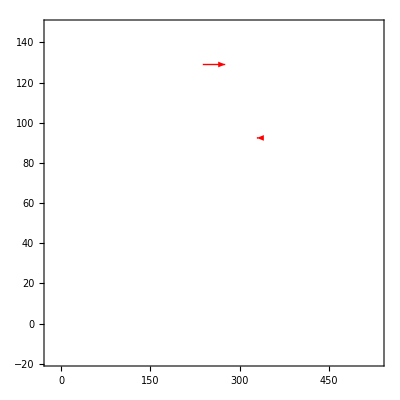

```mathematica
b={{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0
```

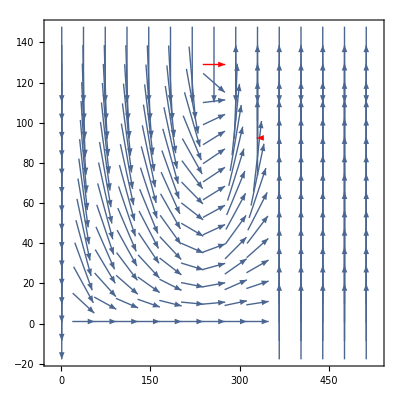

```mathematica
Show[c,d]
```

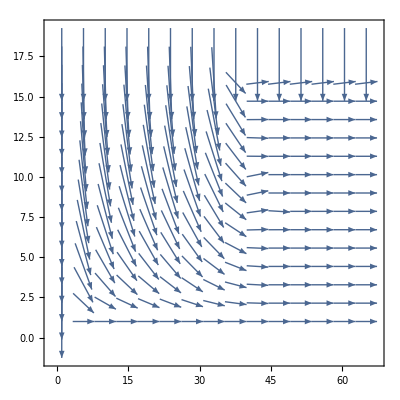

```mathematica
a={{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.707107,-0.707107},{0.495888,-0.868386},{0.358065,-0.933697},{0.269768,-0.962925},{0.210544,-0.977584},{0.168394,-0.985720},{0.136709,-0.990611},{0.111764,-0.993735},{0.091353,-0.995819},{0.074091,-0.997251},{0.059064,-0.998254},{0.045637,-0.998958},{0.033344,-0.999444},{0.021828,-0.999762},{0.010797,-0.999942},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.886626,-0.462488},{0.721559,-0.692353},{0.579686,-0.814840},{0.468278,-0.883581},{0.381855,-0.924222},{0.313973,-0.949432},{0.259496,-0.965744},{0.214695,-0.976681},{0.176932,-0.984223},{0.144332,-0.989529},{0.115536,-0.993303},{0.089534,-0.995984},{0.065551,-0.997849},{0.042969,-0.999076},{0.021271,-0.999774},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.941483,-0.337061},{0.826261,-0.563287},{0.706599,-0.707615},{0.599018,-0.800735},{0.506487,-0.862248},{0.427775,-0.903885},{0.360618,-0.932714},{0.302754,-0.953069},{0.252224,-0.967669},{0.207418,-0.978252},{0.167032,-0.985951},{0.130011,-0.991513},{0.095485,-0.995431},{0.062723,-0.998031},{0.031087,-0.999517},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.963878,-0.266343},{0.880726,-0.473626},{0.782584,-0.622545},{0.685445,-0.728124},{0.595338,-0.803476},{0.513854,-0.857878},{0.440769,-0.897620},{0.375174,-0.926954},{0.315964,-0.948771},{0.262045,-0.965056},{0.212408,-0.977181},{0.166150,-0.986101},{0.122468,-0.992472},{0.080646,-0.996743},{0.040027,-0.999199},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.974887,-0.222701},{0.911802,-0.410630},{0.830521,-0.556988},{0.744129,-0.668036},{0.659232,-0.751940},{0.578699,-0.815541},{0.503500,-0.863995},{0.433667,-0.901073},{0.368795,-0.929511},{0.308283,-0.951295},{0.251464,-0.967867},{0.197663,-0.980270},{0.146228,-0.989251},{0.096534,-0.995330},{0.047984,-0.998848},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.981044,-0.193785},{0.930891,-0.365296},{0.862209,-0.506552},{0.785173,-0.619276},{0.705968,-0.708244},{0.627906,-0.778289},{0.552587,-0.833455},{0.480638,-0.876919},{0.412151,-0.911116},{0.346921,-0.937894},{0.284586,-0.958650},{0.224705,-0.974427},{0.166800,-0.985991},{0.110378,-0.993890},{0.054942,-0.998490},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.984822,-0.173568},{0.943334,-0.331845},{0.884013,-0.467463},{0.814685,-0.579903},{0.740795,-0.671731},{0.665674,-0.746242},{0.591211,-0.806517},{0.518384,-0.855148},{0.447621,-0.894223},{0.379012,-0.925392},{0.312442,-0.949937},{0.247678,-0.968842},{0.184412,-0.982849},{0.122294,-0.992494},{0.060952,-0.998141},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.987304,-0.158843},{0.951843,-0.306587},{0.899536,-0.436847},{0.836438,-0.548061},{0.767219,-0.641386},{0.695029,-0.718982},{0.621847,-0.783139},{0.548846,-0.835923},{0.476671,-0.879082},{0.405623,-0.914041},{0.335782,-0.941940},{0.267088,-0.963672},{0.199388,-0.979921},{0.132474,-0.991186},{0.066100,-0.997813},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.989021,-0.147774},{0.957895,-0.287119},{0.910916,-0.412591},{0.852832,-0.522186},{0.787608,-0.616177},{0.718135,-0.695903},{0.646373,-0.763021},{0.573586,-0.819146},{0.500552,-0.865706},{0.427725,-0.903909},{0.355333,-0.934740},{0.283460,-0.958984},{0.212088,-0.977250},{0.141139,-0.989990},{0.070492,-0.997512},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.990259,-0.139240},{0.962343,-0.271838},{0.919476,-0.393145},{0.865438,-0.501017},{0.803594,-0.595178},{0.736557,-0.676375},{0.666206,-0.745768},{0.593833,-0.804588},{0.520298,-0.853985},{0.446157,-0.894955},{0.371754,-0.928331},{0.297289,-0.954787},{0.222864,-0.974850},{0.148515,-0.988910},{0.074237,-0.997241},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991181,-0.132518},{0.965705,-0.259642},{0.926064,-0.377367},{0.875313,-0.483556},{0.816323,-0.577596},{0.751434,-0.659808},{0.682418,-0.730962},{0.610556,-0.791973},{0.536749,-0.843742},{0.461627,-0.887074},{0.385620,-0.922658},{0.309024,-0.951054},{0.232041,-0.972706},{0.154813,-0.987944},{0.077440,-0.996997},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991887,-0.127121},{0.968310,-0.249750},{0.931242,-0.364402},{0.883191,-0.469013},{0.826617,-0.562765},{0.763613,-0.645674},{0.695831,-0.718205},{0.624517,-0.781012},{0.550590,-0.834776},{0.474725,-0.880134},{0.397422,-0.917636},{0.319055,-0.947736},{0.239911,-0.970795},{0.160226,-0.987080},{0.080197,-0.996779},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992443,-0.122707},{0.970377,-0.241597},{0.935396,-0.353601},{0.889591,-0.456758},{0.835079,-0.550130},{0.773732,-0.633512},{0.707081,-0.707132},{0.636322,-0.771423},{0.562375,-0.826882},{0.485945,-0.873989},{0.407581,-0.913169},{0.327722,-0.944774},{0.246733,-0.969084},{0.164928,-0.986306},{0.082595,-0.996583},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992891,-0.119030},{0.972054,-0.234759},{0.938800,-0.344462},{0.894890,-0.446287},{0.842159,-0.539229},{0.782282,-0.622925},{0.716669,-0.697413},{0.646461,-0.762947},{0.572564,-0.819860},{0.495700,-0.868494},{0.416455,-0.909156},{0.335322,-0.942103},{0.252731,-0.967537},{0.169072,-0.985604},{0.084710,-0.996406},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993260,-0.115904},{0.973447,-0.228914},{0.941651,-0.336590},{0.899370,-0.437188},{0.848203,-0.529671},{0.789646,-0.613562},{0.724997,-0.688752},{0.655333,-0.755340},{0.581538,-0.813519},{0.504340,-0.863505},{0.424352,-0.905497},{0.342113,-0.939659},{0.258107,-0.966116},{0.172793,-0.984958},{0.086612,-0.996242},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993574,-0.113185},{0.974633,-0.223808},{0.944098,-0.329664},{0.903248,-0.429118},{0.853481,-0.521124},{0.796134,-0.605121},{0.732393,-0.680882},{0.663272,-0.748378},{0.589622,-0.807679},{0.512169,-0.858885},{0.431545,-0.902092},{0.348322,-0.937375},{0.263039,-0.964785},{0.176215,-0.984352},{0.088364,-0.996088},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993847,-0.110762},{0.975672,-0.219235},{0.946255,-0.323422},{0.906694,-0.421789},{0.858211,-0.513297},{0.801998,-0.597327},{0.739134,-0.673558},{0.670563,-0.741852},{0.597099,-0.802167},{0.519455,-0.854498},{0.438275,-0.898841},{0.354159,-0.935185},{0.267692,-0.963505},{0.179452,-0.983767},{0.090024,-0.995940},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994092,-0.108539},{0.976609,-0.215024},{0.948212,-0.317639},{0.909845,-0.414948},{0.862573,-0.505932},{0.807452,-0.589933},{0.745458,-0.666553},{0.677458,-0.735561},{0.604223,-0.796815},{0.526444,-0.850210},{0.444769,-0.895646},{0.359820,-0.933022},{0.272222,-0.962235},{0.182612,-0.983185},{0.091647,-0.995792},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994319,-0.106437},{0.977480,-0.211028},{0.950043,-0.312118},{0.912817,-0.408369},{0.866721,-0.498793},{0.812685,-0.582704},{0.751576,-0.659646},{0.684186,-0.729308},{0.611228,-0.791454},{0.533367,-0.845884},{0.451242,-0.892402},{0.365493,-0.930814},{0.276782,-0.960933},{0.185804,-0.982587},{0.093290,-0.995639},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994537,-0.104387},{0.978317,-0.207115},{0.951812,-0.306682},{0.915707,-0.401846},{0.870790,-0.491655},{0.817862,-0.575414},{0.757684,-0.652621},{0.690960,-0.722893},{0.618341,-0.785910},{0.540450,-0.841376},{0.457911,-0.888998},{0.371372,-0.928484},{0.281530,-0.959553},{0.189139,-0.981950},{0.095010,-0.995476},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994751,-0.102325},{0.979144,-0.203165},{0.953572,-0.301164},{0.918605,-0.395178},{0.874902,-0.484301},{0.823140,-0.567839},{0.763967,-0.645255},{0.697991,-0.716106},{0.625787,-0.779994},{0.547925,-0.836527},{0.465000,-0.885311},{0.377661,-0.925944},{0.286636,-0.958040},{0.192739,-0.981250},{0.096871,-0.995297},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994968,-0.100192},{0.979986,-0.199065},{0.955372,-0.295406},{0.921587,-0.388172},{0.879168,-0.476512},{0.828665,-0.559745},{0.770605,-0.637313},{0.705488,-0.708722},{0.633798,-0.773499},{0.556036,-0.831158},{0.472753,-0.881195},{0.384586,-0.923089},{0.292290,-0.956330},{0.196742,-0.980455},{0.098947,-0.995093},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995193,-0.097930},{0.980862,-0.194704},{0.957253,-0.289250},{0.924727,-0.380631},{0.883696,-0.468062},{0.834579,-0.550888},{0.777776,-0.628541},{0.713664,-0.700488},{0.642619,-0.766186},{0.565048,-0.825058},{0.481441,-0.876479},{0.392406,-0.919792},{0.298714,-0.954343},{0.201313,-0.979527},{0.101323,-0.994854},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995431,-0.095485},{0.981789,-0.189975},{0.959256,-0.282540},{0.928090,-0.372356},{0.888583,-0.458715},{0.841021,-0.541003},{0.785662,-0.618656},{0.722746,-0.691114},{0.652514,-0.757776},{0.575260,-0.817971},{0.491377,-0.870947},{0.401426,-0.915891},{0.306179,-0.951974},{0.206654,-0.978414},{0.104109,-0.994566},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995685,-0.092801},{0.982782,-0.184768},{0.961411,-0.275116},{0.931735,-0.363140},{0.893923,-0.448221},{0.848122,-0.529800},{0.794443,-0.607339},{0.732966,-0.680266},{0.663774,-0.747933},{0.587007,-0.809582},{0.502932,-0.864326},{0.412019,-0.911175},{0.315020,-0.949085},{0.213020,-0.977048},{0.107445,-0.994211},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995957,-0.089827},{0.983853,-0.178980},{0.963746,-0.266820},{0.935710,-0.352771},{0.899795,-0.436314},{0.856007,-0.516964},{0.804297,-0.594228},{0.744567,-0.667547},{0.676713,-0.736247},{0.600678,-0.799491},{0.516546,-0.856260},{0.424646,-0.905359},{0.325669,-0.945484},{0.220753,-0.975330},{0.111518,-0.993762},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996251,-0.086512},{0.985008,-0.172507},{0.966280,-0.257495},{0.940052,-0.341032},{0.906263,-0.422714},{0.864781,-0.502149},{0.815389,-0.578914},{0.757795,-0.652492},{0.691670,-0.722213},{0.616712,-0.787189},{0.532751,-0.846272},{0.439896,-0.898049},{0.338698,-0.940895},{0.230313,-0.973117},{0.116588,-0.993180},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996565,-0.082810},{0.986251,-0.165255},{0.969018,-0.246990},{0.944779,-0.327710},{0.913369,-0.407133},{0.874524,-0.484982},{0.827861,-0.560933},{0.772882,-0.634550},{0.709000,-0.705208},{0.635608,-0.772012},{0.552193,-0.833716},{0.458520,-0.888684},{0.354877,-0.934913},{0.242352,-0.970188},{0.123034,-0.992402},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996900,-0.078682},{0.987576,-0.157141},{0.971954,-0.235171},{0.949884,-0.312601},{0.921117,-0.389285},{0.885271,-0.465075},{0.841807,-0.539778},{0.790020,-0.613082},{0.729043,-0.684468},{0.657905,-0.753101},{0.575638,-0.817705},{0.481491,-0.876451},{0.375276,-0.926913},{0.257823,-0.966192},{0.131428,-0.991326},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997251,-0.074101},{0.988972,-0.148102},{0.975063,-0.221927},{0.955333,-0.295532},{0.929467,-0.368905},{0.896994,-0.442042},{0.857245,-0.514909},{0.809323,-0.587364},{0.752084,-0.659068},{0.684147,-0.729344},{0.603971,-0.797006},{0.510062,-0.860138},{0.401401,-0.915902},{0.278174,-0.960531},{0.142690,-0.989767},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997613,-0.069051},{0.990418,-0.138105},{0.978301,-0.207189},{0.961051,-0.276372},{0.938319,-0.345771},{0.909579,-0.415530},{0.874076,-0.485789},{0.830768,-0.556619},{0.778268,-0.627932},{0.714792,-0.699337},{0.638139,-0.769921},{0.545804,-0.837913},{0.435405,-0.900235},{0.305709,-0.952125},{0.158403,-0.987375},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997979,-0.063539},{0.991883,-0.127151},{0.981602,-0.190940},{0.966925,-0.255062},{0.947504,-0.319743},{0.922806,-0.385265},{0.892046,-0.451944},{0.854117,-0.520081},{0.807485,-0.589888},{0.750053,-0.661378},{0.678982,-0.734155},{0.590557,-0.806996},{0.480336,-0.877085},{0.344233,-0.938884},{0.181528,-0.983386},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998340,-0.057596},{0.993331,-0.115294},{0.984880,-0.173238},{0.972802,-0.231638},{0.956785,-0.290797},{0.936334,-0.351112},{0.910708,-0.413050},{0.878839,-0.477118},{0.839205,-0.543815},{0.789620,-0.613596},{0.726864,-0.686781},{0.646110,-0.763245},{0.540283,-0.841483},{0.400208,-0.916424},{0.218196,-0.975905},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998684,-0.051278},{0.994718,-0.102643},{0.988035,-0.154227},{0.978499,-0.206254},{0.965860,-0.259066},{0.949709,-0.313135},{0.929414,-0.369038},{0.904057,-0.427412},{0.872325,-0.488926},{0.832305,-0.554318},{0.780991,-0.624543},{0.713243,-0.700917},{0.619814,-0.784749},{0.484373,-0.874862},{0.282549,-0.959253},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999001,-0.044678},{0.995998,-0.089371},{0.990961,-0.134152},{0.983812,-0.179204},{0.974390,-0.224865},{0.962397,-0.271646},{0.947353,-0.320190},{0.928564,-0.371173},{0.905100,-0.425198},{0.875714,-0.482830},{0.838478,-0.544935},{0.789687,-0.613510},{0.720972,-0.692964},{0.611694,-0.791095},{0.409843,-0.912156},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999281,-0.037919},{0.997129,-0.075725},{0.993553,-0.113368},{0.988544,-0.150931},{0.982034,-0.188702},{0.973846,-0.227211},{0.963648,-0.267176},{0.950973,-0.309274},{0.935320,-0.353803},{0.916303,-0.400486},{0.893745,-0.448576},{0.867289,-0.497804},{0.835034,-0.550199},{0.787771,-0.615969},{0.676948,-0.736031},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999514,-0.031164},{0.998075,-0.062025},{0.995727,-0.092344},{0.992526,-0.122032},{0.988493,-0.151264},{0.983557,-0.180598},{0.977499,-0.210942},{0.969988,-0.243154},{0.960810,-0.277208},{0.950234,-0.311538},{0.939624,-0.342208},{0.931782,-0.363018},{0.932406,-0.361413},{0.954703,-0.297560},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999697,-0.024608},{0.998815,-0.048669},{0.997428,-0.071680},{0.995641,-0.093272},{0.993549,-0.113408},{0.991161,-0.132667},{0.988314,-0.152431},{0.984688,-0.174324},{0.980116,-0.198423},{0.974974,-0.222318},{0.971161,-0.238423},{0.971471,-0.237159},{0.978570,-0.205914},{0.991929,-0.126795},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999829,-0.018477},{0.999347,-0.036129},{0.998641,-0.052113},{0.997844,-0.065632},{0.997092,-0.076204},{0.996441,-0.084292},{0.995743,-0.092173},{0.994624,-0.103552},{0.992853,-0.119344},{0.990400,-0.138233},{0.989209,-0.146508},{0.991200,-0.132371},{0.996278,-0.086201},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999915,-0.013008},{0.999689,-0.024928},{0.999403,-0.034535},{0.999183,-0.040403},{0.999153,-0.041139},{0.999335,-0.036466},{0.999554,-0.029850},{0.999546,-0.030129},{0.999249,-0.038747},{0.998017,-0.062950},{0.997392,-0.072177},{0.998608,-0.052738},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999965,-0.008411},{0.999879,-0.015582},{0.999801,-0.019958},{0.999813,-0.019325},{0.999944,-0.010610},{0.999959,0.009063},{0.999343,0.036243},{0.998849,0.047959},{0.998660,0.051753},{1.000000,-0.000271},{0.999789,-0.020523},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999988,-0.004802},{0.999964,-0.008450},{0.999957,-0.009327},{0.999989,-0.004602},{0.999938,0.011158},{0.998865,0.047632},{0.993802,0.111164},{0.991637,0.129056},{0.983442,0.181225},{0.999272,0.038148},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999998,-0.002108},{0.999994,-0.003494},{0.999995,-0.003033},{0.999999,0.001685},{0.999854,0.017101},{0.997951,0.063988},{0.976642,0.214873},{0.984049,0.177900},{0.894427,0.447214},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{0.894427,0.447214},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}}};
c=ListVectorPlot[a]
```

```mathematica
d={{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}};
e=ListVectorPlot[d,VectorStyle->Red]
```

-Graphics-

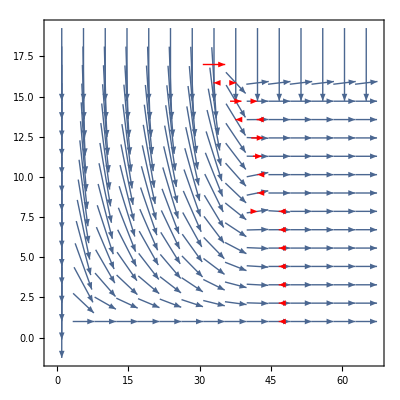

```mathematica
Show[c,e]
```

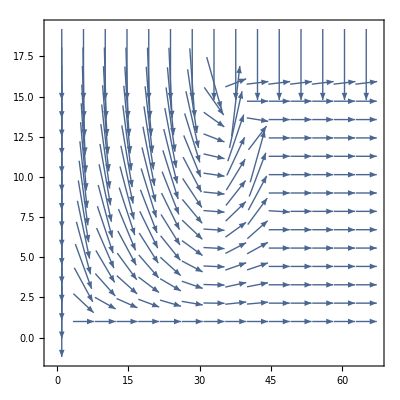

```mathematica
a={{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.707107,-0.707107},{0.496401,-0.868094},{0.358914,-0.933370},{0.270830,-0.962627},{0.211740,-0.977326},{0.169667,-0.985501},{0.138009,-0.990431},{0.113047,-0.993590},{0.092576,-0.995706},{0.075217,-0.997167},{0.060059,-0.998195},{0.046471,-0.998920},{0.033992,-0.999422},{0.022270,-0.999752},{0.011022,-0.999939},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.886892,-0.461976},{0.722385,-0.691491},{0.581062,-0.813859},{0.470104,-0.882611},{0.384013,-0.923328},{0.316347,-0.948643},{0.261976,-0.965074},{0.217180,-0.976132},{0.179329,-0.983789},{0.146556,-0.989202},{0.117511,-0.993072},{0.091196,-0.995833},{0.066846,-0.997763},{0.043856,-0.999038},{0.021721,-0.999764},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.941787,-0.336211},{0.827224,-0.561873},{0.708291,-0.705920},{0.601377,-0.798966},{0.509385,-0.860539},{0.431061,-0.902323},{0.364132,-0.931347},{0.306338,-0.951923},{0.255728,-0.966749},{0.210702,-0.977550},{0.169972,-0.985449},{0.132498,-0.991183},{0.097431,-0.995242},{0.064059,-0.997946},{0.031767,-0.999495},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.964189,-0.265217},{0.881769,-0.471682},{0.784506,-0.620122},{0.688222,-0.725500},{0.598853,-0.800859},{0.517938,-0.855418},{0.445223,-0.895420},{0.379789,-0.925073},{0.320533,-0.947237},{0.266371,-0.963870},{0.216311,-0.976324},{0.169473,-0.985535},{0.125080,-0.992147},{0.082444,-0.996596},{0.040944,-0.999161},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.975204,-0.221310},{0.912913,-0.408154},{0.832643,-0.553811},{0.747284,-0.664504},{0.663319,-0.748337},{0.583538,-0.812086},{0.508861,-0.860849},{0.439297,-0.898342},{0.374431,-0.927255},{0.313669,-0.949533},{0.256359,-0.966582},{0.201855,-0.979415},{0.149537,-0.988756},{0.098820,-0.995105},{0.049151,-0.998791},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.981372,-0.192116},{0.932076,-0.362262},{0.864534,-0.502574},{0.788708,-0.614767},{0.710632,-0.703564},{0.633513,-0.773732},{0.558881,-0.829248},{0.487321,-0.873223},{0.418905,-0.908030},{0.353425,-0.935463},{0.290537,-0.956864},{0.229828,-0.973231},{0.170859,-0.985295},{0.113190,-0.993573},{0.056381,-0.998409},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.985168,-0.171594},{0.944607,-0.328204},{0.886561,-0.462611},{0.818630,-0.574321},{0.746078,-0.665858},{0.672107,-0.740454},{0.598510,-0.801115},{0.526207,-0.850356},{0.455590,-0.890190},{0.386738,-0.922190},{0.319551,-0.947569},{0.253825,-0.967250},{0.189300,-0.981919},{0.125689,-0.992070},{0.062691,-0.998033},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.987674,-0.156526},{0.953224,-0.302266},{0.902342,-0.431020},{0.840844,-0.541278},{0.773192,-0.634172},{0.702380,-0.711803},{0.630266,-0.776380},{0.557941,-0.829881},{0.485999,-0.873960},{0.414720,-0.909949},{0.344193,-0.938899},{0.274390,-0.961619},{0.205213,-0.978717},{0.136529,-0.990636},{0.068179,-0.997673},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.989422,-0.145063},{0.959407,-0.282026},{0.914025,-0.405657},{0.857768,-0.514037},{0.794370,-0.607435},{0.726532,-0.687133},{0.656065,-0.754704},{0.584128,-0.811662},{0.511429,-0.859325},{0.438388,-0.898786},{0.365235,-0.930915},{0.292086,-0.956392},{0.218989,-0.975727},{0.145952,-0.989292},{0.072963,-0.997335},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.990699,-0.136074},{0.964013,-0.265855},{0.922942,-0.384940},{0.870991,-0.491300},{0.811267,-0.584676},{0.746159,-0.665768},{0.677367,-0.735646},{0.606046,-0.795430},{0.532966,-0.846137},{0.458633,-0.888626},{0.383385,-0.923589},{0.307454,-0.951563},{0.231016,-0.972950},{0.154210,-0.988038},{0.077165,-0.997018},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991668,-0.128822},{0.967564,-0.252626},{0.929949,-0.367688},{0.881587,-0.472021},{0.825056,-0.565051},{0.762437,-0.647062},{0.695286,-0.718734},{0.624714,-0.780854},{0.551505,-0.834171},{0.476220,-0.879326},{0.399272,-0.916832},{0.320991,-0.947082},{0.241660,-0.970361},{0.161545,-0.986865},{0.080904,-0.996722},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992431,-0.122805},{0.970393,-0.241530},{0.935621,-0.353007},{0.890308,-0.455359},{0.836586,-0.547835},{0.776250,-0.630425},{0.710691,-0.703504},{0.640949,-0.767584},{0.567793,-0.823172},{0.491805,-0.870705},{0.413455,-0.910524},{0.333148,-0.942875},{0.251264,-0.967919},{0.168184,-0.985756},{0.084296,-0.996441},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993053,-0.117667},{0.972723,-0.231968},{0.940354,-0.340198},{0.897692,-0.440624},{0.846491,-0.532402},{0.788277,-0.615320},{0.724272,-0.689514},{0.655422,-0.755263},{0.582456,-0.812862},{0.505958,-0.862558},{0.426428,-0.904521},{0.344334,-0.938847},{0.260143,-0.965570},{0.174343,-0.984685},{0.087449,-0.996169},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993579,-0.113140},{0.974708,-0.223481},{0.944432,-0.328707},{0.904138,-0.427241},{0.855254,-0.518209},{0.799055,-0.601258},{0.736590,-0.676340},{0.668694,-0.743538},{0.596036,-0.802958},{0.519179,-0.854665},{0.438639,-0.898663},{0.354930,-0.934893},{0.268595,-0.963253},{0.180227,-0.983625},{0.090467,-0.995899},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994040,-0.109020},{0.976459,-0.215704},{0.948065,-0.318076},{0.909949,-0.414720},{0.863253,-0.504771},{0.809016,-0.587786},{0.748111,-0.663574},{0.681246,-0.732055},{0.609010,-0.793163},{0.531925,-0.846791},{0.450504,-0.892774},{0.365294,-0.930892},{0.276905,-0.960897},{0.186034,-0.982543},{0.093453,-0.995624},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994458,-0.105139},{0.978057,-0.208336},{0.951414,-0.307916},{0.915364,-0.402627},{0.870796,-0.491645},{0.818524,-0.574473},{0.759236,-0.650815},{0.693503,-0.720453},{0.621812,-0.783167},{0.544622,-0.838681},{0.462422,-0.886660},{0.375777,-0.926710},{0.285359,-0.958421},{0.191966,-0.981402},{0.096511,-0.995332},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994850,-0.101358},{0.979567,-0.201119},{0.954602,-0.297884},{0.920573,-0.390569},{0.878135,-0.478412},{0.827884,-0.560899},{0.770320,-0.637658},{0.705854,-0.708357},{0.634851,-0.772635},{0.557683,-0.830054},{0.474790,-0.880099},{0.386739,-0.922189},{0.294253,-0.955728},{0.198235,-0.980155},{0.099751,-0.995012},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995230,-0.097556},{0.981036,-0.193827},{0.957729,-0.287671},{0.925733,-0.378178},{0.885484,-0.464669},{0.837366,-0.546642},{0.781680,-0.623680},{0.718661,-0.695360},{0.648523,-0.761195},{0.571520,-0.820588},{0.488018,-0.872833},{0.398559,-0.917143},{0.303907,-0.952702},{0.205073,-0.978747},{0.103297,-0.994651},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995608,-0.093624},{0.982502,-0.186251},{0.960874,-0.276986},{0.930969,-0.365097},{0.893023,-0.450012},{0.847205,-0.531267},{0.793608,-0.608429},{0.732270,-0.681014},{0.663222,-0.748423},{0.586562,-0.809904},{0.502544,-0.864551},{0.411655,-0.911340},{0.314683,-0.949197},{0.212748,-0.977107},{0.107290,-0.994228},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995990,-0.089463},{0.983994,-0.178199},{0.964096,-0.265553},{0.936383,-0.350979},{0.900899,-0.434030},{0.857603,-0.514312},{0.806370,-0.591412},{0.747013,-0.664810},{0.679343,-0.733820},{0.603260,-0.797545},{0.518851,-0.854865},{0.426504,-0.904486},{0.327002,-0.945024},{0.221578,-0.975143},{0.111901,-0.993719},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996383,-0.084980},{0.985532,-0.169490},{0.967438,-0.253106},{0.942049,-0.335476},{0.909227,-0.416300},{0.868729,-0.495287},{0.820200,-0.572077},{0.763204,-0.646158},{0.697290,-0.716789},{0.622096,-0.782941},{0.537479,-0.843277},{0.443661,-0.896195},{0.341376,-0.939927},{0.231956,-0.972726},{0.117347,-0.993091},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996787,-0.080092},{0.987124,-0.159956},{0.970923,-0.239392},{0.948008,-0.318246},{0.918083,-0.396388},{0.880707,-0.473661},{0.835292,-0.549806},{0.781130,-0.624369},{0.717460,-0.696600},{0.643587,-0.765373},{0.559044,-0.829138},{0.463792,-0.885944},{0.358436,-0.933554},{0.244385,-0.969678},{0.123906,-0.992294},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997204,-0.074726},{0.988770,-0.149445},{0.974549,-0.224173},{0.954267,-0.298956},{0.927490,-0.373849},{0.893598,-0.448868},{0.851776,-0.523907},{0.801025,-0.598631},{0.740229,-0.672355},{0.668273,-0.743916},{0.584244,-0.811578},{0.487699,-0.873012},{0.378986,-0.925403},{0.259524,-0.965737},{0.131953,-0.991256},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997629,-0.068819},{0.990456,-0.137829},{0.978290,-0.207240},{0.960785,-0.277295},{0.937403,-0.348247},{0.907377,-0.420317},{0.869683,-0.493610},{0.823032,-0.567995},{0.765910,-0.642948},{0.696691,-0.717371},{0.613860,-0.789415},{0.516361,-0.856371},{0.404065,-0.914730},{0.278267,-0.960504},{0.142009,-0.989865},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998056,-0.062330},{0.992155,-0.125013},{0.982087,-0.188429},{0.967467,-0.252999},{0.947695,-0.319177},{0.921905,-0.387416},{0.888906,-0.458091},{0.847141,-0.531369},{0.794685,-0.607022},{0.729315,-0.684178},{0.648726,-0.761022},{0.550953,-0.834536},{0.435037,-0.900413},{0.301854,-0.953354},{0.154823,-0.987942},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998473,-0.055241},{0.993826,-0.110952},{0.985848,-0.167641},{0.974156,-0.225877},{0.958139,-0.286303},{0.936893,-0.349616},{0.909133,-0.416507},{0.873101,-0.487540},{0.826490,-0.562952},{0.766433,-0.642325},{0.689642,-0.724151},{0.592850,-0.805313},{0.473693,-0.880690},{0.332055,-0.943260},{0.171519,-0.985181},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998868,-0.047565},{0.995414,-0.095661},{0.989451,-0.144867},{0.980633,-0.195857},{0.968395,-0.249422},{0.951874,-0.306489},{0.929793,-0.368084},{0.900309,-0.435252},{0.860846,-0.508865},{0.807934,-0.589272},{0.737172,-0.675705},{0.643534,-0.765418},{0.522372,-0.852718},{0.371462,-0.928448},{0.193864,-0.981028},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999225,-0.039357},{0.996856,-0.079237},{0.992747,-0.120225},{0.986621,-0.163030},{0.978016,-0.208532},{0.966191,-0.257828},{0.949999,-0.312253},{0.927689,-0.373354},{0.896631,-0.442778},{0.852965,-0.521968},{0.791235,-0.611513},{0.704277,-0.709925},{0.583980,-0.811768},{0.423942,-0.905689},{0.224781,-0.974409},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999528,-0.030715},{0.998084,-0.061870},{0.995574,-0.093980},{0.991813,-0.127702},{0.986474,-0.163915},{0.979015,-0.203788},{0.968541,-0.248856},{0.953597,-0.301087},{0.931826,-0.362906},{0.899422,-0.437082},{0.850332,-0.526246},{0.775330,-0.631556},{0.661649,-0.749813},{0.495263,-0.868743},{0.269430,-0.963020},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999763,-0.021788},{0.999038,-0.043856},{0.997782,-0.066565},{0.995903,-0.090432},{0.993224,-0.116219},{0.989428,-0.145023},{0.983959,-0.178395},{0.975839,-0.218490},{0.963344,-0.268270},{0.943379,-0.331716},{0.910331,-0.413880},{0.854070,-0.520159},{0.757159,-0.653230},{0.593519,-0.804820},{0.337524,-0.941317},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999918,-0.012773},{0.999672,-0.025593},{0.999255,-0.038590},{0.998645,-0.052050},{0.997786,-0.066500},{0.996566,-0.082807},{0.994755,-0.102289},{0.991914,-0.126913},{0.987179,-0.159614},{0.978793,-0.204853},{0.963010,-0.269466},{0.931561,-0.363584},{0.865975,-0.500087},{0.727082,-0.686550},{0.448238,-0.893914},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999992,-0.003909},{0.999971,-0.007571},{0.999941,-0.010818},{0.999907,-0.013630},{0.999869,-0.016211},{0.999819,-0.019050},{0.999735,-0.023006},{0.999567,-0.029428},{0.999182,-0.040447},{0.998222,-0.059604},{0.995646,-0.093213},{0.988213,-0.153086},{0.965217,-0.261450},{0.889787,-0.456376},{0.636747,-0.771073},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999990,0.004533},{0.999953,0.009652},{0.999874,0.015874},{0.999722,0.023567},{0.999459,0.032902},{0.999039,0.043826},{0.998427,0.056066},{0.997605,0.069163},{0.996596,0.082436},{0.995504,0.094715},{0.994631,0.103482},{0.994723,0.102599},{0.997036,0.076932},{0.999976,-0.006991},{0.981956,-0.189108},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999925,0.012261},{0.999675,0.025483},{0.999177,0.040551},{0.998305,0.058204},{0.996877,0.078976},{0.994661,0.103198},{0.991368,0.131107},{0.986615,0.163067},{0.979821,0.199879},{0.969999,0.243110},{0.955394,0.295335},{0.932980,0.359927},{0.898876,0.438203},{0.859860,0.510530},{0.877574,0.479442},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999820,0.018982},{0.999227,0.039320},{0.998058,0.062288},{0.996033,0.088982},{0.992744,0.120244},{0.987655,0.156642},{0.980074,0.198632},{0.969031,0.246940},{0.952949,0.303131},{0.928917,0.370289},{0.891088,0.453831},{0.826632,0.562743},{0.701396,0.712772},{0.396976,0.917829},{0.371391,0.928477},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999702,0.024411},{0.998720,0.050588},{0.996778,0.080204},{0.993398,0.114718},{0.987881,0.155212},{0.979326,0.202288},{0.966623,0.256202},{0.948305,0.317362},{0.922077,0.387006},{0.883830,0.467807},{0.825818,0.563936},{0.734845,0.678235},{0.597052,0.802203},{0.422257,0.906476},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999600,0.028278},{0.998273,0.058738},{0.995621,0.093482},{0.990932,0.134365},{0.983168,0.182702},{0.971031,0.238955},{0.953073,0.302741},{0.927643,0.373468},{0.892434,0.451178},{0.843543,0.537062},{0.773074,0.634316},{0.664715,0.747097},{0.483894,0.875126},{0.447214,0.894427},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999540,0.030332},{0.997997,0.063258},{0.994851,0.101344},{0.989144,0.146946},{0.979439,0.201743},{0.963969,0.266016},{0.941032,0.338318},{0.909157,0.416453},{0.866733,0.498773},{0.812003,0.583654},{0.740949,0.671562},{0.644539,0.764571},{0.519744,0.854322},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999539,0.030357},{0.997971,0.063671},{0.994681,0.103002},{0.988472,0.151405},{0.977423,0.211293},{0.959111,0.283029},{0.931545,0.363626},{0.893773,0.448520},{0.844732,0.535190},{0.786228,0.617936},{0.721037,0.692897},{0.633989,0.773342},{0.554700,0.832050},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999603,0.028190},{0.998225,0.059563},{0.995222,0.097640},{0.989223,0.146418},{0.977743,0.209806},{0.957257,0.289239},{0.925182,0.379524},{0.882080,0.471099},{0.824784,0.565448},{0.758508,0.651663},{0.707107,0.707107},{0.707107,0.707107},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999717,0.023776},{0.998715,0.050680},{0.996426,0.084476},{0.991484,0.130227},{0.980898,0.194525},{0.959181,0.282793},{0.921710,0.387879},{0.875946,0.482408},{0.807964,0.589232},{0.707107,0.707107},{0.707107,0.707107},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999851,0.017253},{0.999311,0.037120},{0.998010,0.063060},{0.994915,0.100717},{0.987074,0.160265},{0.966102,0.258161},{0.917556,0.397606},{0.879776,0.475388},{0.811242,0.584710},{0.707107,0.707107},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999959,0.009061},{0.999807,0.019649},{0.999423,0.033977},{0.998407,0.056417},{0.995182,0.098042},{0.981110,0.193451},{0.894427,0.447214},{0.894427,0.447214},{0.894427,0.447214},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{0.894427,0.447214},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}}};
c=ListVectorPlot[a]
```

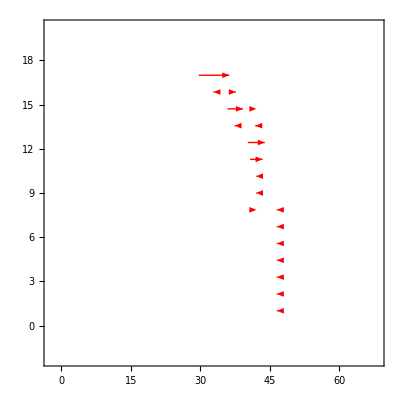

```mathematica
b={{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}};
d=ListVectorPlot[b, VectorStyle->Red, VectorScale->Large]
```

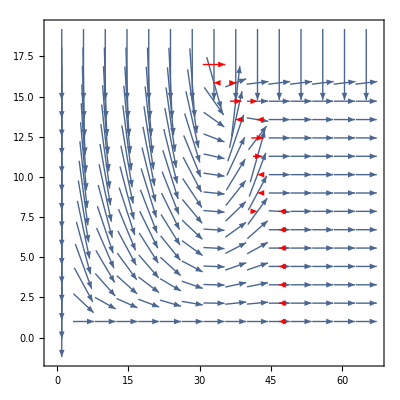

```mathematica
Show[c,d]
```

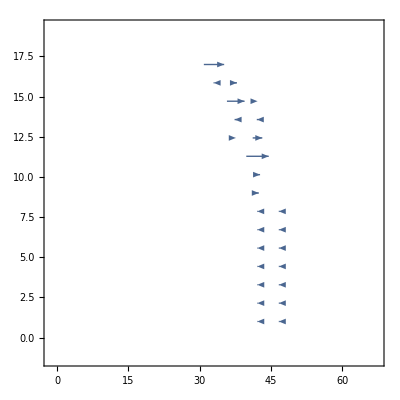

```mathematica
b={{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1.0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{1.0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}};
d=ListVectorPlot[b]
```

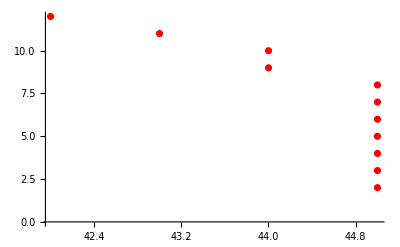

```mathematica
d=ListPlot[{{45,2},{45,3},{45,4},{45,5},{45,6},{45,7},{45,8},{44,9},{44,10},{43,11},{42,12}}, PlotStyle->Red]
```

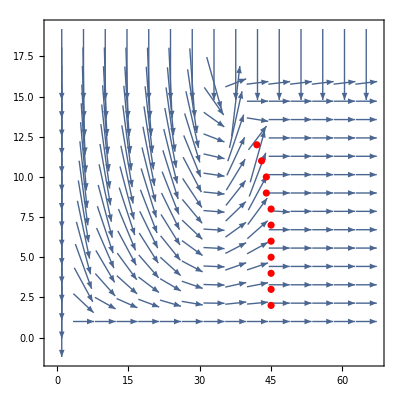

```mathematica
Show[c,d]
```

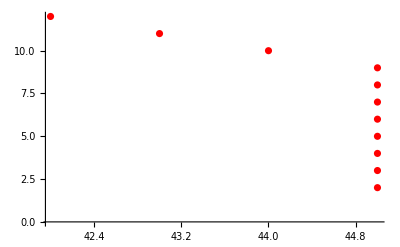

```mathematica
d=ListPlot[{{45,2},{45,3},{45,4},{45,5},{45,6},{45,7},{45,8},{45,9},{44,10},{43,11},{42,12}}, PlotStyle->Red]
```

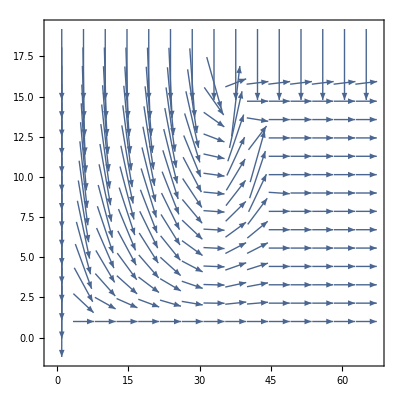

```mathematica
a={{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.707107,-0.707107},{0.496403,-0.868092},{0.358918,-0.933369},{0.270834,-0.962626},{0.211745,-0.977325},{0.169672,-0.985501},{0.138014,-0.990430},{0.113051,-0.993589},{0.092580,-0.995705},{0.075221,-0.997167},{0.060063,-0.998195},{0.046474,-0.998920},{0.033994,-0.999422},{0.022272,-0.999752},{0.011022,-0.999939},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.886893,-0.461974},{0.722388,-0.691488},{0.581067,-0.813856},{0.470111,-0.882608},{0.384021,-0.923324},{0.316356,-0.948641},{0.261985,-0.965072},{0.217189,-0.976130},{0.179338,-0.983788},{0.146564,-0.989201},{0.117518,-0.993071},{0.091202,-0.995832},{0.066851,-0.997763},{0.043859,-0.999038},{0.021723,-0.999764},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.941788,-0.336208},{0.827227,-0.561868},{0.708297,-0.705914},{0.601385,-0.798959},{0.509396,-0.860533},{0.431073,-0.902317},{0.364145,-0.931342},{0.306351,-0.951919},{0.255740,-0.966746},{0.210713,-0.977548},{0.169982,-0.985447},{0.132507,-0.991182},{0.097438,-0.995242},{0.064064,-0.997946},{0.031769,-0.999495},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.964190,-0.265213},{0.881773,-0.471675},{0.784513,-0.620113},{0.688232,-0.725490},{0.598866,-0.800849},{0.517952,-0.855410},{0.445238,-0.895412},{0.379805,-0.925067},{0.320550,-0.947232},{0.266387,-0.963866},{0.216325,-0.976321},{0.169484,-0.985533},{0.125089,-0.992146},{0.082451,-0.996595},{0.040947,-0.999161},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.975205,-0.221305},{0.912917,-0.408145},{0.832650,-0.553799},{0.747296,-0.664492},{0.663333,-0.748324},{0.583555,-0.812074},{0.508880,-0.860837},{0.439317,-0.898332},{0.374451,-0.927247},{0.313688,-0.949526},{0.256376,-0.966577},{0.201870,-0.979412},{0.149549,-0.988754},{0.098828,-0.995105},{0.049155,-0.998791},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.981373,-0.192110},{0.932080,-0.362252},{0.864542,-0.502560},{0.788721,-0.614751},{0.710649,-0.703547},{0.633533,-0.773715},{0.558904,-0.829233},{0.487345,-0.873209},{0.418929,-0.908019},{0.353448,-0.935454},{0.290558,-0.956857},{0.229846,-0.973227},{0.170874,-0.985293},{0.113200,-0.993572},{0.056386,-0.998409},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.985169,-0.171587},{0.944611,-0.328191},{0.886570,-0.462594},{0.818644,-0.574301},{0.746097,-0.665837},{0.672130,-0.740433},{0.598536,-0.801096},{0.526235,-0.850339},{0.455618,-0.890175},{0.386766,-0.922178},{0.319576,-0.947560},{0.253847,-0.967244},{0.189318,-0.981916},{0.125701,-0.992068},{0.062697,-0.998033},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.987675,-0.156517},{0.953229,-0.302250},{0.902352,-0.430999},{0.840860,-0.541253},{0.773214,-0.634146},{0.702406,-0.711777},{0.630296,-0.776355},{0.557973,-0.829859},{0.486032,-0.873941},{0.414752,-0.909934},{0.344223,-0.938888},{0.274416,-0.961611},{0.205234,-0.978713},{0.136543,-0.990634},{0.068187,-0.997673},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.989424,-0.145054},{0.959412,-0.282007},{0.914037,-0.405632},{0.857786,-0.514008},{0.794394,-0.607403},{0.726562,-0.687101},{0.656100,-0.754674},{0.584165,-0.811635},{0.511468,-0.859302},{0.438426,-0.898767},{0.365270,-0.930902},{0.292117,-0.956383},{0.219014,-0.975722},{0.145969,-0.989289},{0.072972,-0.997334},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.990700,-0.136062},{0.964019,-0.265834},{0.922954,-0.384910},{0.871010,-0.491265},{0.811294,-0.584639},{0.746193,-0.665730},{0.677406,-0.735609},{0.606089,-0.795397},{0.533011,-0.846108},{0.458677,-0.888603},{0.383426,-0.923572},{0.307490,-0.951551},{0.231044,-0.972943},{0.154230,-0.988035},{0.077175,-0.997018},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991669,-0.128808},{0.967571,-0.252601},{0.929963,-0.367654},{0.881609,-0.471980},{0.825087,-0.565006},{0.762476,-0.647017},{0.695331,-0.718690},{0.624764,-0.780814},{0.551557,-0.834137},{0.476271,-0.879298},{0.399320,-0.916811},{0.321033,-0.947068},{0.241694,-0.970353},{0.161568,-0.986862},{0.080916,-0.996721},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992433,-0.122790},{0.970401,-0.241500},{0.935636,-0.352966},{0.890333,-0.455310},{0.836622,-0.547781},{0.776294,-0.630370},{0.710743,-0.703451},{0.641007,-0.767535},{0.567853,-0.823130},{0.491865,-0.870671},{0.413511,-0.910499},{0.333197,-0.942857},{0.251304,-0.967908},{0.168212,-0.985751},{0.084310,-0.996440},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993055,-0.117649},{0.972732,-0.231933},{0.940371,-0.340150},{0.897721,-0.440565},{0.846532,-0.532338},{0.788328,-0.615255},{0.724333,-0.689450},{0.655489,-0.755204},{0.582526,-0.812812},{0.506028,-0.862517},{0.426494,-0.904490},{0.344392,-0.938826},{0.260190,-0.965557},{0.174376,-0.984679},{0.087466,-0.996168},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993581,-0.113119},{0.974718,-0.223440},{0.944452,-0.328650},{0.904170,-0.427172},{0.855300,-0.518133},{0.799113,-0.601180},{0.736660,-0.676264},{0.668772,-0.743468},{0.596118,-0.802897},{0.519261,-0.854616},{0.438716,-0.898626},{0.354998,-0.934867},{0.268650,-0.963238},{0.180265,-0.983618},{0.090487,-0.995898},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994042,-0.108995},{0.976469,-0.215656},{0.948088,-0.318009},{0.909986,-0.414638},{0.863306,-0.504681},{0.809084,-0.587693},{0.748192,-0.663483},{0.681336,-0.731971},{0.609105,-0.793089},{0.532021,-0.846731},{0.450595,-0.892729},{0.365373,-0.930861},{0.276970,-0.960879},{0.186079,-0.982535},{0.093476,-0.995622},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994461,-0.105110},{0.978069,-0.208279},{0.951439,-0.307837},{0.915406,-0.402531},{0.870856,-0.491538},{0.818601,-0.574362},{0.759330,-0.650706},{0.693608,-0.720353},{0.621923,-0.783078},{0.544734,-0.838609},{0.462528,-0.886605},{0.375871,-0.926672},{0.285435,-0.958398},{0.192019,-0.981391},{0.096538,-0.995329},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994853,-0.101324},{0.979580,-0.201053},{0.954631,-0.297791},{0.920622,-0.390456},{0.878204,-0.478285},{0.827974,-0.560767},{0.770427,-0.637528},{0.705976,-0.708236},{0.634980,-0.772528},{0.557813,-0.829967},{0.474914,-0.880032},{0.386849,-0.922143},{0.294342,-0.955700},{0.198298,-0.980142},{0.099784,-0.995009},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995234,-0.097516},{0.981051,-0.193749},{0.957762,-0.287561},{0.925788,-0.378043},{0.885563,-0.464519},{0.837469,-0.546485},{0.781804,-0.623524},{0.718802,-0.695215},{0.648673,-0.761067},{0.571672,-0.820482},{0.488163,-0.872752},{0.398688,-0.917087},{0.304012,-0.952668},{0.205147,-0.978731},{0.103335,-0.994647},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995612,-0.093577},{0.982519,-0.186160},{0.960911,-0.276857},{0.931032,-0.364938},{0.893113,-0.449833},{0.847322,-0.531079},{0.793751,-0.608243},{0.732432,-0.680840},{0.663396,-0.748269},{0.586739,-0.809776},{0.502714,-0.864453},{0.411807,-0.911271},{0.314807,-0.949156},{0.212836,-0.977088},{0.107335,-0.994223},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995995,-0.089407},{0.984014,-0.178092},{0.964138,-0.265401},{0.936454,-0.350790},{0.901001,-0.433817},{0.857737,-0.514088},{0.806533,-0.591188},{0.747200,-0.664600},{0.679545,-0.733633},{0.603466,-0.797389},{0.519049,-0.854744},{0.426682,-0.904402},{0.327148,-0.944973},{0.221681,-0.975119},{0.111955,-0.993713},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996388,-0.084915},{0.985554,-0.169364},{0.967485,-0.252927},{0.942128,-0.335253},{0.909343,-0.416048},{0.868882,-0.495019},{0.820387,-0.571809},{0.763418,-0.645904},{0.697523,-0.716562},{0.622335,-0.782751},{0.537710,-0.843130},{0.443869,-0.896092},{0.341547,-0.939865},{0.232077,-0.972697},{0.117410,-0.993083},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996794,-0.080016},{0.987148,-0.159808},{0.970975,-0.239181},{0.948096,-0.317983},{0.918212,-0.396088},{0.880879,-0.473341},{0.835504,-0.549485},{0.781374,-0.624063},{0.717727,-0.696324},{0.643863,-0.765141},{0.559312,-0.828957},{0.464035,-0.885817},{0.358636,-0.933478},{0.244528,-0.969642},{0.123980,-0.992285},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997211,-0.074637},{0.988796,-0.149272},{0.974606,-0.223925},{0.954364,-0.298646},{0.927633,-0.373494},{0.893790,-0.448487},{0.852013,-0.523520},{0.801302,-0.598260},{0.740533,-0.672020},{0.668589,-0.743632},{0.584554,-0.811355},{0.487981,-0.872854},{0.379219,-0.925307},{0.259692,-0.965692},{0.132040,-0.991244},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997636,-0.068716},{0.990484,-0.137627},{0.978351,-0.206950},{0.960890,-0.276931},{0.937559,-0.347826},{0.907588,-0.419862},{0.869947,-0.493145},{0.823342,-0.567546},{0.766253,-0.642539},{0.697051,-0.717021},{0.614215,-0.789139},{0.516686,-0.856175},{0.404337,-0.914610},{0.278462,-0.960447},{0.142111,-0.989851},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998063,-0.062211},{0.992184,-0.124780},{0.982152,-0.188091},{0.967578,-0.252571},{0.947863,-0.318679},{0.922133,-0.386873},{0.889193,-0.457531},{0.847482,-0.530824},{0.795067,-0.606521},{0.729720,-0.683747},{0.649129,-0.760679},{0.551325,-0.834290},{0.435349,-0.900262},{0.302080,-0.953283},{0.154941,-0.987924},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998481,-0.055103},{0.993856,-0.110682},{0.985915,-0.167248},{0.974272,-0.225376},{0.958315,-0.285715},{0.937134,-0.348969},{0.909441,-0.415834},{0.873470,-0.486878},{0.826908,-0.562337},{0.766879,-0.641791},{0.690091,-0.723723},{0.593270,-0.805004},{0.474048,-0.880499},{0.332313,-0.943169},{0.171656,-0.985157},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998876,-0.047409},{0.995444,-0.095352},{0.989517,-0.144414},{0.980749,-0.195273},{0.968573,-0.248731},{0.952122,-0.305719},{0.930112,-0.367275},{0.900697,-0.434448},{0.861291,-0.508112},{0.808416,-0.588612},{0.737662,-0.675170},{0.643996,-0.765029},{0.522768,-0.852475},{0.371753,-0.928332},{0.194019,-0.980998},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999232,-0.039180},{0.996884,-0.078886},{0.992809,-0.119706},{0.986733,-0.162354},{0.978188,-0.207721},{0.966434,-0.256915},{0.950317,-0.311282},{0.928081,-0.372379},{0.897087,-0.441855},{0.853464,-0.521151},{0.791750,-0.610846},{0.704771,-0.709435},{0.584409,-0.811459},{0.424262,-0.905539},{0.224952,-0.974370},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999534,-0.030519},{0.998108,-0.061478},{0.995629,-0.093392},{0.991912,-0.126927},{0.986631,-0.162970},{0.979239,-0.202708},{0.968839,-0.247692},{0.953969,-0.299905},{0.932265,-0.361777},{0.899910,-0.436075},{0.850845,-0.525418},{0.775831,-0.630941},{0.662093,-0.749421},{0.495599,-0.868551},{0.269611,-0.962969},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999767,-0.021575},{0.999057,-0.043426},{0.997826,-0.065911},{0.995982,-0.089552},{0.993351,-0.115126},{0.989614,-0.143751},{0.984210,-0.177004},{0.976158,-0.217062},{0.963726,-0.266895},{0.943812,-0.330483},{0.910794,-0.412861},{0.854533,-0.519397},{0.757581,-0.652741},{0.593845,-0.804580},{0.337699,-0.941254},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999921,-0.012548},{0.999684,-0.025134},{0.999282,-0.037876},{0.998695,-0.051066},{0.997869,-0.065247},{0.996688,-0.081316},{0.994924,-0.100630},{0.992133,-0.125191},{0.987447,-0.157951},{0.979104,-0.203362},{0.963354,-0.268234},{0.931920,-0.362663},{0.866317,-0.499494},{0.727353,-0.686263},{0.448366,-0.893850},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999993,-0.003684},{0.999975,-0.007100},{0.999949,-0.010064},{0.999921,-0.012554},{0.999891,-0.014791},{0.999850,-0.017311},{0.999779,-0.021030},{0.999626,-0.027357},{0.999261,-0.038447},{0.998327,-0.057828},{0.995781,-0.091766},{0.988378,-0.152019},{0.965400,-0.260773},{0.889945,-0.456068},{0.636747,-0.771073},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999989,0.004741},{0.999949,0.010104},{0.999862,0.016632},{0.999695,0.024707},{0.999405,0.034484},{0.998949,0.045845},{0.998292,0.058422},{0.997429,0.071659},{0.996396,0.084828},{0.995304,0.096793},{0.994459,0.105122},{0.994602,0.103760},{0.996982,0.077635},{0.999978,-0.006686},{0.981956,-0.189108},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999923,0.012426},{0.999665,0.025865},{0.999149,0.041251},{0.998237,0.059352},{0.996739,0.080692},{0.994417,0.105526},{0.990991,0.133932},{0.986109,0.166098},{0.979232,0.202745},{0.969394,0.245510},{0.954839,0.297125},{0.932530,0.361093},{0.898575,0.438819},{0.859740,0.510732},{0.877574,0.479442},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999818,0.019067},{0.999217,0.039560},{0.998024,0.062827},{0.995939,0.090030},{0.992527,0.122029},{0.987230,0.159299},{0.979375,0.202051},{0.968068,0.250687},{0.951835,0.306610},{0.927809,0.373055},{0.890117,0.455733},{0.825890,0.563832},{0.700957,0.713203},{0.396976,0.917829},{0.371391,0.928477},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999703,0.024367},{0.998720,0.050584},{0.996760,0.080430},{0.993309,0.115484},{0.987612,0.156915},{0.978708,0.205259},{0.965500,0.260402},{0.946692,0.322141},{0.920240,0.391353},{0.882114,0.471036},{0.824444,0.565943},{0.733934,0.679220},{0.596656,0.802497},{0.422257,0.906476},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999607,0.028048},{0.998295,0.058364},{0.995649,0.093179},{0.990907,0.134547},{0.982923,0.184015},{0.970247,0.242116},{0.951392,0.307984},{0.925045,0.379858},{0.889530,0.456877},{0.841075,0.540919},{0.771336,0.636428},{0.663779,0.747929},{0.483894,0.875126},{0.447214,0.894427},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999554,0.029865},{0.998053,0.062380},{0.994964,0.100237},{0.989273,0.146077},{0.979373,0.202061},{0.963156,0.268943},{0.938637,0.344906},{0.904928,0.425564},{0.862074,0.506783},{0.808609,0.588346},{0.738998,0.673708},{0.643744,0.765241},{0.519744,0.854322},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999561,0.029626},{0.998065,0.062187},{0.994906,0.100806},{0.988861,0.148844},{0.977806,0.209514},{0.958661,0.284549},{0.928382,0.371626},{0.886568,0.462598},{0.836737,0.547605},{0.781804,0.623524},{0.719361,0.694637},{0.633989,0.773342},{0.554700,0.832050},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999629,0.027227},{0.998346,0.057486},{0.995554,0.094191},{0.989943,0.141466},{0.978942,0.204137},{0.958101,0.286432},{0.921849,0.387550},{0.868968,0.494869},{0.809220,0.587505},{0.753667,0.657257},{0.707107,0.707107},{0.707107,0.707107},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999742,0.022704},{0.998836,0.048235},{0.996796,0.079981},{0.992459,0.122580},{0.983162,0.182737},{0.963059,0.269291},{0.921498,0.388383},{0.850657,0.525722},{0.771498,0.636231},{0.707107,0.707107},{0.707107,0.707107},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999867,0.016294},{0.999394,0.034820},{0.998293,0.058411},{0.995810,0.091445},{0.989917,0.141648},{0.974717,0.223442},{0.932893,0.360154},{0.831290,0.555839},{0.707107,0.707107},{0.707107,0.707107},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999964,0.008485},{0.999834,0.018209},{0.999525,0.030824},{0.998792,0.049136},{0.996872,0.079028},{0.990782,0.135470},{0.964546,0.263915},{0.811242,0.584710},{0.707107,0.707107},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{1.000000,0.000000},{0.894427,0.447214},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{1.000000,-0.000000},{-0.000000,-1.000000}}};
c=ListVectorPlot[a]
```

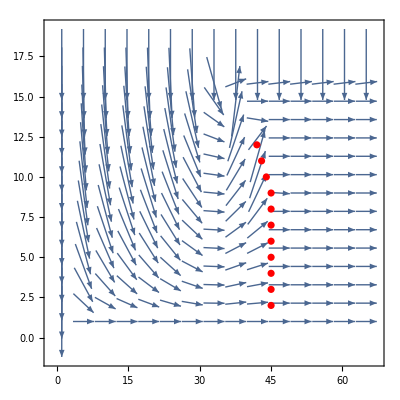

```mathematica
Show[c,d]
```

```mathematica
0.735398*180/3.141592653
```

42.1352

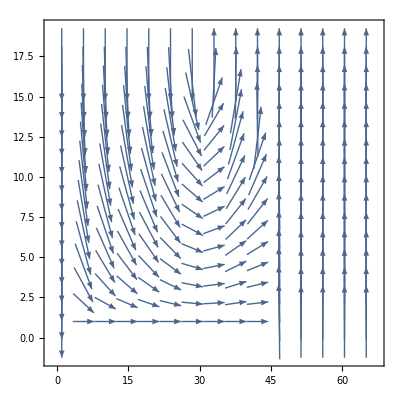

```mathematica
a={{{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.707107,-0.707107},{0.496761,-0.867887},{0.359513,-0.933140},{0.271579,-0.962416},{0.212585,-0.977143},{0.170567,-0.985346},{0.138929,-0.990302},{0.113954,-0.993486},{0.093442,-0.995625},{0.076015,-0.997107},{0.060765,-0.998152},{0.047063,-0.998892},{0.034452,-0.999406},{0.022585,-0.999745},{0.011181,-0.999937},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.887080,-0.461616},{0.722966,-0.690883},{0.582030,-0.813167},{0.471390,-0.881925},{0.385535,-0.922693},{0.318023,-0.948083},{0.263728,-0.964597},{0.218937,-0.975739},{0.181026,-0.983478},{0.148132,-0.988968},{0.118912,-0.992905},{0.092376,-0.995724},{0.067766,-0.997701},{0.044486,-0.999010},{0.022042,-0.999757},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.942000,-0.335614},{0.827899,-0.560877},{0.709481,-0.704725},{0.603035,-0.797715},{0.511425,-0.859328},{0.433377,-0.901213},{0.366612,-0.930374},{0.308871,-0.951104},{0.258206,-0.966090},{0.213028,-0.977046},{0.172056,-0.985087},{0.134264,-0.990946},{0.098813,-0.995106},{0.065008,-0.997885},{0.032250,-0.999480},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.964406,-0.264425},{0.882499,-0.470313},{0.785853,-0.618414},{0.690172,-0.723646},{0.601324,-0.799006},{0.520811,-0.853672},{0.448361,-0.893853},{0.383046,-0.923729},{0.323763,-0.946138},{0.269434,-0.963019},{0.219078,-0.975707},{0.171831,-0.985126},{0.126935,-0.991911},{0.083723,-0.996489},{0.041596,-0.999135},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.975425,-0.220333},{0.913689,-0.406414},{0.834126,-0.551574},{0.749493,-0.662012},{0.666184,-0.745787},{0.586936,-0.809634},{0.512633,-0.858608},{0.443266,-0.896390},{0.378411,-0.925638},{0.317478,-0.948265},{0.259828,-0.965655},{0.204829,-0.978798},{0.151888,-0.988398},{0.100445,-0.994943},{0.049982,-0.998750},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.981600,-0.190947},{0.932901,-0.360133},{0.866154,-0.499777},{0.791176,-0.611589},{0.713893,-0.700254},{0.637442,-0.770498},{0.563301,-0.826252},{0.492025,-0.870581},{0.423669,-0.905817},{0.358023,-0.933713},{0.294752,-0.955574},{0.233462,-0.972366},{0.173744,-0.984791},{0.115190,-0.993343},{0.057405,-0.998351},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.985407,-0.170213},{0.945490,-0.325652},{0.888331,-0.459204},{0.821374,-0.570390},{0.749761,-0.661708},{0.676602,-0.736349},{0.603625,-0.797269},{0.531703,-0.846931},{0.461204,-0.887294},{0.392196,-0.919882},{0.324585,-0.945856},{0.258187,-0.966095},{0.192776,-0.981243},{0.128106,-0.991760},{0.063930,-0.997954},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.987929,-0.154908},{0.954176,-0.299245},{0.904282,-0.426935},{0.843896,-0.536507},{0.777341,-0.629079},{0.707501,-0.706713},{0.636149,-0.771566},{0.564318,-0.825558},{0.492561,-0.870278},{0.421141,-0.906995},{0.350148,-0.936694},{0.279573,-0.960124},{0.209357,-0.977839},{0.139418,-0.990234},{0.069663,-0.997571},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.989697,-0.143176},{0.960444,-0.278473},{0.916163,-0.400806},{0.861171,-0.508316},{0.799046,-0.601270},{0.732360,-0.680918},{0.662819,-0.748780},{0.591504,-0.806302},{0.519070,-0.854731},{0.445908,-0.895079},{0.372244,-0.928135},{0.298212,-0.954500},{0.223903,-0.974611},{0.149386,-0.988779},{0.074729,-0.997204},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.990998,-0.133876},{0.965151,-0.261694},{0.925309,-0.379214},{0.874796,-0.484491},{0.816546,-0.577280},{0.752795,-0.658255},{0.685116,-0.728434},{0.614569,-0.788863},{0.541850,-0.840475},{0.467425,-0.884033},{0.391617,-0.920128},{0.314678,-0.949199},{0.236827,-0.971552},{0.158281,-0.987394},{0.079260,-0.996854},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.991996,-0.126266},{0.968821,-0.247763},{0.932583,-0.360955},{0.885858,-0.463957},{0.831028,-0.556231},{0.770002,-0.638042},{0.704183,-0.710018},{0.634563,-0.772871},{0.561833,-0.827251},{0.486494,-0.873684},{0.408936,-0.912563},{0.329503,-0.944154},{0.248529,-0.968624},{0.166366,-0.986064},{0.083390,-0.996517},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.992794,-0.119834},{0.971788,-0.235856},{0.938563,-0.345107},{0.895113,-0.445840},{0.843355,-0.537356},{0.784885,-0.619641},{0.720917,-0.693022},{0.652340,-0.757927},{0.579806,-0.814755},{0.503818,-0.863810},{0.424806,-0.905284},{0.343184,-0.939268},{0.259389,-0.965773},{0.173899,-0.984763},{0.087246,-0.996187},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.993456,-0.114215},{0.974277,-0.225354},{0.943649,-0.330947},{0.903108,-0.429413},{0.854174,-0.519987},{0.798144,-0.602466},{0.736034,-0.676945},{0.668606,-0.743617},{0.596441,-0.802657},{0.520017,-0.854156},{0.439776,-0.898108},{0.356184,-0.934416},{0.269767,-0.962926},{0.181129,-0.983459},{0.090957,-0.995855},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994027,-0.109133},{0.976442,-0.215780},{0.948128,-0.317887},{0.910249,-0.414061},{0.863978,-0.503529},{0.810335,-0.585967},{0.750124,-0.661297},{0.683962,-0.729518},{0.612330,-0.790602},{0.535652,-0.844439},{0.454358,-0.890819},{0.368946,-0.929451},{0.280018,-0.959995},{0.188303,-0.982111},{0.094649,-0.995511},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.994538,-0.104372},{0.978395,-0.206746},{0.952212,-0.305439},{0.916843,-0.399247},{0.873158,-0.487438},{0.821907,-0.569621},{0.763683,-0.645591},{0.698931,-0.715189},{0.628007,-0.778207},{0.551249,-0.834341},{0.469046,-0.883174},{0.381907,-0.924201},{0.290499,-0.956875},{0.195674,-0.980669},{0.098454,-0.995142},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995012,-0.099755},{0.980216,-0.197932},{0.956057,-0.293180},{0.923129,-0.384491},{0.882023,-0.471207},{0.833237,-0.552916},{0.777138,-0.629330},{0.713982,-0.700164},{0.643968,-0.765053},{0.567312,-0.823503},{0.484333,-0.874884},{0.395518,-0.918458},{0.301587,-0.953439},{0.203513,-0.979072},{0.102514,-0.994732},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995465,-0.095133},{0.981965,-0.189061},{0.959786,-0.280733},{0.929291,-0.369349},{0.890824,-0.454348},{0.844636,-0.535341},{0.790861,-0.611996},{0.729541,-0.683937},{0.660684,-0.750664},{0.584346,-0.811505},{0.500725,-0.865606},{0.410259,-0.911969},{0.313693,-0.949524},{0.212125,-0.977243},{0.106991,-0.994260},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.995907,-0.090379},{0.983688,-0.179886},{0.963486,-0.267757},{0.935472,-0.353400},{0.899761,-0.436383},{0.856365,-0.516371},{0.805178,-0.593033},{0.746003,-0.665943},{0.678616,-0.734493},{0.602862,-0.797845},{0.518767,-0.854916},{0.426662,-0.904411},{0.327288,-0.944925},{0.221863,-0.975078},{0.112076,-0.993700},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996349,-0.085377},{0.985412,-0.170187},{0.967221,-0.253937},{0.941775,-0.336245},{0.908984,-0.416832},{0.868631,-0.495459},{0.820365,-0.571840},{0.763726,-0.645541},{0.698212,-0.715891},{0.623395,-0.781907},{0.539052,-0.842273},{0.445336,-0.895363},{0.342931,-0.939361},{0.233159,-0.972439},{0.118004,-0.993013},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.996793,-0.080029},{0.987154,-0.159769},{0.971024,-0.238980},{0.948259,-0.317499},{0.918588,-0.395217},{0.881582,-0.472030},{0.836643,-0.547749},{0.783024,-0.621992},{0.719903,-0.694075},{0.646498,-0.762916},{0.562241,-0.826973},{0.467000,-0.884257},{0.361309,-0.932446},{0.246561,-0.969127},{0.125082,-0.992146},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997240,-0.074248},{0.988919,-0.148457},{0.974904,-0.222624},{0.954940,-0.296798},{0.928608,-0.371062},{0.895289,-0.445485},{0.854148,-0.520030},{0.804141,-0.594438},{0.744077,-0.668093},{0.672736,-0.739883},{0.589073,-0.808080},{0.492510,-0.870307},{0.383286,-0.923630},{0.262785,-0.964854},{0.133717,-0.991020},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.997688,-0.067967},{0.990694,-0.136112},{0.978837,-0.204642},{0.961783,-0.273813},{0.939002,-0.343911},{0.909726,-0.415210},{0.872907,-0.487886},{0.827212,-0.561890},{0.771044,-0.636782},{0.702652,-0.711533},{0.620353,-0.784322},{0.522897,-0.852396},{0.409977,-0.912096},{0.282799,-0.959179},{0.144479,-0.989508},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998129,-0.061138},{0.992453,-0.122629},{0.982765,-0.184861},{0.968690,-0.248273},{0.949637,-0.313352},{0.924738,-0.380605},{0.892788,-0.450477},{0.852194,-0.523227},{0.800950,-0.598732},{0.736697,-0.676223},{0.656924,-0.753957},{0.559388,-0.828906},{0.442840,-0.896601},{0.307955,-0.951401},{0.158196,-0.987408},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998555,-0.053740},{0.994155,-0.107961},{0.986596,-0.163180},{0.975502,-0.219989},{0.960274,-0.279060},{0.940014,-0.341135},{0.913441,-0.406972},{0.878777,-0.477232},{0.833660,-0.552278},{0.775093,-0.631847},{0.699551,-0.714583},{0.603396,-0.797442},{0.483789,-0.875185},{0.340196,-0.940354},{0.176121,-0.984369},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.998951,-0.045788},{0.995748,-0.092122},{0.990208,-0.139598},{0.981996,-0.188904},{0.970561,-0.240855},{0.955062,-0.296408},{0.934242,-0.356639},{0.906278,-0.422681},{0.868581,-0.495547},{0.817596,-0.575792},{0.748694,-0.662916},{0.656389,-0.754423},{0.535306,-0.844658},{0.382386,-0.924003},{0.200253,-0.979744},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999303,-0.037333},{0.997168,-0.075210},{0.993454,-0.114236},{0.987894,-0.155129},{0.980045,-0.198777},{0.969198,-0.246283},{0.954253,-0.298999},{0.933520,-0.358524},{0.904428,-0.426626},{0.863127,-0.504986},{0.804027,-0.594592},{0.719501,-0.694491},{0.600421,-0.799684},{0.438821,-0.898574},{0.233976,-0.972242},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999595,-0.028472},{0.998350,-0.057415},{0.996176,-0.087367},{0.992895,-0.118992},{0.988202,-0.153158},{0.981589,-0.191005},{0.972229,-0.234032},{0.958769,-0.284188},{0.938992,-0.343939},{0.909255,-0.416240},{0.863595,-0.504186},{0.792537,-0.609823},{0.682188,-0.731177},{0.515896,-0.856651},{0.283402,-0.959001},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999813,-0.019347},{0.999238,-0.039023},{0.998233,-0.059422},{0.996708,-0.081069},{0.994504,-0.104696},{0.991338,-0.131335},{0.986720,-0.162430},{0.979794,-0.200008},{0.969038,-0.246913},{0.951676,-0.307103},{0.922531,-0.385923},{0.871825,-0.489817},{0.781575,-0.623811},{0.622281,-0.782794},{0.360354,-0.932816},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999949,-0.010143},{0.999792,-0.020412},{0.999520,-0.030991},{0.999110,-0.042183},{0.998515,-0.054479},{0.997642,-0.068639},{0.996311,-0.085810},{0.994183,-0.107707},{0.990582,-0.136924},{0.984120,-0.177502},{0.971768,-0.235939},{0.946483,-0.322753},{0.891179,-0.453652},{0.765154,-0.643847},{0.488543,-0.872540},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999999,-0.001079},{0.999998,-0.002034},{0.999996,-0.002792},{0.999994,-0.003372},{0.999992,-0.003943},{0.999988,-0.004870},{0.999977,-0.006788},{0.999943,-0.010705},{0.999834,-0.018224},{0.999488,-0.032009},{0.998377,-0.056943},{0.994680,-0.103018},{0.981316,-0.192403},{0.927958,-0.372684},{0.708414,-0.705797},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999971,0.007607},{0.999878,0.015613},{0.999703,0.024378},{0.999415,0.034190},{0.998976,0.045241},{0.998339,0.057606},{0.997458,0.071254},{0.996289,0.086070},{0.994794,0.101902},{0.992942,0.118605},{0.990714,0.135959},{0.988263,0.152760},{0.986874,0.161494},{0.992698,0.120626},{0.984524,-0.175248},{-0.000000,-1.000000}},{{1.000000,-0.000000},{0.999877,0.015670},{0.999487,0.032022},{0.998764,0.049704},{0.997595,0.069310},{0.995818,0.091363},{0.993210,0.116337},{0.989474,0.144713},{0.984189,0.177124},{0.976697,0.214624},{0.965814,0.259237},{0.949042,0.315151},{0.920093,0.391701},{0.859456,0.511209},{0.691394,0.722478},{0.095573,0.995422},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999738,0.022877},{0.998908,0.046711},{0.997374,0.072426},{0.994898,0.100885},{0.991132,0.132880},{0.985589,0.169157},{0.977597,0.210487},{0.966189,0.257834},{0.949871,0.312643},{0.926086,0.377312},{0.890021,0.455919},{0.831792,0.555087},{0.729945,0.683506},{0.538987,0.842314},{0.190272,0.981731},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999579,0.029018},{0.998243,0.059255},{0.995770,0.091884},{0.991775,0.127996},{0.985690,0.168567},{0.976732,0.214465},{0.963836,0.266496},{0.945536,0.325517},{0.919704,0.392613},{0.883056,0.469268},{0.830273,0.557358},{0.752684,0.658382},{0.637489,0.770460},{0.474288,0.880370},{0.283228,0.959053},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999425,0.033916},{0.997596,0.069297},{0.994200,0.107547},{0.988695,0.149942},{0.980288,0.197572},{0.967909,0.251301},{0.950160,0.311762},{0.925228,0.379411},{0.890705,0.454582},{0.843276,0.537480},{0.778311,0.627879},{0.689477,0.724307},{0.568124,0.822943},{0.397212,0.917727},{0.373591,0.927593},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999300,0.037422},{0.997066,0.076551},{0.992894,0.119006},{0.986087,0.166228},{0.975640,0.219377},{0.960223,0.279233},{0.938182,0.346143},{0.907518,0.420014},{0.865829,0.500340},{0.810201,0.586153},{0.737160,0.675718},{0.643384,0.765543},{0.530796,0.847499},{0.420572,0.907259},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999223,0.039417},{0.996732,0.080786},{0.992037,0.125947},{0.984299,0.176509},{0.972310,0.233693},{0.954511,0.298174},{0.929045,0.369966},{0.893835,0.448395},{0.846646,0.532156},{0.785104,0.619364},{0.706538,0.707675},{0.606569,0.795031},{0.471436,0.881900},{0.443657,0.896196},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999208,0.039798},{0.996648,0.081807},{0.991760,0.128113},{0.983572,0.180518},{0.970689,0.240340},{0.951330,0.308175},{0.923453,0.383713},{0.884941,0.465704},{0.833775,0.552105},{0.768268,0.640129},{0.687757,0.725941},{0.594630,0.803999},{0.498754,0.866743},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999260,0.038465},{0.996841,0.079427},{0.992125,0.125250},{0.984033,0.177987},{0.970989,0.239124},{0.950979,0.309254},{0.921750,0.387784},{0.881122,0.472889},{0.827191,0.561921},{0.758362,0.651834},{0.673940,0.738786},{0.572347,0.820012},{0.525586,0.850741},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999376,0.035313},{0.997300,0.073441},{0.993124,0.117070},{0.985689,0.168577},{0.973254,0.229730},{0.953542,0.301261},{0.924011,0.382365},{0.882397,0.470505},{0.826995,0.562209},{0.756046,0.654518},{0.666625,0.745394},{0.617316,0.786716},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999543,0.030218},{0.997975,0.063600},{0.994660,0.103203},{0.988410,0.151810},{0.977351,0.211624},{0.958899,0.283747},{0.930065,0.367395},{0.888405,0.459060},{0.833051,0.553196},{0.760416,0.649436},{0.713175,0.700987},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999735,0.023024},{0.998770,0.049590},{0.996536,0.083168},{0.991900,0.127024},{0.982935,0.183951},{0.966741,0.255759},{0.939569,0.342359},{0.898177,0.439634},{0.843933,0.536449},{0.803939,0.594711},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999909,0.013527},{0.999519,0.031005},{0.998411,0.056347},{0.995633,0.093351},{0.989360,0.145487},{0.976500,0.215516},{0.952297,0.305172},{0.909083,0.416616},{0.879711,0.475508},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{1.000000,-0.000000},{0.999999,0.001465},{0.999973,0.007324},{0.999759,0.021967},{0.998762,0.049743},{0.995498,0.094786},{0.987037,0.160490},{0.968678,0.248318},{0.934517,0.355919},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}},{{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000},{0.000000,1.000000}}};
ListVectorPlot[a]
```